# Network Robustness to BDM-Directed Sequential and Simultaneous Attack

June 2018

Author : Antonio Rueda - Toicen
antonio.rueda.toicen@{ algoritmicnaturelab.org, gmail.com}

One can direct attacks to the elements (nodes/edges) in a network according to a “centrality” metric that assigns a relative important to each. In a “sequential attack” that erases i elements, after an element is removed the centrality metric is re-evaluated to take into account the change in the network’s structure, whereas in a “simultaneous” attack the centrality metric of every element is evaluated once, prior to any deletion [Iyer13].  The Block Decomposition Method (BDM) can be used to assign centrality scores to vertices or edges according to their information contribution [Zenil14, Zenil16, Zenil18a, Zenil18b].

Robustness to directed attacks of vertices in a connected graph can be quantified according to the R-index

-Graphics-

Being N the number of vertices in the network and σ(i/N) the relative size of the network after i vertices have been removed.

For any type of attack to remove vertices from any network, R attains its minimum value of 1/N on the star graph and its maximum value of (1/2) (1 -1/N) on the complete graph.Thus, for any network and method of vertex removal, R ϵ [0, 1/2] [Iyer13] .

The Block Decomposition Method is implemented using the Coding Theorem Method data and code from "Kolmogorov Complexity of 3 × 3 and 4 × 4 Squares" [Soler13]

```mathematica
Clear["Global`*"]
```

```mathematica
D2DRepres = {{{{0,0,0},{0,0,0},{0,0,0}},13.713356989265955},{{{0,0,0},{0,0,0},{0,0,1}},14.914491375110648},{{{0,0,0},{0,0,0},{0,1,0}},14.815062288419652},{{{0,0,0},{0,0,0},{0,1,1}},15.941579969636367},{{{0,0,0},{0,0,0},{1,0,1}},16.900030404099436},{{{0,0,0},{0,0,0},{1,1,1}},16.95562693976486},{{{0,0,0},{0,0,1},{0,1,0}},15.696612950809524},{{{0,0,0},{0,0,1},{0,1,1}},17.62373085163188},{{{0,0,0},{0,0,1},{1,0,0}},15.78735242844744},{{{0,0,0},{0,0,1},{1,0,1}},17.854607164922214},{{{0,0,0},{0,0,1},{1,1,0}},16.261880476627034},{{{0,0,0},{0,0,1},{1,1,1}},17.79099027006017},{{{0,0,0},{0,1,0},{0,0,0}},14.366394383270709},{{{0,0,0},{0,1,0},{0,0,1}},15.4100416811352},{{{0,0,0},{0,1,0},{0,1,0}},15.32169282402135},{{{0,0,0},{0,1,0},{0,1,1}},16.49512736777431},{{{0,0,0},{0,1,0},{1,0,1}},18.3368731060255},{{{0,0,0},{0,1,0},{1,1,1}},18.327674281086303},{{{0,0,0},{0,1,1},{0,1,0}},16.149904887374973},{{{0,0,0},{0,1,1},{0,1,1}},17.616157737686187},{{{0,0,0},{0,1,1},{1,0,0}},15.970999378598538},{{{0,0,0},{0,1,1},{1,0,1}},18.92890357141047},{{{0,0,0},{0,1,1},{1,1,0}},16.476306662461006},{{{0,0,0},{1,0,1},{0,0,0}},16.255262060168807},{{{0,0,0},{1,0,1},{0,0,1}},17.104691927835958},{{{0,0,0},{1,0,1},{0,1,0}},16.73365644982906},{{{0,0,0},{1,0,1},{0,1,1}},18.45555102314149},{{{0,0,0},{1,0,1},{1,0,1}},18.580864438414107},{{{0,0,0},{1,1,1},{0,0,0}},16.16173099207288},{{{0,0,0},{1,1,1},{0,0,1}},17.018774218181772},{{{0,0,0},{1,1,1},{0,1,0}},16.719591645677742},{{{0,0,0},{1,1,1},{0,1,1}},17.491110914380187},{{{0,0,0},{1,1,1},{1,0,1}},18.680113095310837},{{{0,0,1},{0,0,0},{1,0,0}},15.49045504078404},{{{0,0,1},{0,0,0},{1,0,1}},17.316632891027243},{{{0,0,1},{0,0,0},{1,1,0}},16.27316424670126},{{{0,0,1},{0,0,1},{1,1,0}},16.85323886184152},{{{0,0,1},{0,1,0},{1,0,0}},15.601133845368501},{{{0,0,1},{0,1,0},{1,0,1}},18.13105140995317},{{{0,0,1},{0,1,0},{1,1,0}},16.36182798445243},{{{0,0,1},{0,1,1},{1,1,0}},16.81279391621911},{{{0,0,1},{1,0,0},{0,0,1}},18.38286372231791},{{{0,0,1},{1,0,0},{0,1,0}},17.212914516396264},{{{0,0,1},{1,0,0},{0,1,1}},18.980868502975127},{{{0,0,1},{1,0,0},{1,0,1}},17.231501378198235},{{{0,0,1},{1,0,1},{0,1,0}},17.39355468629877},{{{0,0,1},{1,0,1},{1,0,0}},16.21735754583781},{{{0,0,1},{1,1,0},{0,0,1}},18.59627095161859},{{{0,0,1},{1,1,0},{0,1,0}},17.165765197608998},{{{0,1,0},{1,0,1},{0,1,0}},17.082165127627736},{{{0,1,0},{1,1,1},{0,1,0}},17.355908321894567},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},22.006706292292176},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1}},23.347935957593144},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,1,0}},24.325701071360243},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,1,1}},24.60462140484821},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,1,0,1}},26.693307834514123},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,1,1,0}},26.16773493607177},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,1,1,1}},27.26436715310943},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{1,0,0,1}},27.19853156893639},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{1,0,1,1}},27.125247293032764},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{1,1,1,1}},26.97861475290055},{{{0,0,0,0},{0,0,0,0},{0,0,0,1},{0,0,1,0}},25.396132112819828},{{{0,0,0,0},{0,0,0,0},{0,0,0,1},{0,0,1,1}},26.660495727144173},{{{0,0,0,0},{0,0,0,0},{0,0,0,1},{0,1,0,0}},25.2544735894907},{{{0,0,0,0},{0,0,0,0},{0,0,0,1},{0,1,0,1}},28.914474910152038},{{{0,0,0,0},{0,0,0,0},{0,0,0,1},{0,1,1,0}},26.377888500835518},{{{0,0,0,0},{0,0,0,0},{0,0,0,1},{0,1,1,1}},28.865544398168197},{{{0,0,0,0},{0,0,0,0},{0,0,0,1},{1,0,0,0}},26.63999334205468},{{{0,0,0,0},{0,0,0,0},{0,0,0,1},{1,0,0,1}},29.26897182236622},{{{0,0,0,0},{0,0,0,0},{0,0,0,1},{1,0,1,0}},26.63447155302066},{{{0,0,0,0},{0,0,0,0},{0,0,0,1},{1,0,1,1}},27.524060706958192},{{{0,0,0,0},{0,0,0,0},{0,0,0,1},{1,1,0,0}},26.082887876722896},{{{0,0,0,0},{0,0,0,0},{0,0,0,1},{1,1,0,1}},30.104404031093413},{{{0,0,0,0},{0,0,0,0},{0,0,0,1},{1,1,1,0}},26.474199514991223},{{{0,0,0,0},{0,0,0,0},{0,0,0,1},{1,1,1,1}},28.550952503117475},{{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,0}},23.560267543830992},{{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}},24.857707411171532},{{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,1,0}},25.065876918766953},{{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,1,1}},25.64137709785745},{{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,1,0,0}},25.254258544566216},{{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,1,0,1}},27.983322827261233},{{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,1,1,0}},27.11020027468713},{{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,1,1,1}},27.11746343675225},{{{0,0,0,0},{0,0,0,0},{0,0,1,0},{1,0,0,0}},25.04728617844376},{{{0,0,0,0},{0,0,0,0},{0,0,1,0},{1,0,0,1}},28.862112052319258},{{{0,0,0,0},{0,0,0,0},{0,0,1,0},{1,0,1,0}},28.606119388265842},{{{0,0,0,0},{0,0,0,0},{0,0,1,0},{1,0,1,1}},28.54754321825192},{{{0,0,0,0},{0,0,0,0},{0,0,1,0},{1,1,0,0}},26.25931229463},{{{0,0,0,0},{0,0,0,0},{0,0,1,0},{1,1,0,1}},28.66383143970743},{{{0,0,0,0},{0,0,0,0},{0,0,1,0},{1,1,1,0}},28.57108460018346},{{{0,0,0,0},{0,0,0,0},{0,0,1,0},{1,1,1,1}},27.910924301672203},{{{0,0,0,0},{0,0,0,0},{0,0,1,1},{0,0,1,0}},25.85969412710375},{{{0,0,0,0},{0,0,0,0},{0,0,1,1},{0,0,1,1}},26.791377058335424},{{{0,0,0,0},{0,0,0,0},{0,0,1,1},{0,1,0,0}},25.951864320554247},{{{0,0,0,0},{0,0,0,0},{0,0,1,1},{0,1,0,1}},28.93638861965973},{{{0,0,0,0},{0,0,0,0},{0,0,1,1},{0,1,1,0}},27.162261930258275},{{{0,0,0,0},{0,0,0,0},{0,0,1,1},{0,1,1,1}},28.915102396225386},{{{0,0,0,0},{0,0,0,0},{0,0,1,1},{1,0,0,0}},26.549043934352127},{{{0,0,0,0},{0,0,0,0},{0,0,1,1},{1,0,0,1}},30.87304314603508},{{{0,0,0,0},{0,0,0,0},{0,0,1,1},{1,0,1,0}},27.81968701530312},{{{0,0,0,0},{0,0,0,0},{0,0,1,1},{1,0,1,1}},28.807888355379063},{{{0,0,0,0},{0,0,0,0},{0,0,1,1},{1,1,0,0}},25.96493388637474},{{{0,0,0,0},{0,0,0,0},{0,0,1,1},{1,1,0,1}},31.211319235009924},{{{0,0,0,0},{0,0,0,0},{0,0,1,1},{1,1,1,0}},27.42131658778354},{{{0,0,0,0},{0,0,0,0},{0,0,1,1},{1,1,1,1}},28.792241378904993},{{{0,0,0,0},{0,0,0,0},{0,1,0,1},{0,0,0,0}},25.84993776203438},{{{0,0,0,0},{0,0,0,0},{0,1,0,1},{0,0,0,1}},26.831879153909075},{{{0,0,0,0},{0,0,0,0},{0,1,0,1},{0,0,1,0}},26.57310509517619},{{{0,0,0,0},{0,0,0,0},{0,1,0,1},{0,0,1,1}},27.951864320554247},{{{0,0,0,0},{0,0,0,0},{0,1,0,1},{0,1,0,0}},26.785245667034967},{{{0,0,0,0},{0,0,0,0},{0,1,0,1},{0,1,0,1}},29.178806421491434},{{{0,0,0,0},{0,0,0,0},{0,1,0,1},{0,1,1,0}},28.17479335898481},{{{0,0,0,0},{0,0,0,0},{0,1,0,1},{0,1,1,1}},29.953689633616936},{{{0,0,0,0},{0,0,0,0},{0,1,0,1},{1,0,0,0}},27.245962478885826},{{{0,0,0,0},{0,0,0,0},{0,1,0,1},{1,0,0,1}},30.39927452404921},{{{0,0,0,0},{0,0,0,0},{0,1,0,1},{1,0,1,0}},27.190343252070985},{{{0,0,0,0},{0,0,0,0},{0,1,0,1},{1,0,1,1}},30.28780974210387},{{{0,0,0,0},{0,0,0,0},{0,1,0,1},{1,1,0,0}},27.042536419551496},{{{0,0,0,0},{0,0,0,0},{0,1,0,1},{1,1,0,1}},30.372600142042984},{{{0,0,0,0},{0,0,0,0},{0,1,0,1},{1,1,1,0}},27.053662804969075},{{{0,0,0,0},{0,0,0,0},{0,1,0,1},{1,1,1,1}},30.07185533722522},{{{0,0,0,0},{0,0,0,0},{0,1,1,0},{0,0,0,0}},25.086505682878315},{{{0,0,0,0},{0,0,0,0},{0,1,1,0},{0,0,0,1}},26.42954855579643},{{{0,0,0,0},{0,0,0,0},{0,1,1,0},{0,0,1,0}},26.058940488642328},{{{0,0,0,0},{0,0,0,0},{0,1,1,0},{0,0,1,1}},26.196686730790702},{{{0,0,0,0},{0,0,0,0},{0,1,1,0},{0,1,0,1}},29.177049332925176},{{{0,0,0,0},{0,0,0,0},{0,1,1,0},{0,1,1,0}},28.28618539022551},{{{0,0,0,0},{0,0,0,0},{0,1,1,0},{0,1,1,1}},27.858386107658458},{{{0,0,0,0},{0,0,0,0},{0,1,1,0},{1,0,0,1}},31.030021834770835},{{{0,0,0,0},{0,0,0,0},{0,1,1,0},{1,0,1,1}},30.564014566459516},{{{0,0,0,0},{0,0,0,0},{0,1,1,0},{1,1,1,1}},29.702305587522066},{{{0,0,0,0},{0,0,0,0},{0,1,1,1},{0,0,0,0}},26.054008291709714},{{{0,0,0,0},{0,0,0,0},{0,1,1,1},{0,0,0,1}},27.314603029519052},{{{0,0,0,0},{0,0,0,0},{0,1,1,1},{0,0,1,0}},26.889442519065955},{{{0,0,0,0},{0,0,0,0},{0,1,1,1},{0,0,1,1}},27.14959226272148},{{{0,0,0,0},{0,0,0,0},{0,1,1,1},{0,1,0,0}},27.479526395040196},{{{0,0,0,0},{0,0,0,0},{0,1,1,1},{0,1,0,1}},29.611703038741158},{{{0,0,0,0},{0,0,0,0},{0,1,1,1},{0,1,1,0}},27.948434689542445},{{{0,0,0,0},{0,0,0,0},{0,1,1,1},{0,1,1,1}},29.64046885842526},{{{0,0,0,0},{0,0,0,0},{0,1,1,1},{1,0,0,0}},26.97125502146297},{{{0,0,0,0},{0,0,0,0},{0,1,1,1},{1,0,0,1}},31.18283067805023},{{{0,0,0,0},{0,0,0,0},{0,1,1,1},{1,0,1,0}},27.95584002161513},{{{0,0,0,0},{0,0,0,0},{0,1,1,1},{1,0,1,1}},30.857682280395224},{{{0,0,0,0},{0,0,0,0},{0,1,1,1},{1,1,0,0}},26.555959251177796},{{{0,0,0,0},{0,0,0,0},{0,1,1,1},{1,1,0,1}},30.967074002027218},{{{0,0,0,0},{0,0,0,0},{0,1,1,1},{1,1,1,0}},27.161827467681647},{{{0,0,0,0},{0,0,0,0},{0,1,1,1},{1,1,1,1}},29.756378499503644},{{{0,0,0,0},{0,0,0,0},{1,0,0,1},{0,0,0,0}},25.971037527015508},{{{0,0,0,0},{0,0,0,0},{1,0,0,1},{0,0,0,1}},29.039796690845446},{{{0,0,0,0},{0,0,0,0},{1,0,0,1},{0,0,1,0}},26.329512409430883},{{{0,0,0,0},{0,0,0,0},{1,0,0,1},{0,0,1,1}},28.074072624276585},{{{0,0,0,0},{0,0,0,0},{1,0,0,1},{0,1,0,1}},28.797438204763658},{{{0,0,0,0},{0,0,0,0},{1,0,0,1},{0,1,1,0}},27.770314051404544},{{{0,0,0,0},{0,0,0,0},{1,0,0,1},{0,1,1,1}},29.551602805152772},{{{0,0,0,0},{0,0,0,0},{1,0,0,1},{1,0,0,1}},26.873144747854965},{{{0,0,0,0},{0,0,0,0},{1,0,0,1},{1,0,1,1}},27.9932269511071},{{{0,0,0,0},{0,0,0,0},{1,0,0,1},{1,1,1,1}},28.947685543330273},{{{0,0,0,0},{0,0,0,0},{1,0,1,1},{0,0,0,0}},25.754950192779056},{{{0,0,0,0},{0,0,0,0},{1,0,1,1},{0,0,0,1}},29.19980524699288},{{{0,0,0,0},{0,0,0,0},{1,0,1,1},{0,0,1,0}},27.215048959056094},{{{0,0,0,0},{0,0,0,0},{1,0,1,1},{0,0,1,1}},28.559756410222263},{{{0,0,0,0},{0,0,0,0},{1,0,1,1},{0,1,0,0}},26.514123930197695},{{{0,0,0,0},{0,0,0,0},{1,0,1,1},{0,1,0,1}},29.194209455263152},{{{0,0,0,0},{0,0,0,0},{1,0,1,1},{0,1,1,0}},27.53173888917564},{{{0,0,0,0},{0,0,0,0},{1,0,1,1},{0,1,1,1}},29.471274247911747},{{{0,0,0,0},{0,0,0,0},{1,0,1,1},{1,0,0,0}},29.12288960193859},{{{0,0,0,0},{0,0,0,0},{1,0,1,1},{1,0,0,1}},27.96772479297467},{{{0,0,0,0},{0,0,0,0},{1,0,1,1},{1,0,1,0}},28.60274584518559},{{{0,0,0,0},{0,0,0,0},{1,0,1,1},{1,0,1,1}},29.46574785027604},{{{0,0,0,0},{0,0,0,0},{1,0,1,1},{1,1,0,0}},27.668584969678065},{{{0,0,0,0},{0,0,0,0},{1,0,1,1},{1,1,0,1}},30.42287742335263},{{{0,0,0,0},{0,0,0,0},{1,0,1,1},{1,1,1,0}},29.932360223218136},{{{0,0,0,0},{0,0,0,0},{1,0,1,1},{1,1,1,1}},29.38211150130606},{{{0,0,0,0},{0,0,0,0},{1,1,1,1},{0,0,0,0}},25.534066399690527},{{{0,0,0,0},{0,0,0,0},{1,1,1,1},{0,0,0,1}},28.685257559197275},{{{0,0,0,0},{0,0,0,0},{1,1,1,1},{0,0,1,0}},27.050442245460186},{{{0,0,0,0},{0,0,0,0},{1,1,1,1},{0,0,1,1}},27.848463750365845},{{{0,0,0,0},{0,0,0,0},{1,1,1,1},{0,1,0,1}},28.439933230695523},{{{0,0,0,0},{0,0,0,0},{1,1,1,1},{0,1,1,0}},27.3845715867304},{{{0,0,0,0},{0,0,0,0},{1,1,1,1},{0,1,1,1}},29.13015638211532},{{{0,0,0,0},{0,0,0,0},{1,1,1,1},{1,0,0,1}},30.165804575757555},{{{0,0,0,0},{0,0,0,0},{1,1,1,1},{1,0,1,1}},30.436626019608852},{{{0,0,0,0},{0,0,0,0},{1,1,1,1},{1,1,1,1}},29.491720772813807},{{{0,0,0,0},{0,0,0,1},{0,0,0,0},{0,1,0,0}},24.370500971542068},{{{0,0,0,0},{0,0,0,1},{0,0,0,0},{0,1,0,1}},29.534789494705695},{{{0,0,0,0},{0,0,0,1},{0,0,0,0},{0,1,1,0}},26.164001090116926},{{{0,0,0,0},{0,0,0,1},{0,0,0,0},{0,1,1,1}},30.25301852629031},{{{0,0,0,0},{0,0,0,1},{0,0,0,0},{1,0,0,0}},24.689411258916643},{{{0,0,0,0},{0,0,0,1},{0,0,0,0},{1,0,0,1}},29.64670829888969},{{{0,0,0,0},{0,0,0,1},{0,0,0,0},{1,0,1,0}},26.24172567891247},{{{0,0,0,0},{0,0,0,1},{0,0,0,0},{1,0,1,1}},30.38413714907365},{{{0,0,0,0},{0,0,0,1},{0,0,0,0},{1,1,0,0}},24.762458746982155},{{{0,0,0,0},{0,0,0,1},{0,0,0,0},{1,1,0,1}},29.806335400395003},{{{0,0,0,0},{0,0,0,1},{0,0,0,0},{1,1,1,0}},26.220112353467933},{{{0,0,0,0},{0,0,0,1},{0,0,0,0},{1,1,1,1}},30.01828887330482},{{{0,0,0,0},{0,0,0,1},{0,0,0,1},{0,1,1,0}},26.557958659159873},{{{0,0,0,0},{0,0,0,1},{0,0,0,1},{0,1,1,1}},30.0863878878147},{{{0,0,0,0},{0,0,0,1},{0,0,0,1},{1,0,0,0}},28.349940663885487},{{{0,0,0,0},{0,0,0,1},{0,0,0,1},{1,0,0,1}},31.416348037408152},{{{0,0,0,0},{0,0,0,1},{0,0,0,1},{1,0,1,0}},28.350647832685922},{{{0,0,0,0},{0,0,0,1},{0,0,0,1},{1,0,1,1}},29.60730199449006},{{{0,0,0,0},{0,0,0,1},{0,0,0,1},{1,1,0,0}},27.41990585682134},{{{0,0,0,0},{0,0,0,1},{0,0,0,1},{1,1,0,1}},31.376627608381867},{{{0,0,0,0},{0,0,0,1},{0,0,0,1},{1,1,1,0}},28.427197095795204},{{{0,0,0,0},{0,0,0,1},{0,0,0,1},{1,1,1,1}},30.447477934852323},{{{0,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}},24.593676486772424},{{{0,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,1}},29.415755919591145},{{{0,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,1,0}},26.999091348273353},{{{0,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,1,1}},29.296231486434785},{{{0,0,0,0},{0,0,0,1},{0,0,1,0},{1,0,0,0}},24.588526927442537},{{{0,0,0,0},{0,0,0,1},{0,0,1,0},{1,0,0,1}},31.295959048507264},{{{0,0,0,0},{0,0,0,1},{0,0,1,0},{1,0,1,0}},27.685346760362233},{{{0,0,0,0},{0,0,0,1},{0,0,1,0},{1,0,1,1}},30.9924541871688},{{{0,0,0,0},{0,0,0,1},{0,0,1,0},{1,1,0,0}},24.825487553995085},{{{0,0,0,0},{0,0,0,1},{0,0,1,0},{1,1,0,1}},30.554206948532933},{{{0,0,0,0},{0,0,0,1},{0,0,1,0},{1,1,1,0}},27.37461246981494},{{{0,0,0,0},{0,0,0,1},{0,0,1,0},{1,1,1,1}},30.368011048580243},{{{0,0,0,0},{0,0,0,1},{0,0,1,1},{0,1,1,0}},27.638222342365935},{{{0,0,0,0},{0,0,0,1},{0,0,1,1},{0,1,1,1}},28.132100387854496},{{{0,0,0,0},{0,0,0,1},{0,0,1,1},{1,0,0,0}},28.110140400642557},{{{0,0,0,0},{0,0,0,1},{0,0,1,1},{1,0,0,1}},32.02279026553976},{{{0,0,0,0},{0,0,0,1},{0,0,1,1},{1,0,1,0}},27.74155568089274},{{{0,0,0,0},{0,0,0,1},{0,0,1,1},{1,0,1,1}},29.9592873232336},{{{0,0,0,0},{0,0,0,1},{0,0,1,1},{1,1,0,0}},26.692455959552635},{{{0,0,0,0},{0,0,0,1},{0,0,1,1},{1,1,0,1}},31.78859554258595},{{{0,0,0,0},{0,0,0,1},{0,0,1,1},{1,1,1,0}},27.386963335104138},{{{0,0,0,0},{0,0,0,1},{0,0,1,1},{1,1,1,1}},29.435125244438783},{{{0,0,0,0},{0,0,0,1},{0,1,0,0},{0,0,0,0}},25.03370804042248},{{{0,0,0,0},{0,0,0,1},{0,1,0,0},{0,0,0,1}},28.252886320559092},{{{0,0,0,0},{0,0,0,1},{0,1,0,0},{0,0,1,0}},26.520793895484385},{{{0,0,0,0},{0,0,0,1},{0,1,0,0},{0,0,1,1}},29.678316806083398},{{{0,0,0,0},{0,0,0,1},{0,1,0,0},{0,1,0,0}},24.847140921032786},{{{0,0,0,0},{0,0,0,1},{0,1,0,0},{0,1,0,1}},30.943838924144934},{{{0,0,0,0},{0,0,0,1},{0,1,0,0},{0,1,1,0}},27.508273449085753},{{{0,0,0,0},{0,0,0,1},{0,1,0,0},{0,1,1,1}},32.03728983523487},{{{0,0,0,0},{0,0,0,1},{0,1,0,0},{1,0,0,0}},24.58054133749008},{{{0,0,0,0},{0,0,0,1},{0,1,0,0},{1,0,0,1}},31.3413410002248},{{{0,0,0,0},{0,0,0,1},{0,1,0,0},{1,0,1,0}},27.52166963126437},{{{0,0,0,0},{0,0,0,1},{0,1,0,0},{1,0,1,1}},31.25619510381049},{{{0,0,0,0},{0,0,0,1},{0,1,0,0},{1,1,0,0}},25.461215910347015},{{{0,0,0,0},{0,0,0,1},{0,1,0,0},{1,1,0,1}},30.666646455314485},{{{0,0,0,0},{0,0,0,1},{0,1,0,0},{1,1,1,0}},28.095367836799888},{{{0,0,0,0},{0,0,0,1},{0,1,0,0},{1,1,1,1}},31.46574785027604},{{{0,0,0,0},{0,0,0,1},{0,1,0,1},{0,0,0,0}},28.336710002002047},{{{0,0,0,0},{0,0,0,1},{0,1,0,1},{0,0,0,1}},28.921812617814936},{{{0,0,0,0},{0,0,0,1},{0,1,0,1},{0,0,1,0}},27.72578231626491},{{{0,0,0,0},{0,0,0,1},{0,1,0,1},{0,0,1,1}},29.56861437235396},{{{0,0,0,0},{0,0,0,1},{0,1,0,1},{0,1,0,0}},26.057034835067032},{{{0,0,0,0},{0,0,0,1},{0,1,0,1},{0,1,0,1}},30.517534464607596},{{{0,0,0,0},{0,0,0,1},{0,1,0,1},{0,1,1,0}},27.678405579122277},{{{0,0,0,0},{0,0,0,1},{0,1,0,1},{0,1,1,1}},31.212347161694584},{{{0,0,0,0},{0,0,0,1},{0,1,0,1},{1,0,0,0}},28.2903853787548},{{{0,0,0,0},{0,0,0,1},{0,1,0,1},{1,0,0,1}},31.9836518716328},{{{0,0,0,0},{0,0,0,1},{0,1,0,1},{1,0,1,0}},27.759943722853684},{{{0,0,0,0},{0,0,0,1},{0,1,0,1},{1,0,1,1}},30.9696789290802},{{{0,0,0,0},{0,0,0,1},{0,1,0,1},{1,1,0,0}},27.659093520700765},{{{0,0,0,0},{0,0,0,1},{0,1,0,1},{1,1,0,1}},31.843279215268247},{{{0,0,0,0},{0,0,0,1},{0,1,0,1},{1,1,1,0}},27.2657670190323},{{{0,0,0,0},{0,0,0,1},{0,1,0,1},{1,1,1,1}},31.17079142842731},{{{0,0,0,0},{0,0,0,1},{0,1,1,0},{0,0,0,0}},26.092585167755324},{{{0,0,0,0},{0,0,0,1},{0,1,1,0},{0,0,0,1}},29.307171406464946},{{{0,0,0,0},{0,0,0,1},{0,1,1,0},{0,0,1,0}},26.840296590594395},{{{0,0,0,0},{0,0,0,1},{0,1,1,0},{0,0,1,1}},29.326239964461188},{{{0,0,0,0},{0,0,0,1},{0,1,1,0},{0,1,0,0}},25.516919179352975},{{{0,0,0,0},{0,0,0,1},{0,1,1,0},{0,1,0,1}},31.672293018455626},{{{0,0,0,0},{0,0,0,1},{0,1,1,0},{0,1,1,0}},27.888363945318833},{{{0,0,0,0},{0,0,0,1},{0,1,1,0},{0,1,1,1}},31.9455472666073},{{{0,0,0,0},{0,0,0,1},{0,1,1,0},{1,0,0,0}},24.634676086020377},{{{0,0,0,0},{0,0,0,1},{0,1,1,0},{1,0,0,1}},31.88037682766602},{{{0,0,0,0},{0,0,0,1},{0,1,1,0},{1,0,1,0}},28.81041547797249},{{{0,0,0,0},{0,0,0,1},{0,1,1,0},{1,0,1,1}},31.709544413752198},{{{0,0,0,0},{0,0,0,1},{0,1,1,0},{1,1,0,0}},24.97186690044501},{{{0,0,0,0},{0,0,0,1},{0,1,1,0},{1,1,0,1}},31.39751977616507},{{{0,0,0,0},{0,0,0,1},{0,1,1,0},{1,1,1,0}},27.705649030596433},{{{0,0,0,0},{0,0,0,1},{0,1,1,0},{1,1,1,1}},31.018288873304822},{{{0,0,0,0},{0,0,0,1},{0,1,1,1},{0,0,0,0}},28.13088507732783},{{{0,0,0,0},{0,0,0,1},{0,1,1,1},{0,0,0,1}},29.752261323159043},{{{0,0,0,0},{0,0,0,1},{0,1,1,1},{0,0,1,0}},27.576616761361443},{{{0,0,0,0},{0,0,0,1},{0,1,1,1},{0,0,1,1}},29.584830177205287},{{{0,0,0,0},{0,0,0,1},{0,1,1,1},{0,1,0,0}},27.35100154711653},{{{0,0,0,0},{0,0,0,1},{0,1,1,1},{0,1,0,1}},31.320132722148845},{{{0,0,0,0},{0,0,0,1},{0,1,1,1},{0,1,1,0}},27.265500273160985},{{{0,0,0,0},{0,0,0,1},{0,1,1,1},{0,1,1,1}},29.83217540533026},{{{0,0,0,0},{0,0,0,1},{0,1,1,1},{1,0,0,0}},27.736648392705458},{{{0,0,0,0},{0,0,0,1},{0,1,1,1},{1,0,0,1}},32.154893801547104},{{{0,0,0,0},{0,0,0,1},{0,1,1,1},{1,0,1,0}},27.152178952495216},{{{0,0,0,0},{0,0,0,1},{0,1,1,1},{1,0,1,1}},31.43662601960885},{{{0,0,0,0},{0,0,0,1},{0,1,1,1},{1,1,0,0}},26.616500210598925},{{{0,0,0,0},{0,0,0,1},{0,1,1,1},{1,1,0,1}},31.321241208596685},{{{0,0,0,0},{0,0,0,1},{0,1,1,1},{1,1,1,0}},26.48030004104806},{{{0,0,0,0},{0,0,0,1},{0,1,1,1},{1,1,1,1}},29.937025711761443},{{{0,0,0,0},{0,0,0,1},{1,0,0,0},{0,0,0,0}},25.58374897717016},{{{0,0,0,0},{0,0,0,1},{1,0,0,0},{0,0,0,1}},29.205678692744062},{{{0,0,0,0},{0,0,0,1},{1,0,0,0},{0,0,1,0}},27.085740186828374},{{{0,0,0,0},{0,0,0,1},{1,0,0,0},{0,0,1,1}},30.402790435718405},{{{0,0,0,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}},25.98230874595742},{{{0,0,0,0},{0,0,0,1},{1,0,0,0},{0,1,0,1}},30.114457695757338},{{{0,0,0,0},{0,0,0,1},{1,0,0,0},{0,1,1,0}},27.39452701045442},{{{0,0,0,0},{0,0,0,1},{1,0,0,0},{0,1,1,1}},30.703027837870515},{{{0,0,0,0},{0,0,0,1},{1,0,0,0},{1,0,0,0}},26.395329338413102},{{{0,0,0,0},{0,0,0,1},{1,0,0,0},{1,0,0,1}},29.55388117342917},{{{0,0,0,0},{0,0,0,1},{1,0,0,0},{1,0,1,0}},29.745177394783077},{{{0,0,0,0},{0,0,0,1},{1,0,0,0},{1,0,1,1}},31.875483566759467},{{{0,0,0,0},{0,0,0,1},{1,0,0,0},{1,1,0,0}},27.49938513268426},{{{0,0,0,0},{0,0,0,1},{1,0,0,0},{1,1,0,1}},28.13575247412056},{{{0,0,0,0},{0,0,0,1},{1,0,0,0},{1,1,1,0}},29.60493775065386},{{{0,0,0,0},{0,0,0,1},{1,0,0,0},{1,1,1,1}},30.951542446078317},{{{0,0,0,0},{0,0,0,1},{1,0,0,1},{0,0,0,0}},29.523263241324663},{{{0,0,0,0},{0,0,0,1},{1,0,0,1},{0,0,0,1}},30.807888355379063},{{{0,0,0,0},{0,0,0,1},{1,0,0,1},{0,0,1,0}},28.58499658761448},{{{0,0,0,0},{0,0,0,1},{1,0,0,1},{0,0,1,1}},30.72339905941293},{{{0,0,0,0},{0,0,0,1},{1,0,0,1},{0,1,0,0}},27.498757942133835},{{{0,0,0,0},{0,0,0,1},{1,0,0,1},{0,1,0,1}},31.16480927041219},{{{0,0,0,0},{0,0,0,1},{1,0,0,1},{0,1,1,0}},28.489694186978202},{{{0,0,0,0},{0,0,0,1},{1,0,0,1},{0,1,1,1}},31.630472842760998},{{{0,0,0,0},{0,0,0,1},{1,0,0,1},{1,0,0,0}},29.80788835537906},{{{0,0,0,0},{0,0,0,1},{1,0,0,1},{1,0,0,1}},29.478675863330285},{{{0,0,0,0},{0,0,0,1},{1,0,0,1},{1,0,1,0}},29.143574628374086},{{{0,0,0,0},{0,0,0,1},{1,0,0,1},{1,0,1,1}},29.43662601960885},{{{0,0,0,0},{0,0,0,1},{1,0,0,1},{1,1,0,0}},29.402497115591153},{{{0,0,0,0},{0,0,0,1},{1,0,0,1},{1,1,0,1}},29.958855959785662},{{{0,0,0,0},{0,0,0,1},{1,0,0,1},{1,1,1,0}},30.045052416296944},{{{0,0,0,0},{0,0,0,1},{1,0,0,1},{1,1,1,1}},29.8613056268981},{{{0,0,0,0},{0,0,0,1},{1,0,1,0},{0,0,0,0}},26.235344740763345},{{{0,0,0,0},{0,0,0,1},{1,0,1,0},{0,0,0,1}},29.127972502231817},{{{0,0,0,0},{0,0,0,1},{1,0,1,0},{0,0,1,0}},27.43310167122959},{{{0,0,0,0},{0,0,0,1},{1,0,1,0},{0,0,1,1}},30.321795771371495},{{{0,0,0,0},{0,0,0,1},{1,0,1,0},{0,1,0,0}},25.898177797078787},{{{0,0,0,0},{0,0,0,1},{1,0,1,0},{0,1,0,1}},29.91635818772283},{{{0,0,0,0},{0,0,0,1},{1,0,1,0},{0,1,1,0}},27.93745059618239},{{{0,0,0,0},{0,0,0,1},{1,0,1,0},{0,1,1,1}},30.406314936756882},{{{0,0,0,0},{0,0,0,1},{1,0,1,0},{1,0,0,0}},26.38627439495213},{{{0,0,0,0},{0,0,0,1},{1,0,1,0},{1,0,0,1}},30.894331881392834},{{{0,0,0,0},{0,0,0,1},{1,0,1,0},{1,0,1,0}},29.24300526023863},{{{0,0,0,0},{0,0,0,1},{1,0,1,0},{1,0,1,1}},32.201080050505084},{{{0,0,0,0},{0,0,0,1},{1,0,1,0},{1,1,0,0}},27.294257476068264},{{{0,0,0,0},{0,0,0,1},{1,0,1,0},{1,1,0,1}},29.632535309217893},{{{0,0,0,0},{0,0,0,1},{1,0,1,0},{1,1,1,0}},30.489226917325247},{{{0,0,0,0},{0,0,0,1},{1,0,1,0},{1,1,1,1}},31.464522631484023},{{{0,0,0,0},{0,0,0,1},{1,0,1,1},{0,0,0,0}},29.577195974198574},{{{0,0,0,0},{0,0,0,1},{1,0,1,1},{0,0,0,1}},30.02053781380838},{{{0,0,0,0},{0,0,0,1},{1,0,1,1},{0,0,1,0}},28.60561285363337},{{{0,0,0,0},{0,0,0,1},{1,0,1,1},{0,0,1,1}},30.691514998393146},{{{0,0,0,0},{0,0,0,1},{1,0,1,1},{0,1,0,0}},27.711541475097928},{{{0,0,0,0},{0,0,0,1},{1,0,1,1},{0,1,0,1}},31.27111231985218},{{{0,0,0,0},{0,0,0,1},{1,0,1,1},{0,1,1,0}},28.774672936288926},{{{0,0,0,0},{0,0,0,1},{1,0,1,1},{0,1,1,1}},30.72486521303595},{{{0,0,0,0},{0,0,0,1},{1,0,1,1},{1,0,0,0}},30.027758073062227},{{{0,0,0,0},{0,0,0,1},{1,0,1,1},{1,0,0,1}},30.132343572859856},{{{0,0,0,0},{0,0,0,1},{1,0,1,1},{1,0,1,0}},29.055391066615147},{{{0,0,0,0},{0,0,0,1},{1,0,1,1},{1,0,1,1}},29.77752279902025},{{{0,0,0,0},{0,0,0,1},{1,0,1,1},{1,1,0,0}},28.97076570505693},{{{0,0,0,0},{0,0,0,1},{1,0,1,1},{1,1,0,1}},31.683652880620176},{{{0,0,0,0},{0,0,0,1},{1,0,1,1},{1,1,1,0}},30.351496893058183},{{{0,0,0,0},{0,0,0,1},{1,0,1,1},{1,1,1,1}},28.12337291686468},{{{0,0,0,0},{0,0,0,1},{1,1,0,0},{0,0,0,0}},25.39715447217484},{{{0,0,0,0},{0,0,0,1},{1,1,0,0},{0,0,0,1}},29.185856254218667},{{{0,0,0,0},{0,0,0,1},{1,1,0,0},{0,0,1,0}},27.18655050999906},{{{0,0,0,0},{0,0,0,1},{1,1,0,0},{0,0,1,1}},30.00264369242798},{{{0,0,0,0},{0,0,0,1},{1,1,0,0},{0,1,0,0}},26.035469399610506},{{{0,0,0,0},{0,0,0,1},{1,1,0,0},{0,1,0,1}},30.70736894959398},{{{0,0,0,0},{0,0,0,1},{1,1,0,0},{0,1,1,0}},27.52725498489523},{{{0,0,0,0},{0,0,0,1},{1,1,0,0},{0,1,1,1}},31.312397073369244},{{{0,0,0,0},{0,0,0,1},{1,1,0,0},{1,0,0,0}},26.31857535266126},{{{0,0,0,0},{0,0,0,1},{1,1,0,0},{1,0,0,1}},31.676542491456985},{{{0,0,0,0},{0,0,0,1},{1,1,0,0},{1,0,1,0}},29.96620673717339},{{{0,0,0,0},{0,0,0,1},{1,1,0,0},{1,0,1,1}},33.211319235009924},{{{0,0,0,0},{0,0,0,1},{1,1,0,0},{1,1,0,0}},27.473660204136838},{{{0,0,0,0},{0,0,0,1},{1,1,0,0},{1,1,0,1}},29.86655546768949},{{{0,0,0,0},{0,0,0,1},{1,1,0,0},{1,1,1,0}},29.47312109481327},{{{0,0,0,0},{0,0,0,1},{1,1,0,0},{1,1,1,1}},30.555510785079775},{{{0,0,0,0},{0,0,0,1},{1,1,0,1},{0,0,0,0}},29.432727246727506},{{{0,0,0,0},{0,0,0,1},{1,1,0,1},{0,0,0,1}},30.65541919989123},{{{0,0,0,0},{0,0,0,1},{1,1,0,1},{0,0,1,0}},28.948970032248088},{{{0,0,0,0},{0,0,0,1},{1,1,0,1},{0,0,1,1}},30.67370811914867},{{{0,0,0,0},{0,0,0,1},{1,1,0,1},{0,1,0,0}},26.907330388308658},{{{0,0,0,0},{0,0,0,1},{1,1,0,1},{0,1,0,1}},31.459632135136953},{{{0,0,0,0},{0,0,0,1},{1,1,0,1},{0,1,1,0}},28.41029031980032},{{{0,0,0,0},{0,0,0,1},{1,1,0,1},{0,1,1,1}},32.170791428427314},{{{0,0,0,0},{0,0,0,1},{1,1,0,1},{1,0,0,0}},29.81177807205425},{{{0,0,0,0},{0,0,0,1},{1,1,0,1},{1,0,0,1}},31.485494198448915},{{{0,0,0,0},{0,0,0,1},{1,1,0,1},{1,0,1,0}},29.05331740094343},{{{0,0,0,0},{0,0,0,1},{1,1,0,1},{1,0,1,1}},30.848863333539953},{{{0,0,0,0},{0,0,0,1},{1,1,0,1},{1,1,0,0}},28.981240620528343},{{{0,0,0,0},{0,0,0,1},{1,1,0,1},{1,1,0,1}},31.168794618363368},{{{0,0,0,0},{0,0,0,1},{1,1,0,1},{1,1,1,0}},28.69420508875095},{{{0,0,0,0},{0,0,0,1},{1,1,0,1},{1,1,1,1}},30.535432550228215},{{{0,0,0,0},{0,0,0,1},{1,1,1,0},{0,0,0,0}},26.052540544107373},{{{0,0,0,0},{0,0,0,1},{1,1,1,0},{0,0,0,1}},28.98958753960254},{{{0,0,0,0},{0,0,0,1},{1,1,1,0},{0,0,1,0}},27.646187313614973},{{{0,0,0,0},{0,0,0,1},{1,1,1,0},{0,0,1,1}},29.88405769581952},{{{0,0,0,0},{0,0,0,1},{1,1,1,0},{0,1,0,0}},26.33842735026814},{{{0,0,0,0},{0,0,0,1},{1,1,1,0},{0,1,0,1}},30.705196760916287},{{{0,0,0,0},{0,0,0,1},{1,1,1,0},{0,1,1,0}},27.968267343107385},{{{0,0,0,0},{0,0,0,1},{1,1,1,0},{0,1,1,1}},30.881193987155942},{{{0,0,0,0},{0,0,0,1},{1,1,1,0},{1,0,0,0}},26.34517631971483},{{{0,0,0,0},{0,0,0,1},{1,1,1,0},{1,0,0,1}},32.68365288062017},{{{0,0,0,0},{0,0,0,1},{1,1,1,0},{1,0,1,0}},29.33377072416181},{{{0,0,0,0},{0,0,0,1},{1,1,1,0},{1,0,1,1}},32.190913024348085},{{{0,0,0,0},{0,0,0,1},{1,1,1,0},{1,1,0,0}},27.396716229449453},{{{0,0,0,0},{0,0,0,1},{1,1,1,0},{1,1,0,1}},30.705920460475426},{{{0,0,0,0},{0,0,0,1},{1,1,1,0},{1,1,1,0}},29.802460310660205},{{{0,0,0,0},{0,0,0,1},{1,1,1,0},{1,1,1,1}},31.46207531106528},{{{0,0,0,0},{0,0,0,1},{1,1,1,1},{0,0,0,0}},28.966206737173394},{{{0,0,0,0},{0,0,0,1},{1,1,1,1},{0,0,0,1}},29.65332378188904},{{{0,0,0,0},{0,0,0,1},{1,1,1,1},{0,0,1,0}},28.35574970651677},{{{0,0,0,0},{0,0,0,1},{1,1,1,1},{0,0,1,1}},30.4817711124062},{{{0,0,0,0},{0,0,0,1},{1,1,1,1},{0,1,0,0}},27.527654767379257},{{{0,0,0,0},{0,0,0,1},{1,1,1,1},{0,1,0,1}},30.63597931906754},{{{0,0,0,0},{0,0,0,1},{1,1,1,1},{0,1,1,0}},28.318609942613932},{{{0,0,0,0},{0,0,0,1},{1,1,1,1},{0,1,1,1}},30.65262598499955},{{{0,0,0,0},{0,0,0,1},{1,1,1,1},{1,0,0,0}},29.380955263984394},{{{0,0,0,0},{0,0,0,1},{1,1,1,1},{1,0,0,1}},32.62225233595603},{{{0,0,0,0},{0,0,0,1},{1,1,1,1},{1,0,1,0}},28.73092889595454},{{{0,0,0,0},{0,0,0,1},{1,1,1,1},{1,0,1,1}},31.02640151909214},{{{0,0,0,0},{0,0,0,1},{1,1,1,1},{1,1,0,0}},28.023917811545484},{{{0,0,0,0},{0,0,0,1},{1,1,1,1},{1,1,0,1}},31.88037682766602},{{{0,0,0,0},{0,0,0,1},{1,1,1,1},{1,1,1,0}},29.261504992178143},{{{0,0,0,0},{0,0,1,0},{0,0,0,0},{1,0,0,0}},23.860776655083452},{{{0,0,0,0},{0,0,1,0},{0,0,0,0},{1,0,0,1}},28.635806923173106},{{{0,0,0,0},{0,0,1,0},{0,0,0,0},{1,0,1,0}},27.558857254667522},{{{0,0,0,0},{0,0,1,0},{0,0,0,0},{1,0,1,1}},28.988486497771724},{{{0,0,0,0},{0,0,1,0},{0,0,0,0},{1,1,0,0}},25.194955366284415},{{{0,0,0,0},{0,0,1,0},{0,0,0,0},{1,1,0,1}},28.52119189130497},{{{0,0,0,0},{0,0,1,0},{0,0,0,0},{1,1,1,0}},28.80827685545974},{{{0,0,0,0},{0,0,1,0},{0,0,0,0},{1,1,1,1}},28.412651281834258},{{{0,0,0,0},{0,0,1,0},{0,0,0,1},{1,0,0,0}},27.112777212118417},{{{0,0,0,0},{0,0,1,0},{0,0,0,1},{1,0,0,1}},30.01963781687284},{{{0,0,0,0},{0,0,1,0},{0,0,0,1},{1,0,1,0}},27.666910644854223},{{{0,0,0,0},{0,0,1,0},{0,0,0,1},{1,0,1,1}},28.888363945318833},{{{0,0,0,0},{0,0,1,0},{0,0,0,1},{1,1,0,0}},26.5977002756657},{{{0,0,0,0},{0,0,1,0},{0,0,0,1},{1,1,0,1}},30.66946697437686},{{{0,0,0,0},{0,0,1,0},{0,0,0,1},{1,1,1,0}},27.899082689027686},{{{0,0,0,0},{0,0,1,0},{0,0,0,1},{1,1,1,1}},29.553229843828536},{{{0,0,0,0},{0,0,1,0},{0,0,1,0},{1,0,0,0}},25.498366086455817},{{{0,0,0,0},{0,0,1,0},{0,0,1,0},{1,0,0,1}},29.44929455004415},{{{0,0,0,0},{0,0,1,0},{0,0,1,0},{1,0,1,0}},28.881398349369032},{{{0,0,0,0},{0,0,1,0},{0,0,1,0},{1,0,1,1}},29.201845473659066},{{{0,0,0,0},{0,0,1,0},{0,0,1,0},{1,1,0,0}},26.518924784426396},{{{0,0,0,0},{0,0,1,0},{0,0,1,0},{1,1,0,1}},29.268704483341846},{{{0,0,0,0},{0,0,1,0},{0,0,1,0},{1,1,1,0}},29.409848069235096},{{{0,0,0,0},{0,0,1,0},{0,0,1,0},{1,1,1,1}},29.034787328031705},{{{0,0,0,0},{0,0,1,0},{0,0,1,1},{1,0,0,0}},27.032459346863547},{{{0,0,0,0},{0,0,1,0},{0,0,1,1},{1,0,0,1}},31.22889438299088},{{{0,0,0,0},{0,0,1,0},{0,0,1,1},{1,0,1,0}},28.124581913031044},{{{0,0,0,0},{0,0,1,0},{0,0,1,1},{1,0,1,1}},30.223184843087093},{{{0,0,0,0},{0,0,1,0},{0,0,1,1},{1,1,0,0}},26.28577958785795},{{{0,0,0,0},{0,0,1,0},{0,0,1,1},{1,1,0,1}},31.25196121950727},{{{0,0,0,0},{0,0,1,0},{0,0,1,1},{1,1,1,0}},27.827836469605927},{{{0,0,0,0},{0,0,1,0},{0,0,1,1},{1,1,1,1}},29.390231213421806},{{{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,0}},25.526455752122647},{{{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}},26.850062747526913},{{{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,1,0}},27.213697427903842},{{{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,1,1}},28.044022614502975},{{{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,1,0,0}},25.171525326399376},{{{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,1,0,1}},29.716455105341783},{{{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,1,1,0}},28.283077151850204},{{{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,1,1,1}},30.251432856549197},{{{0,0,0,0},{0,0,1,0},{0,1,0,0},{1,0,0,0}},24.669312584624357},{{{0,0,0,0},{0,0,1,0},{0,1,0,0},{1,0,0,1}},30.911758953151015},{{{0,0,0,0},{0,0,1,0},{0,1,0,0},{1,0,1,0}},28.90053169772776},{{{0,0,0,0},{0,0,1,0},{0,1,0,0},{1,0,1,1}},30.932783735635944},{{{0,0,0,0},{0,0,1,0},{0,1,0,0},{1,1,0,0}},25.945013192251484},{{{0,0,0,0},{0,0,1,0},{0,1,0,0},{1,1,0,1}},30.298139993806792},{{{0,0,0,0},{0,0,1,0},{0,1,0,0},{1,1,1,0}},29.198276968204958},{{{0,0,0,0},{0,0,1,0},{0,1,0,0},{1,1,1,1}},30.150946617030446},{{{0,0,0,0},{0,0,1,0},{0,1,0,1},{0,0,1,0}},26.838113244858867},{{{0,0,0,0},{0,0,1,0},{0,1,0,1},{0,0,1,1}},28.07652728120731},{{{0,0,0,0},{0,0,1,0},{0,1,0,1},{0,1,0,0}},27.380521913781116},{{{0,0,0,0},{0,0,1,0},{0,1,0,1},{0,1,0,1}},28.937238138330464},{{{0,0,0,0},{0,0,1,0},{0,1,0,1},{0,1,1,0}},27.6972599339722},{{{0,0,0,0},{0,0,1,0},{0,1,0,1},{0,1,1,1}},29.823117920703393},{{{0,0,0,0},{0,0,1,0},{0,1,0,1},{1,0,0,0}},27.129306702625346},{{{0,0,0,0},{0,0,1,0},{0,1,0,1},{1,0,0,1}},30.29052106603831},{{{0,0,0,0},{0,0,1,0},{0,1,0,1},{1,0,1,0}},27.91761507327428},{{{0,0,0,0},{0,0,1,0},{0,1,0,1},{1,0,1,1}},30.116861787366624},{{{0,0,0,0},{0,0,1,0},{0,1,0,1},{1,1,0,0}},26.814019417092208},{{{0,0,0,0},{0,0,1,0},{0,1,0,1},{1,1,0,1}},30.562047701750117},{{{0,0,0,0},{0,0,1,0},{0,1,0,1},{1,1,1,0}},27.999645825793106},{{{0,0,0,0},{0,0,1,0},{0,1,0,1},{1,1,1,1}},29.562703025422927},{{{0,0,0,0},{0,0,1,0},{0,1,1,0},{0,0,0,0}},27.30840735488835},{{{0,0,0,0},{0,0,1,0},{0,1,1,0},{0,0,0,1}},27.755816374017908},{{{0,0,0,0},{0,0,1,0},{0,1,1,0},{0,0,1,0}},27.22312009162096},{{{0,0,0,0},{0,0,1,0},{0,1,1,0},{0,0,1,1}},28.077229379545873},{{{0,0,0,0},{0,0,1,0},{0,1,1,0},{0,1,0,0}},25.53031614252891},{{{0,0,0,0},{0,0,1,0},{0,1,1,0},{0,1,0,1}},30.322350547398667},{{{0,0,0,0},{0,0,1,0},{0,1,1,0},{0,1,1,0}},27.425631582356036},{{{0,0,0,0},{0,0,1,0},{0,1,1,0},{0,1,1,1}},30.23201822767776},{{{0,0,0,0},{0,0,1,0},{0,1,1,0},{1,0,0,0}},26.592923274157467},{{{0,0,0,0},{0,0,1,0},{0,1,1,0},{1,0,0,1}},31.92181261781494},{{{0,0,0,0},{0,0,1,0},{0,1,1,0},{1,0,1,0}},29.27298786385971},{{{0,0,0,0},{0,0,1,0},{0,1,1,0},{1,0,1,1}},31.376627608381867},{{{0,0,0,0},{0,0,1,0},{0,1,1,0},{1,1,0,0}},25.633395541215762},{{{0,0,0,0},{0,0,1,0},{0,1,1,0},{1,1,0,1}},31.168794618363368},{{{0,0,0,0},{0,0,1,0},{0,1,1,0},{1,1,1,0}},28.630816382479466},{{{0,0,0,0},{0,0,1,0},{0,1,1,0},{1,1,1,1}},30.27379241544161},{{{0,0,0,0},{0,0,1,0},{0,1,1,1},{0,0,1,0}},27.531418147724587},{{{0,0,0,0},{0,0,1,0},{0,1,1,1},{0,0,1,1}},26.93035023530167},{{{0,0,0,0},{0,0,1,0},{0,1,1,1},{0,1,0,0}},27.39008581709607},{{{0,0,0,0},{0,0,1,0},{0,1,1,1},{0,1,0,1}},28.973595159917487},{{{0,0,0,0},{0,0,1,0},{0,1,1,1},{0,1,1,0}},27.223832517639334},{{{0,0,0,0},{0,0,1,0},{0,1,1,1},{0,1,1,1}},28.40323052775727},{{{0,0,0,0},{0,0,1,0},{0,1,1,1},{1,0,0,0}},27.039112570841695},{{{0,0,0,0},{0,0,1,0},{0,1,1,1},{1,0,0,1}},29.82115640437011},{{{0,0,0,0},{0,0,1,0},{0,1,1,1},{1,0,1,0}},28.75338302468572},{{{0,0,0,0},{0,0,1,0},{0,1,1,1},{1,0,1,1}},30.165306837253087},{{{0,0,0,0},{0,0,1,0},{0,1,1,1},{1,1,0,0}},26.519441530372255},{{{0,0,0,0},{0,0,1,0},{0,1,1,1},{1,1,0,1}},29.503940436832067},{{{0,0,0,0},{0,0,1,0},{0,1,1,1},{1,1,1,0}},27.3058679419203},{{{0,0,0,0},{0,0,1,0},{1,0,0,0},{0,0,0,1}},28.547867565159965},{{{0,0,0,0},{0,0,1,0},{1,0,0,0},{0,0,1,0}},27.405359533877842},{{{0,0,0,0},{0,0,1,0},{1,0,0,0},{0,0,1,1}},28.927709773638348},{{{0,0,0,0},{0,0,1,0},{1,0,0,0},{0,1,0,0}},25.91897793611091},{{{0,0,0,0},{0,0,1,0},{1,0,0,0},{0,1,0,1}},29.452934657208814},{{{0,0,0,0},{0,0,1,0},{1,0,0,0},{0,1,1,0}},28.696001273047816},{{{0,0,0,0},{0,0,1,0},{1,0,0,0},{0,1,1,1}},30.076995308799695},{{{0,0,0,0},{0,0,1,0},{1,0,0,0},{1,0,0,1}},30.134290530025638},{{{0,0,0,0},{0,0,1,0},{1,0,0,0},{1,0,1,0}},29.87629795856257},{{{0,0,0,0},{0,0,1,0},{1,0,0,0},{1,0,1,1}},31.446268127619252},{{{0,0,0,0},{0,0,1,0},{1,0,0,0},{1,1,0,0}},27.526935238652587},{{{0,0,0,0},{0,0,1,0},{1,0,0,0},{1,1,0,1}},29.619863484958135},{{{0,0,0,0},{0,0,1,0},{1,0,0,0},{1,1,1,0}},29.94597466848893},{{{0,0,0,0},{0,0,1,0},{1,0,0,0},{1,1,1,1}},30.67300039529789},{{{0,0,0,0},{0,0,1,0},{1,0,0,1},{0,0,0,0}},27.30367529170919},{{{0,0,0,0},{0,0,1,0},{1,0,0,1},{0,0,0,1}},29.79089710389443},{{{0,0,0,0},{0,0,1,0},{1,0,0,1},{0,0,1,0}},27.109003265665226},{{{0,0,0,0},{0,0,1,0},{1,0,0,1},{0,0,1,1}},29.537685504458786},{{{0,0,0,0},{0,0,1,0},{1,0,0,1},{0,1,0,0}},26.707867203800586},{{{0,0,0,0},{0,0,1,0},{1,0,0,1},{0,1,0,1}},29.1888881888706},{{{0,0,0,0},{0,0,1,0},{1,0,0,1},{0,1,1,0}},27.887850622046777},{{{0,0,0,0},{0,0,1,0},{1,0,0,1},{0,1,1,1}},30.42347247184153},{{{0,0,0,0},{0,0,1,0},{1,0,0,1},{1,0,0,0}},28.712631947591937},{{{0,0,0,0},{0,0,1,0},{1,0,0,1},{1,0,0,1}},27.192243368739835},{{{0,0,0,0},{0,0,1,0},{1,0,0,1},{1,0,1,0}},28.74890144187127},{{{0,0,0,0},{0,0,1,0},{1,0,0,1},{1,0,1,1}},30.04826095305588},{{{0,0,0,0},{0,0,1,0},{1,0,0,1},{1,1,0,0}},28.45308652783803},{{{0,0,0,0},{0,0,1,0},{1,0,0,1},{1,1,0,1}},29.010668592827543},{{{0,0,0,0},{0,0,1,0},{1,0,0,1},{1,1,1,0}},29.563358646902465},{{{0,0,0,0},{0,0,1,0},{1,0,0,1},{1,1,1,1}},29.69942019647849},{{{0,0,0,0},{0,0,1,0},{1,0,1,0},{0,0,0,0}},27.310056934914726},{{{0,0,0,0},{0,0,1,0},{1,0,1,0},{0,0,0,1}},28.552741539528437},{{{0,0,0,0},{0,0,1,0},{1,0,1,0},{0,0,1,0}},28.054123472344553},{{{0,0,0,0},{0,0,1,0},{1,0,1,0},{0,0,1,1}},29.296231486434785},{{{0,0,0,0},{0,0,1,0},{1,0,1,0},{0,1,0,0}},26.61909647927695},{{{0,0,0,0},{0,0,1,0},{1,0,1,0},{0,1,0,1}},29.645666516410273},{{{0,0,0,0},{0,0,1,0},{1,0,1,0},{0,1,1,0}},28.79898160693374},{{{0,0,0,0},{0,0,1,0},{1,0,1,0},{0,1,1,1}},30.159347331191718},{{{0,0,0,0},{0,0,1,0},{1,0,1,0},{1,0,0,0}},26.150300062053955},{{{0,0,0,0},{0,0,1,0},{1,0,1,0},{1,0,0,1}},30.940428295982283},{{{0,0,0,0},{0,0,1,0},{1,0,1,0},{1,0,1,0}},29.919712318942185},{{{0,0,0,0},{0,0,1,0},{1,0,1,0},{1,0,1,1}},31.17279100607366},{{{0,0,0,0},{0,0,1,0},{1,0,1,0},{1,1,0,0}},28.006984971626405},{{{0,0,0,0},{0,0,1,0},{1,0,1,0},{1,1,0,1}},31.194971240922442},{{{0,0,0,0},{0,0,1,0},{1,0,1,0},{1,1,1,0}},29.90842324058776},{{{0,0,0,0},{0,0,1,0},{1,0,1,0},{1,1,1,1}},30.72120261893657},{{{0,0,0,0},{0,0,1,0},{1,0,1,1},{0,0,0,0}},27.67982669114103},{{{0,0,0,0},{0,0,1,0},{1,0,1,1},{0,0,0,1}},29.58349958449774},{{{0,0,0,0},{0,0,1,0},{1,0,1,1},{0,0,1,0}},27.93808815752777},{{{0,0,0,0},{0,0,1,0},{1,0,1,1},{0,0,1,1}},28.78438552621468},{{{0,0,0,0},{0,0,1,0},{1,0,1,1},{0,1,0,0}},27.36158223397726},{{{0,0,0,0},{0,0,1,0},{1,0,1,1},{0,1,0,1}},29.00131053812931},{{{0,0,0,0},{0,0,1,0},{1,0,1,1},{0,1,1,0}},27.683296527638024},{{{0,0,0,0},{0,0,1,0},{1,0,1,1},{0,1,1,1}},29.349799271712012},{{{0,0,0,0},{0,0,1,0},{1,0,1,1},{1,0,0,0}},28.508194550776096},{{{0,0,0,0},{0,0,1,0},{1,0,1,1},{1,0,0,1}},28.078868938986275},{{{0,0,0,0},{0,0,1,0},{1,0,1,1},{1,0,1,0}},28.819784928027776},{{{0,0,0,0},{0,0,1,0},{1,0,1,1},{1,0,1,1}},30.202611303124574},{{{0,0,0,0},{0,0,1,0},{1,0,1,1},{1,1,0,0}},27.86949158268486},{{{0,0,0,0},{0,0,1,0},{1,0,1,1},{1,1,0,1}},31.173791835139735},{{{0,0,0,0},{0,0,1,0},{1,0,1,1},{1,1,1,0}},29.616797905863923},{{{0,0,0,0},{0,0,1,0},{1,0,1,1},{1,1,1,1}},29.629099501352304},{{{0,0,0,0},{0,0,1,0},{1,1,0,0},{0,0,0,1}},28.13929163388604},{{{0,0,0,0},{0,0,1,0},{1,1,0,0},{0,0,1,0}},28.268570832404613},{{{0,0,0,0},{0,0,1,0},{1,1,0,0},{0,0,1,1}},28.5389744882755},{{{0,0,0,0},{0,0,1,0},{1,1,0,0},{0,1,0,0}},25.995050105517088},{{{0,0,0,0},{0,0,1,0},{1,1,0,0},{0,1,0,1}},29.437226767084066},{{{0,0,0,0},{0,0,1,0},{1,1,0,0},{0,1,1,0}},28.608993115350547},{{{0,0,0,0},{0,0,1,0},{1,1,0,0},{0,1,1,1}},29.690082331899152},{{{0,0,0,0},{0,0,1,0},{1,1,0,0},{1,0,0,1}},31.752261323159043},{{{0,0,0,0},{0,0,1,0},{1,1,0,0},{1,0,1,0}},29.56401456645952},{{{0,0,0,0},{0,0,1,0},{1,1,0,0},{1,0,1,1}},31.50048337266837},{{{0,0,0,0},{0,0,1,0},{1,1,0,0},{1,1,0,0}},26.93787560577182},{{{0,0,0,0},{0,0,1,0},{1,1,0,0},{1,1,0,1}},31.002199170766513},{{{0,0,0,0},{0,0,1,0},{1,1,0,0},{1,1,1,0}},29.278360035551835},{{{0,0,0,0},{0,0,1,0},{1,1,0,0},{1,1,1,1}},30.399859914619583},{{{0,0,0,0},{0,0,1,0},{1,1,0,1},{0,0,0,0}},27.01565084012588},{{{0,0,0,0},{0,0,1,0},{1,1,0,1},{0,0,0,1}},29.431829024197164},{{{0,0,0,0},{0,0,1,0},{1,1,0,1},{0,0,1,0}},26.59208683220402},{{{0,0,0,0},{0,0,1,0},{1,1,0,1},{0,0,1,1}},28.775622265164984},{{{0,0,0,0},{0,0,1,0},{1,1,0,1},{0,1,0,0}},27.235671282726415},{{{0,0,0,0},{0,0,1,0},{1,1,0,1},{0,1,0,1}},28.608485570915803},{{{0,0,0,0},{0,0,1,0},{1,1,0,1},{0,1,1,0}},27.68874049794018},{{{0,0,0,0},{0,0,1,0},{1,1,0,1},{0,1,1,1}},29.679027143390158},{{{0,0,0,0},{0,0,1,0},{1,1,0,1},{1,0,0,0}},28.643411898468496},{{{0,0,0,0},{0,0,1,0},{1,1,0,1},{1,0,0,1}},28.05689056989078},{{{0,0,0,0},{0,0,1,0},{1,1,0,1},{1,0,1,0}},28.19776790149506},{{{0,0,0,0},{0,0,1,0},{1,1,0,1},{1,0,1,1}},30.835339211512434},{{{0,0,0,0},{0,0,1,0},{1,1,0,1},{1,1,0,0}},28.523582174683074},{{{0,0,0,0},{0,0,1,0},{1,1,0,1},{1,1,0,1}},30.11734308680091},{{{0,0,0,0},{0,0,1,0},{1,1,0,1},{1,1,1,0}},28.96404085320424},{{{0,0,0,0},{0,0,1,0},{1,1,0,1},{1,1,1,1}},29.992454187168804},{{{0,0,0,0},{0,0,1,0},{1,1,1,0},{0,0,0,0}},27.496643184780012},{{{0,0,0,0},{0,0,1,0},{1,1,1,0},{0,0,0,1}},28.301691076832576},{{{0,0,0,0},{0,0,1,0},{1,1,1,0},{0,0,1,0}},28.374324822512445},{{{0,0,0,0},{0,0,1,0},{1,1,1,0},{0,0,1,1}},28.713359387436363},{{{0,0,0,0},{0,0,1,0},{1,1,1,0},{0,1,0,0}},26.549855782684453},{{{0,0,0,0},{0,0,1,0},{1,1,1,0},{0,1,0,1}},29.72706724099979},{{{0,0,0,0},{0,0,1,0},{1,1,1,0},{0,1,1,0}},28.381388744394553},{{{0,0,0,0},{0,0,1,0},{1,1,1,0},{0,1,1,1}},29.34387327885992},{{{0,0,0,0},{0,0,1,0},{1,1,1,0},{1,0,0,0}},26.689903348580163},{{{0,0,0,0},{0,0,1,0},{1,1,1,0},{1,0,0,1}},31.669466974376864},{{{0,0,0,0},{0,0,1,0},{1,1,1,0},{1,0,1,0}},29.85487039998782},{{{0,0,0,0},{0,0,1,0},{1,1,1,0},{1,0,1,1}},31.86736483379256},{{{0,0,0,0},{0,0,1,0},{1,1,1,0},{1,1,0,0}},26.729364599746486},{{{0,0,0,0},{0,0,1,0},{1,1,1,0},{1,1,0,1}},31.81489741389843},{{{0,0,0,0},{0,0,1,0},{1,1,1,0},{1,1,1,0}},29.315431133458876},{{{0,0,0,0},{0,0,1,0},{1,1,1,1},{0,0,0,0}},27.01436164346918},{{{0,0,0,0},{0,0,1,0},{1,1,1,1},{0,0,0,1}},29.227594774722753},{{{0,0,0,0},{0,0,1,0},{1,1,1,1},{0,0,1,0}},27.625671856497178},{{{0,0,0,0},{0,0,1,0},{1,1,1,1},{0,0,1,1}},28.197895151333366},{{{0,0,0,0},{0,0,1,0},{1,1,1,1},{0,1,0,0}},27.41938646137323},{{{0,0,0,0},{0,0,1,0},{1,1,1,1},{0,1,0,1}},28.698519693958218},{{{0,0,0,0},{0,0,1,0},{1,1,1,1},{0,1,1,0}},27.225128739686003},{{{0,0,0,0},{0,0,1,0},{1,1,1,1},{0,1,1,1}},28.5977002756657},{{{0,0,0,0},{0,0,1,0},{1,1,1,1},{1,0,0,0}},28.387761466512313},{{{0,0,0,0},{0,0,1,0},{1,1,1,1},{1,0,0,1}},30.246159842488712},{{{0,0,0,0},{0,0,1,0},{1,1,1,1},{1,0,1,0}},27.91950245712774},{{{0,0,0,0},{0,0,1,0},{1,1,1,1},{1,0,1,1}},30.57521106899088},{{{0,0,0,0},{0,0,1,0},{1,1,1,1},{1,1,0,0}},27.49312546328752},{{{0,0,0,0},{0,0,1,0},{1,1,1,1},{1,1,0,1}},30.7710711729338},{{{0,0,0,0},{0,0,1,0},{1,1,1,1},{1,1,1,0}},28.043679510523976},{{{0,0,0,0},{0,0,1,1},{0,0,0,0},{1,0,0,0}},24.81528780628097},{{{0,0,0,0},{0,0,1,1},{0,0,0,0},{1,0,0,1}},30.329582116629744},{{{0,0,0,0},{0,0,1,1},{0,0,0,0},{1,0,1,0}},26.694878395824766},{{{0,0,0,0},{0,0,1,1},{0,0,0,0},{1,0,1,1}},30.56927268632426},{{{0,0,0,0},{0,0,1,1},{0,0,0,0},{1,1,0,0}},24.77114217345257},{{{0,0,0,0},{0,0,1,1},{0,0,0,0},{1,1,0,1}},31.64012301279472},{{{0,0,0,0},{0,0,1,1},{0,0,0,0},{1,1,1,0}},26.20513503375852},{{{0,0,0,0},{0,0,1,1},{0,0,0,0},{1,1,1,1}},30.225258425967795},{{{0,0,0,0},{0,0,1,1},{0,0,0,1},{1,0,0,0}},28.777522799020247},{{{0,0,0,0},{0,0,1,1},{0,0,0,1},{1,0,0,1}},30.539941982471294},{{{0,0,0,0},{0,0,1,1},{0,0,0,1},{1,0,1,0}},30.147501667317073},{{{0,0,0,0},{0,0,1,1},{0,0,0,1},{1,0,1,1}},29.695102901363715},{{{0,0,0,0},{0,0,1,1},{0,0,0,1},{1,1,0,0}},28.434075629957498},{{{0,0,0,0},{0,0,1,1},{0,0,0,1},{1,1,0,1}},32.99422111334299},{{{0,0,0,0},{0,0,1,1},{0,0,0,1},{1,1,1,0}},29.763894510464326},{{{0,0,0,0},{0,0,1,1},{0,0,0,1},{1,1,1,1}},31.410437766787098},{{{0,0,0,0},{0,0,1,1},{0,0,1,0},{1,0,0,0}},25.28130642532303},{{{0,0,0,0},{0,0,1,1},{0,0,1,0},{1,0,0,1}},32.22993491317727},{{{0,0,0,0},{0,0,1,1},{0,0,1,0},{1,0,1,0}},28.047228859266145},{{{0,0,0,0},{0,0,1,1},{0,0,1,0},{1,0,1,1}},31.289435924925936},{{{0,0,0,0},{0,0,1,1},{0,0,1,0},{1,1,0,0}},25.354880404690757},{{{0,0,0,0},{0,0,1,1},{0,0,1,0},{1,1,0,1}},32.13721590116833},{{{0,0,0,0},{0,0,1,1},{0,0,1,0},{1,1,1,0}},27.541313710849764},{{{0,0,0,0},{0,0,1,1},{0,0,1,0},{1,1,1,1}},30.74554936720769},{{{0,0,0,0},{0,0,1,1},{0,0,1,1},{1,0,0,0}},28.21853014990502},{{{0,0,0,0},{0,0,1,1},{0,0,1,1},{1,0,0,1}},32.49172077281381},{{{0,0,0,0},{0,0,1,1},{0,0,1,1},{1,0,1,0}},29.53414672568597},{{{0,0,0,0},{0,0,1,1},{0,0,1,1},{1,0,1,1}},30.97490293614321},{{{0,0,0,0},{0,0,1,1},{0,0,1,1},{1,1,0,0}},26.672646663521963},{{{0,0,0,0},{0,0,1,1},{0,0,1,1},{1,1,0,1}},33.063020110328296},{{{0,0,0,0},{0,0,1,1},{0,0,1,1},{1,1,1,0}},28.70375044997722},{{{0,0,0,0},{0,0,1,1},{0,0,1,1},{1,1,1,1}},30.546408577972525},{{{0,0,0,0},{0,0,1,1},{0,1,0,0},{0,1,0,0}},25.430445359186734},{{{0,0,0,0},{0,0,1,1},{0,1,0,0},{0,1,0,1}},30.999534913239458},{{{0,0,0,0},{0,0,1,1},{0,1,0,0},{0,1,1,0}},26.947685543330273},{{{0,0,0,0},{0,0,1,1},{0,1,0,0},{0,1,1,1}},31.16580457575756},{{{0,0,0,0},{0,0,1,1},{0,1,0,0},{1,0,0,0}},24.213014099553458},{{{0,0,0,0},{0,0,1,1},{0,1,0,0},{1,0,0,1}},31.888569325779127},{{{0,0,0,0},{0,0,1,1},{0,1,0,0},{1,0,1,0}},27.69106713726488},{{{0,0,0,0},{0,0,1,1},{0,1,0,0},{1,0,1,1}},30.706644523246403},{{{0,0,0,0},{0,0,1,1},{0,1,0,0},{1,1,0,0}},25.06889939671648},{{{0,0,0,0},{0,0,1,1},{0,1,0,0},{1,1,0,1}},31.551602805152772},{{{0,0,0,0},{0,0,1,1},{0,1,0,0},{1,1,1,0}},28.069292202342876},{{{0,0,0,0},{0,0,1,1},{0,1,0,0},{1,1,1,1}},30.670172966581255},{{{0,0,0,0},{0,0,1,1},{0,1,0,1},{0,1,1,0}},28.238548043481977},{{{0,0,0,0},{0,0,1,1},{0,1,0,1},{0,1,1,1}},31.6387404587446},{{{0,0,0,0},{0,0,1,1},{0,1,0,1},{1,0,0,0}},27.95734720260233},{{{0,0,0,0},{0,0,1,1},{0,1,0,1},{1,0,0,1}},32.45475816076848},{{{0,0,0,0},{0,0,1,1},{0,1,0,1},{1,0,1,0}},28.31060721433053},{{{0,0,0,0},{0,0,1,1},{0,1,0,1},{1,0,1,1}},31.10154437695417},{{{0,0,0,0},{0,0,1,1},{0,1,0,1},{1,1,0,0}},27.634428497136426},{{{0,0,0,0},{0,0,1,1},{0,1,0,1},{1,1,0,1}},32.36515026033193},{{{0,0,0,0},{0,0,1,1},{0,1,0,1},{1,1,1,0}},28.21853014990502},{{{0,0,0,0},{0,0,1,1},{0,1,0,1},{1,1,1,1}},31.258316714547092},{{{0,0,0,0},{0,0,1,1},{0,1,1,0},{0,1,0,0}},25.41794055927488},{{{0,0,0,0},{0,0,1,1},{0,1,1,0},{0,1,0,1}},31.250904687024395},{{{0,0,0,0},{0,0,1,1},{0,1,1,0},{0,1,1,0}},26.59820403928866},{{{0,0,0,0},{0,0,1,1},{0,1,1,0},{0,1,1,1}},30.716819744555377},{{{0,0,0,0},{0,0,1,1},{0,1,1,0},{1,0,0,0}},24.687466910623282},{{{0,0,0,0},{0,0,1,1},{0,1,1,0},{1,0,0,1}},32.3090944506964},{{{0,0,0,0},{0,0,1,1},{0,1,1,0},{1,0,1,0}},28.537685504458786},{{{0,0,0,0},{0,0,1,1},{0,1,1,0},{1,0,1,1}},31.159843017518835},{{{0,0,0,0},{0,0,1,1},{0,1,1,0},{1,1,0,0}},24.601851072219375},{{{0,0,0,0},{0,0,1,1},{0,1,1,0},{1,1,0,1}},31.27432903253572},{{{0,0,0,0},{0,0,1,1},{0,1,1,0},{1,1,1,0}},26.915834808416932},{{{0,0,0,0},{0,0,1,1},{0,1,1,0},{1,1,1,1}},29.86574655539418},{{{0,0,0,0},{0,0,1,1},{0,1,1,1},{0,1,1,0}},26.768800999308972},{{{0,0,0,0},{0,0,1,1},{0,1,1,1},{0,1,1,1}},29.821940690902547},{{{0,0,0,0},{0,0,1,1},{0,1,1,1},{1,0,0,0}},25.00616302237391},{{{0,0,0,0},{0,0,1,1},{0,1,1,1},{1,0,0,1}},32.587161671487664},{{{0,0,0,0},{0,0,1,1},{0,1,1,1},{1,0,1,0}},27.362009931507213},{{{0,0,0,0},{0,0,1,1},{0,1,1,1},{1,0,1,1}},30.888569325779123},{{{0,0,0,0},{0,0,1,1},{0,1,1,1},{1,1,0,0}},24.7019671570997},{{{0,0,0,0},{0,0,1,1},{0,1,1,1},{1,1,0,1}},31.475587240782826},{{{0,0,0,0},{0,0,1,1},{0,1,1,1},{1,1,1,0}},26.60278796582384},{{{0,0,0,0},{0,0,1,1},{1,0,0,0},{0,0,0,1}},31.16580457575756},{{{0,0,0,0},{0,0,1,1},{1,0,0,0},{0,0,1,0}},27.885594166951527},{{{0,0,0,0},{0,0,1,1},{1,0,0,0},{0,0,1,1}},29.000200516499653},{{{0,0,0,0},{0,0,1,1},{1,0,0,0},{0,1,0,0}},25.828082650696377},{{{0,0,0,0},{0,0,1,1},{1,0,0,0},{0,1,0,1}},31.27755293341001},{{{0,0,0,0},{0,0,1,1},{1,0,0,0},{0,1,1,0}},26.962310484132164},{{{0,0,0,0},{0,0,1,1},{1,0,0,0},{0,1,1,1}},30.759755859705965},{{{0,0,0,0},{0,0,1,1},{1,0,0,0},{1,0,0,0}},26.378934075765038},{{{0,0,0,0},{0,0,1,1},{1,0,0,0},{1,0,0,1}},30.69223186550896},{{{0,0,0,0},{0,0,1,1},{1,0,0,0},{1,0,1,0}},29.26363443173949},{{{0,0,0,0},{0,0,1,1},{1,0,0,0},{1,0,1,1}},31.87223058896438},{{{0,0,0,0},{0,0,1,1},{1,0,0,0},{1,1,0,0}},27.07933772698094},{{{0,0,0,0},{0,0,1,1},{1,0,0,0},{1,1,0,1}},30.534146725685975},{{{0,0,0,0},{0,0,1,1},{1,0,0,0},{1,1,1,0}},29.30223817393465},{{{0,0,0,0},{0,0,1,1},{1,0,0,0},{1,1,1,1}},31.224739750772244},{{{0,0,0,0},{0,0,1,1},{1,0,0,1},{0,0,0,0}},29.092762624658015},{{{0,0,0,0},{0,0,1,1},{1,0,0,1},{0,0,0,1}},31.915102396225382},{{{0,0,0,0},{0,0,1,1},{1,0,0,1},{0,0,1,0}},29.53543255022821},{{{0,0,0,0},{0,0,1,1},{1,0,0,1},{0,0,1,1}},31.070456699170073},{{{0,0,0,0},{0,0,1,1},{1,0,0,1},{0,1,0,0}},27.37763623416939},{{{0,0,0,0},{0,0,1,1},{1,0,0,1},{0,1,0,1}},31.952400937648363},{{{0,0,0,0},{0,0,1,1},{1,0,0,1},{0,1,1,0}},29.536719521804088},{{{0,0,0,0},{0,0,1,1},{1,0,0,1},{0,1,1,1}},32.00665056288451},{{{0,0,0,0},{0,0,1,1},{1,0,0,1},{1,0,0,0}},29.97490293614321},{{{0,0,0,0},{0,0,1,1},{1,0,0,1},{1,0,0,1}},31.244581689141672},{{{0,0,0,0},{0,0,1,1},{1,0,0,1},{1,0,1,0}},30.032743045965965},{{{0,0,0,0},{0,0,1,1},{1,0,0,1},{1,0,1,1}},29.964906816640134},{{{0,0,0,0},{0,0,1,1},{1,0,0,1},{1,1,0,0}},28.81255727544391},{{{0,0,0,0},{0,0,1,1},{1,0,0,1},{1,1,0,1}},31.176798494875186},{{{0,0,0,0},{0,0,1,1},{1,0,0,1},{1,1,1,0}},30.427644697548903},{{{0,0,0,0},{0,0,1,1},{1,0,0,1},{1,1,1,1}},30.029115903789176},{{{0,0,0,0},{0,0,1,1},{1,0,1,0},{0,0,0,0}},26.962202404944126},{{{0,0,0,0},{0,0,1,1},{1,0,1,0},{0,0,0,1}},31.676542491456985},{{{0,0,0,0},{0,0,1,1},{1,0,1,0},{0,0,1,0}},28.255003067445404},{{{0,0,0,0},{0,0,1,1},{1,0,1,0},{0,0,1,1}},29.34443661156559},{{{0,0,0,0},{0,0,1,1},{1,0,1,0},{0,1,0,0}},26.36990944962798},{{{0,0,0,0},{0,0,1,1},{1,0,1,0},{0,1,0,1}},31.396351128842444},{{{0,0,0,0},{0,0,1,1},{1,0,1,0},{0,1,1,0}},27.45468213541917},{{{0,0,0,0},{0,0,1,1},{1,0,1,0},{0,1,1,1}},31.40220385508788},{{{0,0,0,0},{0,0,1,1},{1,0,1,0},{1,0,0,0}},26.3079952544216},{{{0,0,0,0},{0,0,1,1},{1,0,1,0},{1,0,0,1}},31.150946617030442},{{{0,0,0,0},{0,0,1,1},{1,0,1,0},{1,0,1,0}},29.810610055495328},{{{0,0,0,0},{0,0,1,1},{1,0,1,0},{1,0,1,1}},32.197004638074965},{{{0,0,0,0},{0,0,1,1},{1,0,1,0},{1,1,0,0}},27.322142481387555},{{{0,0,0,0},{0,0,1,1},{1,0,1,0},{1,1,0,1}},31.593843920770276},{{{0,0,0,0},{0,0,1,1},{1,0,1,0},{1,1,1,0}},29.879151955617722},{{{0,0,0,0},{0,0,1,1},{1,0,1,0},{1,1,1,1}},31.290521066038313},{{{0,0,0,0},{0,0,1,1},{1,0,1,1},{0,0,0,0}},29.083093524848},{{{0,0,0,0},{0,0,1,1},{1,0,1,1},{0,0,0,1}},31.39985991461958},{{{0,0,0,0},{0,0,1,1},{1,0,1,1},{0,0,1,0}},28.96144607725137},{{{0,0,0,0},{0,0,1,1},{1,0,1,1},{0,0,1,1}},30.48115153110362},{{{0,0,0,0},{0,0,1,1},{1,0,1,1},{0,1,0,0}},28.2772839996706},{{{0,0,0,0},{0,0,1,1},{1,0,1,1},{0,1,0,1}},31.58582892770616},{{{0,0,0,0},{0,0,1,1},{1,0,1,1},{0,1,1,0}},28.193194366362253},{{{0,0,0,0},{0,0,1,1},{1,0,1,1},{0,1,1,1}},31.16480927041219},{{{0,0,0,0},{0,0,1,1},{1,0,1,1},{1,0,0,0}},29.380955263984394},{{{0,0,0,0},{0,0,1,1},{1,0,1,1},{1,0,0,1}},32.2382862826102},{{{0,0,0,0},{0,0,1,1},{1,0,1,1},{1,0,1,0}},29.839700804899003},{{{0,0,0,0},{0,0,1,1},{1,0,1,1},{1,0,1,1}},30.19294070569507},{{{0,0,0,0},{0,0,1,1},{1,0,1,1},{1,1,0,0}},27.833855313441244},{{{0,0,0,0},{0,0,1,1},{1,0,1,1},{1,1,0,1}},32.35830742517508},{{{0,0,0,0},{0,0,1,1},{1,0,1,1},{1,1,1,0}},29.519759619898597},{{{0,0,0,0},{0,0,1,1},{1,1,0,0},{0,0,0,0}},24.97984503328551},{{{0,0,0,0},{0,0,1,1},{1,1,0,0},{0,0,0,1}},30.663128543205882},{{{0,0,0,0},{0,0,1,1},{1,1,0,0},{0,0,1,0}},27.788020725509128},{{{0,0,0,0},{0,0,1,1},{1,1,0,0},{0,0,1,1}},28.65053461709397},{{{0,0,0,0},{0,0,1,1},{1,1,0,0},{0,1,0,0}},25.62477344751689},{{{0,0,0,0},{0,0,1,1},{1,1,0,0},{0,1,0,1}},30.5061447077588},{{{0,0,0,0},{0,0,1,1},{1,1,0,0},{0,1,1,0}},26.69241113795913},{{{0,0,0,0},{0,0,1,1},{1,1,0,0},{0,1,1,1}},30.108704168527034},{{{0,0,0,0},{0,0,1,1},{1,1,0,0},{1,0,0,0}},26.002338069073193},{{{0,0,0,0},{0,0,1,1},{1,1,0,0},{1,0,0,1}},32.635979319067545},{{{0,0,0,0},{0,0,1,1},{1,1,0,0},{1,0,1,0}},28.73886849323214},{{{0,0,0,0},{0,0,1,1},{1,1,0,0},{1,0,1,1}},31.85768228039522},{{{0,0,0,0},{0,0,1,1},{1,1,0,0},{1,1,0,0}},26.819295430842313},{{{0,0,0,0},{0,0,1,1},{1,1,0,0},{1,1,0,1}},30.69223186550896},{{{0,0,0,0},{0,0,1,1},{1,1,0,0},{1,1,1,0}},29.1740421509278},{{{0,0,0,0},{0,0,1,1},{1,1,0,0},{1,1,1,1}},30.100592417143393},{{{0,0,0,0},{0,0,1,1},{1,1,0,1},{0,0,0,0}},28.384861284530746},{{{0,0,0,0},{0,0,1,1},{1,1,0,1},{0,0,0,1}},31.534789494705688},{{{0,0,0,0},{0,0,1,1},{1,1,0,1},{0,0,1,0}},28.938726000751288},{{{0,0,0,0},{0,0,1,1},{1,1,0,1},{0,0,1,1}},30.5811739961332},{{{0,0,0,0},{0,0,1,1},{1,1,0,1},{0,1,0,0}},26.6699081790168},{{{0,0,0,0},{0,0,1,1},{1,1,0,1},{0,1,0,1}},31.028210541324015},{{{0,0,0,0},{0,0,1,1},{1,1,0,1},{0,1,1,0}},28.48084184020603},{{{0,0,0,0},{0,0,1,1},{1,1,0,1},{0,1,1,1}},32.07793181973222},{{{0,0,0,0},{0,0,1,1},{1,1,0,1},{1,0,0,0}},29.46850840291337},{{{0,0,0,0},{0,0,1,1},{1,1,0,1},{1,0,0,1}},31.950684465059343},{{{0,0,0,0},{0,0,1,1},{1,1,0,1},{1,0,1,0}},29.622935591967327},{{{0,0,0,0},{0,0,1,1},{1,1,0,1},{1,0,1,1}},30.987166355809038},{{{0,0,0,0},{0,0,1,1},{1,1,0,1},{1,1,0,0}},28.141737502134642},{{{0,0,0,0},{0,0,1,1},{1,1,0,1},{1,1,0,1}},31.481771112406204},{{{0,0,0,0},{0,0,1,1},{1,1,0,1},{1,1,1,0}},29.79512619298537},{{{0,0,0,0},{0,0,1,1},{1,1,1,0},{0,0,0,0}},26.160059933852867},{{{0,0,0,0},{0,0,1,1},{1,1,1,0},{0,0,0,1}},31.229934913177274},{{{0,0,0,0},{0,0,1,1},{1,1,1,0},{0,0,1,0}},27.825278673432145},{{{0,0,0,0},{0,0,1,1},{1,1,1,0},{0,0,1,1}},28.859090278455565},{{{0,0,0,0},{0,0,1,1},{1,1,1,0},{0,1,0,0}},25.944959795688348},{{{0,0,0,0},{0,0,1,1},{1,1,1,0},{0,1,0,1}},30.958424725276128},{{{0,0,0,0},{0,0,1,1},{1,1,1,0},{0,1,1,0}},26.89510540296028},{{{0,0,0,0},{0,0,1,1},{1,1,1,0},{0,1,1,1}},29.898462130537556},{{{0,0,0,0},{0,0,1,1},{1,1,1,0},{1,0,0,0}},25.522147529476953},{{{0,0,0,0},{0,0,1,1},{1,1,1,0},{1,0,0,1}},32.70375044997722},{{{0,0,0,0},{0,0,1,1},{1,1,1,0},{1,0,1,0}},28.693666669248195},{{{0,0,0,0},{0,0,1,1},{1,1,1,0},{1,0,1,1}},31.901774864578393},{{{0,0,0,0},{0,0,1,1},{1,1,1,0},{1,1,0,0}},26.43448788743734},{{{0,0,0,0},{0,0,1,1},{1,1,1,0},{1,1,0,1}},30.96360806632807},{{{0,0,0,0},{0,0,1,1},{1,1,1,0},{1,1,1,0}},28.11433759627415},{{{0,0,0,0},{0,0,1,1},{1,1,1,1},{0,0,0,0}},28.046655792708105},{{{0,0,0,0},{0,0,1,1},{1,1,1,1},{0,0,0,1}},30.571908950266394},{{{0,0,0,0},{0,0,1,1},{1,1,1,1},{0,0,1,0}},28.166551505642676},{{{0,0,0,0},{0,0,1,1},{1,1,1,1},{0,0,1,1}},29.530616605928934},{{{0,0,0,0},{0,0,1,1},{1,1,1,1},{0,1,0,0}},27.51444084931389},{{{0,0,0,0},{0,0,1,1},{1,1,1,1},{0,1,0,1}},30.65541919989123},{{{0,0,0,0},{0,0,1,1},{1,1,1,1},{0,1,1,0}},27.228569371153043},{{{0,0,0,0},{0,0,1,1},{1,1,1,1},{0,1,1,1}},29.961878215951888},{{{0,0,0,0},{0,0,1,1},{1,1,1,1},{1,0,0,0}},28.462075311065284},{{{0,0,0,0},{0,0,1,1},{1,1,1,1},{1,0,0,1}},32.37893407576503},{{{0,0,0,0},{0,0,1,1},{1,1,1,1},{1,0,1,0}},28.308132608164826},{{{0,0,0,0},{0,0,1,1},{1,1,1,1},{1,0,1,1}},29.81255727544391},{{{0,0,0,0},{0,0,1,1},{1,1,1,1},{1,1,0,0}},26.990193470977772},{{{0,0,0,0},{0,0,1,1},{1,1,1,1},{1,1,0,1}},31.654021916449427},{{{0,0,0,0},{0,0,1,1},{1,1,1,1},{1,1,1,0}},27.59150161124817},{{{0,0,0,0},{0,1,0,1},{0,0,0,0},{0,1,0,0}},26.598036098535207},{{{0,0,0,0},{0,1,0,1},{0,0,0,0},{0,1,0,1}},30.430632263414402},{{{0,0,0,0},{0,1,0,1},{0,0,0,0},{0,1,1,0}},29.454150070120537},{{{0,0,0,0},{0,1,0,1},{0,0,0,0},{0,1,1,1}},31.827442667217543},{{{0,0,0,0},{0,1,0,1},{0,0,0,0},{1,0,0,0}},26.054209863855753},{{{0,0,0,0},{0,1,0,1},{0,0,0,0},{1,0,0,1}},31.848064277833625},{{{0,0,0,0},{0,1,0,1},{0,0,0,0},{1,0,1,0}},27.65306206850222},{{{0,0,0,0},{0,1,0,1},{0,0,0,0},{1,0,1,1}},32.274329032535725},{{{0,0,0,0},{0,1,0,1},{0,0,0,0},{1,1,0,0}},26.394672855080596},{{{0,0,0,0},{0,1,0,1},{0,0,0,0},{1,1,0,1}},31.475587240782826},{{{0,0,0,0},{0,1,0,1},{0,0,0,0},{1,1,1,0}},28.578355097966664},{{{0,0,0,0},{0,1,0,1},{0,0,0,0},{1,1,1,1}},32.01201042678652},{{{0,0,0,0},{0,1,0,1},{0,0,0,1},{0,1,1,0}},30.428241715989408},{{{0,0,0,0},{0,1,0,1},{0,0,0,1},{0,1,1,1}},31.27432903253572},{{{0,0,0,0},{0,1,0,1},{0,0,0,1},{1,0,0,0}},30.16630248604408},{{{0,0,0,0},{0,1,0,1},{0,0,0,1},{1,0,0,1}},32.91845360572502},{{{0,0,0,0},{0,1,0,1},{0,0,0,1},{1,0,1,0}},30.929399112286745},{{{0,0,0,0},{0,1,0,1},{0,0,0,1},{1,0,1,1}},30.968810097352108},{{{0,0,0,0},{0,1,0,1},{0,0,0,1},{1,1,0,0}},29.201845473659066},{{{0,0,0,0},{0,1,0,1},{0,0,0,1},{1,1,0,1}},33.833756441149745},{{{0,0,0,0},{0,1,0,1},{0,0,0,1},{1,1,1,0}},31.09299926782116},{{{0,0,0,0},{0,1,0,1},{0,0,0,1},{1,1,1,1}},32.635979319067545},{{{0,0,0,0},{0,1,0,1},{0,0,1,0},{0,1,0,0}},28.28699733755445},{{{0,0,0,0},{0,1,0,1},{0,0,1,0},{0,1,0,1}},31.042764965301025},{{{0,0,0,0},{0,1,0,1},{0,0,1,0},{0,1,1,0}},30.095367836799888},{{{0,0,0,0},{0,1,0,1},{0,0,1,0},{0,1,1,1}},32.127487644206454},{{{0,0,0,0},{0,1,0,1},{0,0,1,0},{1,0,0,0}},26.76554387047121},{{{0,0,0,0},{0,1,0,1},{0,0,1,0},{1,0,0,1}},33.28294216284043},{{{0,0,0,0},{0,1,0,1},{0,0,1,0},{1,0,1,0}},29.01178670110709},{{{0,0,0,0},{0,1,0,1},{0,0,1,0},{1,0,1,1}},32.14701020247127},{{{0,0,0,0},{0,1,0,1},{0,0,1,0},{1,1,0,0}},27.259046739424083},{{{0,0,0,0},{0,1,0,1},{0,0,1,0},{1,1,0,1}},31.549003353925393},{{{0,0,0,0},{0,1,0,1},{0,0,1,0},{1,1,1,0}},29.313775400636487},{{{0,0,0,0},{0,1,0,1},{0,0,1,0},{1,1,1,1}},32.25725551917678},{{{0,0,0,0},{0,1,0,1},{0,0,1,1},{0,1,1,0}},29.78629764715846},{{{0,0,0,0},{0,1,0,1},{0,0,1,1},{0,1,1,1}},29.76502529696837},{{{0,0,0,0},{0,1,0,1},{0,0,1,1},{1,0,0,0}},29.807499959888524},{{{0,0,0,0},{0,1,0,1},{0,0,1,1},{1,0,0,1}},33.724131949975245},{{{0,0,0,0},{0,1,0,1},{0,0,1,1},{1,0,1,0}},30.532862046134575},{{{0,0,0,0},{0,1,0,1},{0,0,1,1},{1,0,1,1}},31.31902508674635},{{{0,0,0,0},{0,1,0,1},{0,0,1,1},{1,1,0,0}},28.705558565317155},{{{0,0,0,0},{0,1,0,1},{0,0,1,1},{1,1,0,1}},33.753757119084526},{{{0,0,0,0},{0,1,0,1},{0,0,1,1},{1,1,1,0}},30.430632263414402},{{{0,0,0,0},{0,1,0,1},{0,1,0,0},{0,0,0,1}},29.585495934042616},{{{0,0,0,0},{0,1,0,1},{0,1,0,0},{0,0,1,0}},28.426898771757564},{{{0,0,0,0},{0,1,0,1},{0,1,0,0},{0,0,1,1}},31.021888862798225},{{{0,0,0,0},{0,1,0,1},{0,1,0,0},{0,1,0,0}},26.869491582684855},{{{0,0,0,0},{0,1,0,1},{0,1,0,0},{0,1,0,1}},31.750767076478713},{{{0,0,0,0},{0,1,0,1},{0,1,0,0},{0,1,1,0}},30.090634581107704},{{{0,0,0,0},{0,1,0,1},{0,1,0,0},{0,1,1,1}},32.784003405952646},{{{0,0,0,0},{0,1,0,1},{0,1,0,0},{1,0,0,0}},26.81367811814044},{{{0,0,0,0},{0,1,0,1},{0,1,0,0},{1,0,0,1}},33.2657670190323},{{{0,0,0,0},{0,1,0,1},{0,1,0,0},{1,0,1,0}},28.773724231683893},{{{0,0,0,0},{0,1,0,1},{0,1,0,0},{1,0,1,1}},32.87874389592305},{{{0,0,0,0},{0,1,0,1},{0,1,0,0},{1,1,0,0}},27.4779803465175},{{{0,0,0,0},{0,1,0,1},{0,1,0,0},{1,1,0,1}},31.394016670338114},{{{0,0,0,0},{0,1,0,1},{0,1,0,0},{1,1,1,0}},29.90800681828991},{{{0,0,0,0},{0,1,0,1},{0,1,0,0},{1,1,1,1}},33.12361463505925},{{{0,0,0,0},{0,1,0,1},{0,1,0,1},{0,0,0,0}},29.45475816076848},{{{0,0,0,0},{0,1,0,1},{0,1,0,1},{0,0,0,1}},29.400738446083384},{{{0,0,0,0},{0,1,0,1},{0,1,0,1},{0,0,1,0}},29.096790846983538},{{{0,0,0,0},{0,1,0,1},{0,1,0,1},{0,0,1,1}},30.82272540402545},{{{0,0,0,0},{0,1,0,1},{0,1,0,1},{0,1,0,0}},28.143329543001737},{{{0,0,0,0},{0,1,0,1},{0,1,0,1},{0,1,0,1}},30.5864951457004},{{{0,0,0,0},{0,1,0,1},{0,1,0,1},{0,1,1,0}},30.07793181973222},{{{0,0,0,0},{0,1,0,1},{0,1,0,1},{0,1,1,1}},31.70230558752207},{{{0,0,0,0},{0,1,0,1},{0,1,0,1},{1,0,0,0}},29.99554772956602},{{{0,0,0,0},{0,1,0,1},{0,1,0,1},{1,0,0,1}},33.87874389592305},{{{0,0,0,0},{0,1,0,1},{0,1,0,1},{1,0,1,0}},29.58416472745138},{{{0,0,0,0},{0,1,0,1},{0,1,0,1},{1,0,1,1}},31.74331896989529},{{{0,0,0,0},{0,1,0,1},{0,1,0,1},{1,1,0,0}},29.125065795323316},{{{0,0,0,0},{0,1,0,1},{0,1,0,1},{1,1,0,1}},32.6387404587446},{{{0,0,0,0},{0,1,0,1},{0,1,0,1},{1,1,1,0}},28.745921435563304},{{{0,0,0,0},{0,1,0,1},{0,1,0,1},{1,1,1,1}},32.98716635580904},{{{0,0,0,0},{0,1,0,1},{0,1,1,0},{0,0,0,0}},28.86049965199396},{{{0,0,0,0},{0,1,0,1},{0,1,1,0},{0,0,0,1}},31.079806667352656},{{{0,0,0,0},{0,1,0,1},{0,1,1,0},{0,0,1,0}},28.517693290505363},{{{0,0,0,0},{0,1,0,1},{0,1,1,0},{0,0,1,1}},30.247212904609107},{{{0,0,0,0},{0,1,0,1},{0,1,1,0},{0,1,0,0}},28.16966788271501},{{{0,0,0,0},{0,1,0,1},{0,1,1,0},{0,1,0,1}},32.23619390364895},{{{0,0,0,0},{0,1,0,1},{0,1,1,0},{0,1,1,0}},29.800913184462722},{{{0,0,0,0},{0,1,0,1},{0,1,1,0},{0,1,1,1}},32.747783218039885},{{{0,0,0,0},{0,1,0,1},{0,1,1,0},{1,0,0,0}},27.335939612146625},{{{0,0,0,0},{0,1,0,1},{0,1,1,0},{1,0,0,1}},34.248793940428584},{{{0,0,0,0},{0,1,0,1},{0,1,1,0},{1,0,1,0}},29.610686220862192},{{{0,0,0,0},{0,1,0,1},{0,1,1,0},{1,0,1,1}},32.811778072054246},{{{0,0,0,0},{0,1,0,1},{0,1,1,0},{1,1,0,0}},28.054238662175816},{{{0,0,0,0},{0,1,0,1},{0,1,1,0},{1,1,0,1}},31.738868493232143},{{{0,0,0,0},{0,1,0,1},{0,1,1,0},{1,1,1,0}},30.43123051971196},{{{0,0,0,0},{0,1,0,1},{0,1,1,0},{1,1,1,1}},32.57918361406415},{{{0,0,0,0},{0,1,0,1},{0,1,1,1},{0,0,0,0}},29.595519330366173},{{{0,0,0,0},{0,1,0,1},{0,1,1,1},{0,0,0,1}},30.55681580103569},{{{0,0,0,0},{0,1,0,1},{0,1,1,1},{0,0,1,0}},28.428988336634795},{{{0,0,0,0},{0,1,0,1},{0,1,1,1},{0,0,1,1}},29.806723482452725},{{{0,0,0,0},{0,1,0,1},{0,1,1,1},{0,1,0,0}},29.617138204259387},{{{0,0,0,0},{0,1,0,1},{0,1,1,1},{0,1,0,1}},31.662425988996286},{{{0,0,0,0},{0,1,0,1},{0,1,1,1},{0,1,1,0}},29.271647940812812},{{{0,0,0,0},{0,1,0,1},{0,1,1,1},{0,1,1,1}},30.22163160944606},{{{0,0,0,0},{0,1,0,1},{0,1,1,1},{1,0,0,0}},29.086387887814695},{{{0,0,0,0},{0,1,0,1},{0,1,1,1},{1,0,0,1}},34.476821896434465},{{{0,0,0,0},{0,1,0,1},{0,1,1,1},{1,0,1,0}},30.480532215772843},{{{0,0,0,0},{0,1,0,1},{0,1,1,1},{1,0,1,1}},32.48922691732525},{{{0,0,0,0},{0,1,0,1},{0,1,1,1},{1,1,0,0}},28.271514016928673},{{{0,0,0,0},{0,1,0,1},{0,1,1,1},{1,1,0,1}},33.68936653181457},{{{0,0,0,0},{0,1,0,1},{0,1,1,1},{1,1,1,0}},30.34359169497284},{{{0,0,0,0},{0,1,0,1},{1,0,0,0},{0,0,0,1}},30.9455472666073},{{{0,0,0,0},{0,1,0,1},{1,0,0,0},{0,0,1,0}},28.047916839746936},{{{0,0,0,0},{0,1,0,1},{1,0,0,0},{0,0,1,1}},31.011115732158842},{{{0,0,0,0},{0,1,0,1},{1,0,0,0},{0,1,0,0}},26.900583474964684},{{{0,0,0,0},{0,1,0,1},{1,0,0,0},{0,1,0,1}},30.974030953619902},{{{0,0,0,0},{0,1,0,1},{1,0,0,0},{0,1,1,0}},28.451720267372046},{{{0,0,0,0},{0,1,0,1},{1,0,0,0},{0,1,1,1}},32.12554983996496},{{{0,0,0,0},{0,1,0,1},{1,0,0,0},{1,0,0,0}},27.26410066591571},{{{0,0,0,0},{0,1,0,1},{1,0,0,0},{1,0,0,1}},29.882011609756965},{{{0,0,0,0},{0,1,0,1},{1,0,0,0},{1,0,1,0}},29.490161608022593},{{{0,0,0,0},{0,1,0,1},{1,0,0,0},{1,0,1,1}},31.79936771560482},{{{0,0,0,0},{0,1,0,1},{1,0,0,0},{1,1,0,0}},28.536236772915235},{{{0,0,0,0},{0,1,0,1},{1,0,0,0},{1,1,0,1}},29.726332858168515},{{{0,0,0,0},{0,1,0,1},{1,0,0,0},{1,1,1,0}},30.56927268632426},{{{0,0,0,0},{0,1,0,1},{1,0,0,0},{1,1,1,1}},31.99422111334299},{{{0,0,0,0},{0,1,0,1},{1,0,0,1},{0,0,0,0}},29.32068685891037},{{{0,0,0,0},{0,1,0,1},{1,0,0,1},{0,0,0,1}},32.091107208479954},{{{0,0,0,0},{0,1,0,1},{1,0,0,1},{0,0,1,0}},29.11301716139812},{{{0,0,0,0},{0,1,0,1},{1,0,0,1},{0,0,1,1}},31.350364923568264},{{{0,0,0,0},{0,1,0,1},{1,0,0,1},{0,1,0,0}},28.379944315918976},{{{0,0,0,0},{0,1,0,1},{1,0,0,1},{0,1,0,1}},31.56335864690246},{{{0,0,0,0},{0,1,0,1},{1,0,0,1},{0,1,1,0}},27.72385707238255},{{{0,0,0,0},{0,1,0,1},{1,0,0,1},{0,1,1,1}},31.905095222870006},{{{0,0,0,0},{0,1,0,1},{1,0,0,1},{1,0,0,0}},30.9455472666073},{{{0,0,0,0},{0,1,0,1},{1,0,0,1},{1,0,0,1}},31.1888881888706},{{{0,0,0,0},{0,1,0,1},{1,0,0,1},{1,0,1,0}},31.306896894992153},{{{0,0,0,0},{0,1,0,1},{1,0,0,1},{1,0,1,1}},29.84886333353995},{{{0,0,0,0},{0,1,0,1},{1,0,0,1},{1,1,0,0}},30.140636348252748},{{{0,0,0,0},{0,1,0,1},{1,0,0,1},{1,1,0,1}},32.164809270412185},{{{0,0,0,0},{0,1,0,1},{1,0,0,1},{1,1,1,0}},31.068593955152885},{{{0,0,0,0},{0,1,0,1},{1,0,0,1},{1,1,1,1}},30.79397157504388},{{{0,0,0,0},{0,1,0,1},{1,0,1,0},{0,0,0,0}},28.115418851716193},{{{0,0,0,0},{0,1,0,1},{1,0,1,0},{0,0,0,1}},31.391685983173883},{{{0,0,0,0},{0,1,0,1},{1,0,1,0},{0,0,1,0}},29.002199170766513},{{{0,0,0,0},{0,1,0,1},{1,0,1,0},{0,0,1,1}},30.74927437583764},{{{0,0,0,0},{0,1,0,1},{1,0,1,0},{0,1,0,0}},26.76936820790322},{{{0,0,0,0},{0,1,0,1},{1,0,1,0},{0,1,0,1}},30.35717010147338},{{{0,0,0,0},{0,1,0,1},{1,0,1,0},{0,1,1,0}},28.686149819131025},{{{0,0,0,0},{0,1,0,1},{1,0,1,0},{0,1,1,1}},29.3450001643231},{{{0,0,0,0},{0,1,0,1},{1,0,1,0},{1,0,0,0}},27.89412567899973},{{{0,0,0,0},{0,1,0,1},{1,0,1,0},{1,0,0,1}},31.700862170652396},{{{0,0,0,0},{0,1,0,1},{1,0,1,0},{1,0,1,0}},30.035469399610506},{{{0,0,0,0},{0,1,0,1},{1,0,1,0},{1,0,1,1}},32.192940705695065},{{{0,0,0,0},{0,1,0,1},{1,0,1,0},{1,1,0,0}},28.057236830552682},{{{0,0,0,0},{0,1,0,1},{1,0,1,0},{1,1,0,1}},30.279167589472102},{{{0,0,0,0},{0,1,0,1},{1,0,1,0},{1,1,1,0}},30.746293599899403},{{{0,0,0,0},{0,1,0,1},{1,0,1,0},{1,1,1,1}},28.56106527403705},{{{0,0,0,0},{0,1,0,1},{1,0,1,1},{0,0,0,0}},29.461158635163923},{{{0,0,0,0},{0,1,0,1},{1,0,1,1},{0,0,0,1}},31.776382178293378},{{{0,0,0,0},{0,1,0,1},{1,0,1,1},{0,0,1,0}},29.066733613127354},{{{0,0,0,0},{0,1,0,1},{1,0,1,1},{0,0,1,1}},31.534789494705688},{{{0,0,0,0},{0,1,0,1},{1,0,1,1},{0,1,0,0}},28.22499906506087},{{{0,0,0,0},{0,1,0,1},{1,0,1,1},{0,1,0,1}},30.97664848389504},{{{0,0,0,0},{0,1,0,1},{1,0,1,1},{0,1,1,0}},27.74155568089274},{{{0,0,0,0},{0,1,0,1},{1,0,1,1},{0,1,1,1}},30.63735922834624},{{{0,0,0,0},{0,1,0,1},{1,0,1,1},{1,0,0,0}},30.763517778502166},{{{0,0,0,0},{0,1,0,1},{1,0,1,1},{1,0,0,1}},32.54511293797445},{{{0,0,0,0},{0,1,0,1},{1,0,1,1},{1,0,1,0}},29.876705326923567},{{{0,0,0,0},{0,1,0,1},{1,0,1,1},{1,0,1,1}},30.685792848934746},{{{0,0,0,0},{0,1,0,1},{1,0,1,1},{1,1,0,0}},29.53286204613458},{{{0,0,0,0},{0,1,0,1},{1,0,1,1},{1,1,0,1}},32.255135467302416},{{{0,0,0,0},{0,1,0,1},{1,0,1,1},{1,1,1,0}},30.452327334513715},{{{0,0,0,0},{0,1,0,1},{1,1,0,0},{0,0,0,1}},31.35717010147338},{{{0,0,0,0},{0,1,0,1},{1,1,0,0},{0,0,1,0}},28.336009630591196},{{{0,0,0,0},{0,1,0,1},{1,1,0,0},{0,0,1,1}},30.47250521645135},{{{0,0,0,0},{0,1,0,1},{1,1,0,0},{0,1,0,0}},26.908631496819215},{{{0,0,0,0},{0,1,0,1},{1,1,0,0},{0,1,0,1}},31.064875666906772},{{{0,0,0,0},{0,1,0,1},{1,1,0,0},{0,1,1,0}},28.837121906236142},{{{0,0,0,0},{0,1,0,1},{1,1,0,0},{0,1,1,1}},32.404551609944306},{{{0,0,0,0},{0,1,0,1},{1,1,0,0},{1,0,0,0}},27.25315074413771},{{{0,0,0,0},{0,1,0,1},{1,1,0,0},{1,0,0,1}},32.38355810229048},{{{0,0,0,0},{0,1,0,1},{1,1,0,0},{1,0,1,0}},29.542848364062632},{{{0,0,0,0},{0,1,0,1},{1,1,0,0},{1,0,1,1}},32.741833951708706},{{{0,0,0,0},{0,1,0,1},{1,1,0,0},{1,1,0,0}},28.193828713222445},{{{0,0,0,0},{0,1,0,1},{1,1,0,0},{1,1,0,1}},29.526136182946264},{{{0,0,0,0},{0,1,0,1},{1,1,0,0},{1,1,1,0}},30.164311875116486},{{{0,0,0,0},{0,1,0,1},{1,1,0,1},{0,0,0,0}},29.399859914619586},{{{0,0,0,0},{0,1,0,1},{1,1,0,1},{0,0,0,1}},31.564670784365255},{{{0,0,0,0},{0,1,0,1},{1,1,0,1},{0,0,1,0}},29.22915444518913},{{{0,0,0,0},{0,1,0,1},{1,1,0,1},{0,0,1,1}},30.421093749058805},{{{0,0,0,0},{0,1,0,1},{1,1,0,1},{0,1,0,0}},28.393870892028396},{{{0,0,0,0},{0,1,0,1},{1,1,0,1},{0,1,0,1}},31.234104554926223},{{{0,0,0,0},{0,1,0,1},{1,1,0,1},{0,1,1,0}},28.20670260693955},{{{0,0,0,0},{0,1,0,1},{1,1,0,1},{0,1,1,1}},32.089217627278735},{{{0,0,0,0},{0,1,0,1},{1,1,0,1},{1,0,0,0}},30.687935996208125},{{{0,0,0,0},{0,1,0,1},{1,1,0,1},{1,0,0,1}},32.33125610062056},{{{0,0,0,0},{0,1,0,1},{1,1,0,1},{1,0,1,0}},29.69905992801841},{{{0,0,0,0},{0,1,0,1},{1,1,0,1},{1,0,1,1}},30.713177493085634},{{{0,0,0,0},{0,1,0,1},{1,1,0,1},{1,1,0,0}},29.64670829888969},{{{0,0,0,0},{0,1,0,1},{1,1,0,1},{1,1,0,1}},31.549003353925393},{{{0,0,0,0},{0,1,0,1},{1,1,0,1},{1,1,1,0}},28.65262598499955},{{{0,0,0,0},{0,1,0,1},{1,1,1,0},{0,0,0,0}},27.668408633426438},{{{0,0,0,0},{0,1,0,1},{1,1,1,0},{0,0,0,1}},31.289435924925936},{{{0,0,0,0},{0,1,0,1},{1,1,1,0},{0,0,1,0}},29.36572196433818},{{{0,0,0,0},{0,1,0,1},{1,1,1,0},{0,0,1,1}},30.550302494077016},{{{0,0,0,0},{0,1,0,1},{1,1,1,0},{0,1,0,0}},28.226166556503266},{{{0,0,0,0},{0,1,0,1},{1,1,1,0},{0,1,0,1}},31.339093811233244},{{{0,0,0,0},{0,1,0,1},{1,1,1,0},{0,1,1,0}},28.77391392270263},{{{0,0,0,0},{0,1,0,1},{1,1,1,0},{0,1,1,1}},31.40925861262183},{{{0,0,0,0},{0,1,0,1},{1,1,1,0},{1,0,0,0}},27.725140282795763},{{{0,0,0,0},{0,1,0,1},{1,1,1,0},{1,0,0,1}},33.64983816762793},{{{0,0,0,0},{0,1,0,1},{1,1,1,0},{1,0,1,0}},30.52901485707906},{{{0,0,0,0},{0,1,0,1},{1,1,1,0},{1,0,1,1}},32.53736343836952},{{{0,0,0,0},{0,1,0,1},{1,1,1,0},{1,1,0,0}},27.602577374928977},{{{0,0,0,0},{0,1,0,1},{1,1,1,0},{1,1,0,1}},29.679027143390158},{{{0,0,0,0},{0,1,0,1},{1,1,1,0},{1,1,1,0}},30.25725551917678},{{{0,0,0,0},{0,1,0,1},{1,1,1,1},{0,0,0,0}},28.689724387463404},{{{0,0,0,0},{0,1,0,1},{1,1,1,1},{0,0,0,1}},31.181823561052337},{{{0,0,0,0},{0,1,0,1},{1,1,1,1},{0,0,1,0}},29.001976961287305},{{{0,0,0,0},{0,1,0,1},{1,1,1,1},{0,0,1,1}},30.516899335809804},{{{0,0,0,0},{0,1,0,1},{1,1,1,1},{0,1,0,0}},28.862112052319258},{{{0,0,0,0},{0,1,0,1},{1,1,1,1},{0,1,0,1}},30.668056025569154},{{{0,0,0,0},{0,1,0,1},{1,1,1,1},{0,1,1,0}},27.210420399567543},{{{0,0,0,0},{0,1,0,1},{1,1,1,1},{0,1,1,1}},30.66032037678955},{{{0,0,0,0},{0,1,0,1},{1,1,1,1},{1,0,0,0}},29.00308835109721},{{{0,0,0,0},{0,1,0,1},{1,1,1,1},{1,0,0,1}},33.32235054739867},{{{0,0,0,0},{0,1,0,1},{1,1,1,1},{1,0,1,0}},29.78362138687431},{{{0,0,0,0},{0,1,0,1},{1,1,1,1},{1,0,1,1}},31.479294382113988},{{{0,0,0,0},{0,1,0,1},{1,1,1,1},{1,1,0,0}},28.195987581253934},{{{0,0,0,0},{0,1,0,1},{1,1,1,1},{1,1,0,1}},32.35376350003013},{{{0,0,0,0},{0,1,0,1},{1,1,1,1},{1,1,1,0}},29.537041444161982},{{{0,0,0,0},{0,1,1,0},{0,0,0,0},{1,0,0,1}},32.033651258171524},{{{0,0,0,0},{0,1,1,0},{0,0,0,0},{1,0,1,1}},30.983651871632798},{{{0,0,0,0},{0,1,1,0},{0,0,0,0},{1,1,1,1}},29.929399112286745},{{{0,0,0,0},{0,1,1,0},{0,0,0,1},{1,0,0,0}},29.764648269645992},{{{0,0,0,0},{0,1,1,0},{0,0,0,1},{1,0,0,1}},31.12651841673238},{{{0,0,0,0},{0,1,1,0},{0,0,0,1},{1,0,1,0}},30.08215365833861},{{{0,0,0,0},{0,1,1,0},{0,0,0,1},{1,0,1,1}},30.807888355379063},{{{0,0,0,0},{0,1,1,0},{0,0,0,1},{1,1,0,0}},28.60882391403201},{{{0,0,0,0},{0,1,1,0},{0,0,0,1},{1,1,0,1}},32.274329032535725},{{{0,0,0,0},{0,1,1,0},{0,0,0,1},{1,1,1,0}},30.25037671079128},{{{0,0,0,0},{0,1,1,0},{0,0,0,1},{1,1,1,1}},31.193955616071705},{{{0,0,0,0},{0,1,1,0},{0,0,1,0},{1,0,0,0}},28.526455752122647},{{{0,0,0,0},{0,1,1,0},{0,0,1,0},{1,0,0,1}},32.90177486457839},{{{0,0,0,0},{0,1,1,0},{0,0,1,0},{1,0,1,0}},31.128457523262067},{{{0,0,0,0},{0,1,1,0},{0,0,1,0},{1,0,1,1}},31.677961768542318},{{{0,0,0,0},{0,1,1,0},{0,0,1,0},{1,1,0,0}},27.441288368859972},{{{0,0,0,0},{0,1,1,0},{0,0,1,0},{1,1,0,1}},32.37893407576503},{{{0,0,0,0},{0,1,1,0},{0,0,1,0},{1,1,1,0}},30.078868938986275},{{{0,0,0,0},{0,1,1,0},{0,0,1,0},{1,1,1,1}},31.23201822767776},{{{0,0,0,0},{0,1,1,0},{0,0,1,1},{1,0,0,0}},29.372025706422857},{{{0,0,0,0},{0,1,1,0},{0,0,1,1},{1,0,0,1}},32.160834901394885},{{{0,0,0,0},{0,1,1,0},{0,0,1,1},{1,0,1,0}},30.058391633336576},{{{0,0,0,0},{0,1,1,0},{0,0,1,1},{1,0,1,1}},31.00397807979694},{{{0,0,0,0},{0,1,1,0},{0,0,1,1},{1,1,0,0}},27.9734862320575},{{{0,0,0,0},{0,1,1,0},{0,0,1,1},{1,1,0,1}},31.854469149800035},{{{0,0,0,0},{0,1,1,0},{0,0,1,1},{1,1,1,0}},29.67370811914867},{{{0,0,0,0},{0,1,1,0},{0,1,0,1},{0,0,1,0}},27.944906401101438},{{{0,0,0,0},{0,1,1,0},{0,1,0,1},{0,0,1,1}},28.410732705976695},{{{0,0,0,0},{0,1,1,0},{0,1,0,1},{0,1,0,0}},29.321241208596692},{{{0,0,0,0},{0,1,1,0},{0,1,0,1},{0,1,0,1}},30.60662610080663},{{{0,0,0,0},{0,1,1,0},{0,1,0,1},{0,1,1,0}},29.394599930924546},{{{0,0,0,0},{0,1,1,0},{0,1,0,1},{0,1,1,1}},30.782475936206048},{{{0,0,0,0},{0,1,1,0},{0,1,0,1},{1,0,0,0}},30.177802108857147},{{{0,0,0,0},{0,1,1,0},{0,1,0,1},{1,0,0,1}},31.546408577972525},{{{0,0,0,0},{0,1,1,0},{0,1,0,1},{1,0,1,0}},29.89227118251242},{{{0,0,0,0},{0,1,1,0},{0,1,0,1},{1,0,1,1}},31.24038170061239},{{{0,0,0,0},{0,1,1,0},{0,1,0,1},{1,1,0,0}},28.957778115102812},{{{0,0,0,0},{0,1,1,0},{0,1,0,1},{1,1,0,1}},31.776382178293378},{{{0,0,0,0},{0,1,1,0},{0,1,0,1},{1,1,1,0}},30.330697890112187},{{{0,0,0,0},{0,1,1,0},{0,1,1,0},{0,0,0,0}},28.600557264856715},{{{0,0,0,0},{0,1,1,0},{0,1,1,0},{0,0,0,1}},28.828230379517148},{{{0,0,0,0},{0,1,1,0},{0,1,1,0},{0,0,1,0}},27.915939469089533},{{{0,0,0,0},{0,1,1,0},{0,1,1,0},{0,0,1,1}},27.149530731361104},{{{0,0,0,0},{0,1,1,0},{0,1,1,0},{0,1,0,1}},31.009328005733195},{{{0,0,0,0},{0,1,1,0},{0,1,1,0},{0,1,1,0}},29.44990059711918},{{{0,0,0,0},{0,1,1,0},{0,1,1,0},{0,1,1,1}},30.07325533252275},{{{0,0,0,0},{0,1,1,0},{0,1,1,0},{1,0,0,1}},33.622252335956034},{{{0,0,0,0},{0,1,1,0},{0,1,1,0},{1,0,1,1}},32.160834901394885},{{{0,0,0,0},{0,1,1,0},{0,1,1,0},{1,1,1,1}},30.724131949975245},{{{0,0,0,0},{0,1,1,0},{0,1,1,1},{0,0,1,0}},27.22694540934253},{{{0,0,0,0},{0,1,1,0},{0,1,1,1},{0,0,1,1}},26.41095394994506},{{{0,0,0,0},{0,1,1,0},{0,1,1,1},{0,1,0,0}},28.489226917325247},{{{0,0,0,0},{0,1,1,0},{0,1,1,1},{0,1,0,1}},29.848064277833625},{{{0,0,0,0},{0,1,1,0},{0,1,1,1},{0,1,1,0}},27.876094317509104},{{{0,0,0,0},{0,1,1,0},{0,1,1,1},{0,1,1,1}},29.073955839961076},{{{0,0,0,0},{0,1,1,0},{0,1,1,1},{1,0,0,0}},29.444757293843217},{{{0,0,0,0},{0,1,1,0},{0,1,1,1},{1,0,0,1}},32.248793940428584},{{{0,0,0,0},{0,1,1,0},{0,1,1,1},{1,0,1,0}},29.988046316215026},{{{0,0,0,0},{0,1,1,0},{0,1,1,1},{1,0,1,1}},31.27432903253572},{{{0,0,0,0},{0,1,1,0},{0,1,1,1},{1,1,0,0}},28.180439922125952},{{{0,0,0,0},{0,1,1,0},{0,1,1,1},{1,1,0,1}},31.591167305826467},{{{0,0,0,0},{0,1,1,0},{0,1,1,1},{1,1,1,0}},28.87670532692357},{{{0,0,0,0},{0,1,1,0},{1,0,0,1},{0,0,0,0}},28.56499900528372},{{{0,0,0,0},{0,1,1,0},{1,0,0,1},{0,0,0,1}},30.141615110190482},{{{0,0,0,0},{0,1,1,0},{1,0,0,1},{0,0,1,0}},27.50937847871481},{{{0,0,0,0},{0,1,1,0},{1,0,0,1},{0,0,1,1}},28.882216087829857},{{{0,0,0,0},{0,1,1,0},{1,0,0,1},{0,1,0,1}},29.88569665656482},{{{0,0,0,0},{0,1,1,0},{1,0,0,1},{0,1,1,0}},28.092999267821163},{{{0,0,0,0},{0,1,1,0},{1,0,0,1},{0,1,1,1}},29.99997861462413},{{{0,0,0,0},{0,1,1,0},{1,0,0,1},{1,0,0,1}},27.305525120579695},{{{0,0,0,0},{0,1,1,0},{1,0,0,1},{1,0,1,1}},30.72486521303595},{{{0,0,0,0},{0,1,1,0},{1,0,0,1},{1,1,1,1}},30.765779647333733},{{{0,0,0,0},{0,1,1,0},{1,0,1,1},{0,0,0,0}},28.464981966603073},{{{0,0,0,0},{0,1,1,0},{1,0,1,1},{0,0,0,1}},29.648794123408525},{{{0,0,0,0},{0,1,1,0},{1,0,1,1},{0,0,1,0}},27.764648269645992},{{{0,0,0,0},{0,1,1,0},{1,0,1,1},{0,0,1,1}},28.516740597289438},{{{0,0,0,0},{0,1,1,0},{1,0,1,1},{0,1,0,0}},27.96729089972602},{{{0,0,0,0},{0,1,1,0},{1,0,1,1},{0,1,0,1}},29.193955616071705},{{{0,0,0,0},{0,1,1,0},{1,0,1,1},{0,1,1,0}},27.615947510884457},{{{0,0,0,0},{0,1,1,0},{1,0,1,1},{0,1,1,1}},28.66541421007012},{{{0,0,0,0},{0,1,1,0},{1,0,1,1},{1,0,0,0}},29.894744374616767},{{{0,0,0,0},{0,1,1,0},{1,0,1,1},{1,0,0,1}},28.179183219049197},{{{0,0,0,0},{0,1,1,0},{1,0,1,1},{1,0,1,0}},29.31487901135459},{{{0,0,0,0},{0,1,1,0},{1,0,1,1},{1,0,1,1}},30.694384606581195},{{{0,0,0,0},{0,1,1,0},{1,0,1,1},{1,1,0,0}},27.988486497771728},{{{0,0,0,0},{0,1,1,0},{1,0,1,1},{1,1,0,1}},31.213375821303863},{{{0,0,0,0},{0,1,1,0},{1,0,1,1},{1,1,1,0}},29.608993115350547},{{{0,0,0,0},{0,1,1,0},{1,1,1,1},{0,0,0,0}},27.542848364062632},{{{0,0,0,0},{0,1,1,0},{1,1,1,1},{0,0,0,1}},29.069525026524918},{{{0,0,0,0},{0,1,1,0},{1,1,1,1},{0,0,1,0}},27.2909960720531},{{{0,0,0,0},{0,1,1,0},{1,1,1,1},{0,0,1,1}},27.442795572341065},{{{0,0,0,0},{0,1,1,0},{1,1,1,1},{0,1,0,1}},28.506302284629786},{{{0,0,0,0},{0,1,1,0},{1,1,1,1},{0,1,1,0}},26.457345409280343},{{{0,0,0,0},{0,1,1,0},{1,1,1,1},{0,1,1,1}},27.784863318913494},{{{0,0,0,0},{0,1,1,0},{1,1,1,1},{1,0,0,1}},30.31791830108341},{{{0,0,0,0},{0,1,1,0},{1,1,1,1},{1,0,1,1}},30.812557275443908},{{{0,0,0,0},{0,1,1,1},{0,0,0,0},{1,0,0,0}},25.921234730748974},{{{0,0,0,0},{0,1,1,1},{0,0,0,0},{1,0,0,1}},32.87548356675946},{{{0,0,0,0},{0,1,1,1},{0,0,0,0},{1,0,1,0}},28.14369718667522},{{{0,0,0,0},{0,1,1,1},{0,0,0,0},{1,0,1,1}},32.190913024348085},{{{0,0,0,0},{0,1,1,1},{0,0,0,0},{1,1,0,0}},25.93477060903805},{{{0,0,0,0},{0,1,1,1},{0,0,0,0},{1,1,0,1}},32.33572957719987},{{{0,0,0,0},{0,1,1,1},{0,0,0,0},{1,1,1,0}},27.25242369588273},{{{0,0,0,0},{0,1,1,1},{0,0,0,0},{1,1,1,1}},31.26256931907325},{{{0,0,0,0},{0,1,1,1},{0,0,0,1},{1,0,0,0}},30.66946697437686},{{{0,0,0,0},{0,1,1,1},{0,0,0,1},{1,0,0,1}},33.18283067805023},{{{0,0,0,0},{0,1,1,1},{0,0,0,1},{1,0,1,0}},31.715361740347515},{{{0,0,0,0},{0,1,1,1},{0,0,0,1},{1,0,1,1}},31.82115640437011},{{{0,0,0,0},{0,1,1,1},{0,0,0,1},{1,1,0,0}},29.054008291709714},{{{0,0,0,0},{0,1,1,1},{0,0,0,1},{1,1,0,1}},33.86574655539418},{{{0,0,0,0},{0,1,1,1},{0,0,0,1},{1,1,1,0}},30.777903206416223},{{{0,0,0,0},{0,1,1,1},{0,0,0,1},{1,1,1,1}},32.409258612621834},{{{0,0,0,0},{0,1,1,1},{0,0,1,0},{1,0,0,0}},27.524539398011935},{{{0,0,0,0},{0,1,1,1},{0,0,1,0},{1,0,0,1}},34.223702959465754},{{{0,0,0,0},{0,1,1,1},{0,0,1,0},{1,0,1,0}},30.583832117642206},{{{0,0,0,0},{0,1,1,1},{0,0,1,0},{1,0,1,1}},32.409258612621834},{{{0,0,0,0},{0,1,1,1},{0,0,1,0},{1,1,0,0}},27.505278342483695},{{{0,0,0,0},{0,1,1,1},{0,0,1,0},{1,1,0,1}},32.99068942237274},{{{0,0,0,0},{0,1,1,1},{0,0,1,0},{1,1,1,0}},28.540910125919478},{{{0,0,0,0},{0,1,1,1},{0,0,1,0},{1,1,1,1}},32.18686619128538},{{{0,0,0,0},{0,1,1,1},{0,0,1,1},{1,0,0,0}},30.117824546855733},{{{0,0,0,0},{0,1,1,1},{0,0,1,1},{1,0,0,1}},34.248793940428584},{{{0,0,0,0},{0,1,1,1},{0,0,1,1},{1,0,1,0}},31.190913024348088},{{{0,0,0,0},{0,1,1,1},{0,0,1,1},{1,0,1,1}},31.81333689991081},{{{0,0,0,0},{0,1,1,1},{0,0,1,1},{1,1,0,0}},28.89391950607463},{{{0,0,0,0},{0,1,1,1},{0,0,1,1},{1,1,0,1}},33.79012950874948},{{{0,0,0,0},{0,1,1,1},{0,0,1,1},{1,1,1,0}},29.823903274582825},{{{0,0,0,0},{0,1,1,1},{0,1,0,0},{0,1,0,0}},28.038428775091052},{{{0,0,0,0},{0,1,1,1},{0,1,0,0},{0,1,0,1}},33.18283067805023},{{{0,0,0,0},{0,1,1,1},{0,1,0,0},{0,1,1,0}},29.235410043243423},{{{0,0,0,0},{0,1,1,1},{0,1,0,0},{0,1,1,1}},31.591167305826467},{{{0,0,0,0},{0,1,1,1},{0,1,0,0},{1,0,0,0}},26.486931706923187},{{{0,0,0,0},{0,1,1,1},{0,1,0,0},{1,0,0,1}},33.85286526409745},{{{0,0,0,0},{0,1,1,1},{0,1,0,0},{1,0,1,0}},29.76653439233703},{{{0,0,0,0},{0,1,1,1},{0,1,0,0},{1,0,1,1}},32.33797152798653},{{{0,0,0,0},{0,1,1,1},{0,1,0,0},{1,1,0,0}},26.588579062054194},{{{0,0,0,0},{0,1,1,1},{0,1,0,0},{1,1,0,1}},32.197004638074965},{{{0,0,0,0},{0,1,1,1},{0,1,0,0},{1,1,1,0}},27.768045067910545},{{{0,0,0,0},{0,1,1,1},{0,1,0,0},{1,1,1,1}},31.952400937648363},{{{0,0,0,0},{0,1,1,1},{0,1,0,1},{0,1,1,0}},30.332373170007294},{{{0,0,0,0},{0,1,1,1},{0,1,0,1},{0,1,1,1}},31.918453605725023},{{{0,0,0,0},{0,1,1,1},{0,1,0,1},{1,0,0,0}},30.535432550228215},{{{0,0,0,0},{0,1,1,1},{0,1,0,1},{1,0,0,1}},34.85929153325688},{{{0,0,0,0},{0,1,1,1},{0,1,0,1},{1,0,1,0}},30.818806099683773},{{{0,0,0,0},{0,1,1,1},{0,1,0,1},{1,0,1,1}},32.044594635858104},{{{0,0,0,0},{0,1,1,1},{0,1,0,1},{1,1,0,0}},29.695821553951866},{{{0,0,0,0},{0,1,1,1},{0,1,0,1},{1,1,0,1}},33.190913024348085},{{{0,0,0,0},{0,1,1,1},{0,1,0,1},{1,1,1,0}},30.67867193101833},{{{0,0,0,0},{0,1,1,1},{0,1,1,0},{0,1,0,0}},27.19294070569507},{{{0,0,0,0},{0,1,1,1},{0,1,1,0},{0,1,0,1}},33.119751995426846},{{{0,0,0,0},{0,1,1,1},{0,1,1,0},{0,1,1,0}},28.819784928027776},{{{0,0,0,0},{0,1,1,1},{0,1,1,0},{0,1,1,1}},31.610008740201284},{{{0,0,0,0},{0,1,1,1},{0,1,1,0},{1,0,0,0}},27.220920269175263},{{{0,0,0,0},{0,1,1,1},{0,1,1,0},{1,0,0,1}},34.43782776481861},{{{0,0,0,0},{0,1,1,1},{0,1,1,0},{1,0,1,0}},30.548354222287493},{{{0,0,0,0},{0,1,1,1},{0,1,1,0},{1,0,1,1}},32.50425512655758},{{{0,0,0,0},{0,1,1,1},{0,1,1,0},{1,1,0,0}},26.730238556181792},{{{0,0,0,0},{0,1,1,1},{0,1,1,0},{1,1,0,1}},32.78095008197509},{{{0,0,0,0},{0,1,1,1},{0,1,1,0},{1,1,1,0}},28.448991621950462},{{{0,0,0,0},{0,1,1,1},{0,1,1,0},{1,1,1,1}},31.74035046053337},{{{0,0,0,0},{0,1,1,1},{0,1,1,1},{0,1,1,0}},28.463604399752025},{{{0,0,0,0},{0,1,1,1},{0,1,1,1},{0,1,1,1}},29.942132602194537},{{{0,0,0,0},{0,1,1,1},{0,1,1,1},{1,0,0,0}},28.96295912934694},{{{0,0,0,0},{0,1,1,1},{0,1,1,1},{1,0,0,1}},34.215435343482156},{{{0,0,0,0},{0,1,1,1},{0,1,1,1},{1,0,1,0}},30.36172478573281},{{{0,0,0,0},{0,1,1,1},{0,1,1,1},{1,0,1,1}},31.774862752096176},{{{0,0,0,0},{0,1,1,1},{0,1,1,1},{1,1,0,0}},27.74694511858963},{{{0,0,0,0},{0,1,1,1},{0,1,1,1},{1,1,0,1}},33.69510290136371},{{{0,0,0,0},{0,1,1,1},{0,1,1,1},{1,1,1,0}},27.857481249942605},{{{0,0,0,0},{0,1,1,1},{1,0,0,0},{0,0,0,1}},31.59518409275786},{{{0,0,0,0},{0,1,1,1},{1,0,0,0},{0,0,1,0}},25.771023841195767},{{{0,0,0,0},{0,1,1,1},{1,0,0,0},{0,0,1,1}},29.650882967944604},{{{0,0,0,0},{0,1,1,1},{1,0,0,0},{0,1,0,0}},26.427868550512844},{{{0,0,0,0},{0,1,1,1},{1,0,0,0},{0,1,0,1}},31.53607589250906},{{{0,0,0,0},{0,1,1,1},{1,0,0,0},{0,1,1,0}},27.947043727478857},{{{0,0,0,0},{0,1,1,1},{1,0,0,0},{0,1,1,1}},30.651231402927795},{{{0,0,0,0},{0,1,1,1},{1,0,0,0},{1,0,0,0}},27.09655358112643},{{{0,0,0,0},{0,1,1,1},{1,0,0,0},{1,0,0,1}},31.40808042142455},{{{0,0,0,0},{0,1,1,1},{1,0,0,0},{1,0,1,0}},30.260973123032617},{{{0,0,0,0},{0,1,1,1},{1,0,0,0},{1,0,1,1}},31.890213422869753},{{{0,0,0,0},{0,1,1,1},{1,0,0,0},{1,1,0,0}},28.171291063078503},{{{0,0,0,0},{0,1,1,1},{1,0,0,0},{1,1,0,1}},31.293781395201897},{{{0,0,0,0},{0,1,1,1},{1,0,0,0},{1,1,1,0}},29.373462224554977},{{{0,0,0,0},{0,1,1,1},{1,0,0,0},{1,1,1,1}},32.313499629816405},{{{0,0,0,0},{0,1,1,1},{1,0,0,1},{0,0,0,0}},29.75450559901876},{{{0,0,0,0},{0,1,1,1},{1,0,0,1},{0,0,0,1}},32.13137107869368},{{{0,0,0,0},{0,1,1,1},{1,0,0,1},{0,0,1,0}},25.88305986635665},{{{0,0,0,0},{0,1,1,1},{1,0,0,1},{0,0,1,1}},29.295959048507264},{{{0,0,0,0},{0,1,1,1},{1,0,0,1},{0,1,0,0}},28.411470317854764},{{{0,0,0,0},{0,1,1,1},{1,0,0,1},{0,1,0,1}},32.404551609944306},{{{0,0,0,0},{0,1,1,1},{1,0,0,1},{0,1,1,0}},28.45627950968188},{{{0,0,0,0},{0,1,1,1},{1,0,0,1},{0,1,1,1}},31.950684465059343},{{{0,0,0,0},{0,1,1,1},{1,0,0,1},{1,0,0,0}},30.528374655142265},{{{0,0,0,0},{0,1,1,1},{1,0,0,1},{1,0,0,1}},30.13575247412056},{{{0,0,0,0},{0,1,1,1},{1,0,0,1},{1,0,1,0}},31.464522631484023},{{{0,0,0,0},{0,1,1,1},{1,0,0,1},{1,0,1,1}},30.306348028696437},{{{0,0,0,0},{0,1,1,1},{1,0,0,1},{1,1,0,0}},29.198276968204958},{{{0,0,0,0},{0,1,1,1},{1,0,0,1},{1,1,0,1}},32.469429762204435},{{{0,0,0,0},{0,1,1,1},{1,0,0,1},{1,1,1,0}},31.556815801035693},{{{0,0,0,0},{0,1,1,1},{1,0,1,0},{0,0,0,1}},32.5017395286388},{{{0,0,0,0},{0,1,1,1},{1,0,1,0},{0,0,1,0}},28.81041547797249},{{{0,0,0,0},{0,1,1,1},{1,0,1,0},{0,0,1,1}},31.273255997870496},{{{0,0,0,0},{0,1,1,1},{1,0,1,0},{0,1,0,0}},26.909256445947847},{{{0,0,0,0},{0,1,1,1},{1,0,1,0},{0,1,0,1}},31.162820717318734},{{{0,0,0,0},{0,1,1,1},{1,0,1,0},{0,1,1,0}},28.457650096724116},{{{0,0,0,0},{0,1,1,1},{1,0,1,0},{0,1,1,1}},30.828230379517148},{{{0,0,0,0},{0,1,1,1},{1,0,1,0},{1,0,0,0}},27.66163602424148},{{{0,0,0,0},{0,1,1,1},{1,0,1,0},{1,0,0,1}},32.09679084698354},{{{0,0,0,0},{0,1,1,1},{1,0,1,0},{1,0,1,0}},30.736648392705458},{{{0,0,0,0},{0,1,1,1},{1,0,1,0},{1,0,1,1}},32.9592873232336},{{{0,0,0,0},{0,1,1,1},{1,0,1,0},{1,1,0,0}},27.884876943451353},{{{0,0,0,0},{0,1,1,1},{1,0,1,0},{1,1,0,1}},31.24038170061239},{{{0,0,0,0},{0,1,1,1},{1,0,1,0},{1,1,1,0}},30.523901178562955},{{{0,0,0,0},{0,1,1,1},{1,0,1,1},{0,0,0,0}},29.750767076478713},{{{0,0,0,0},{0,1,1,1},{1,0,1,1},{0,0,0,1}},31.700862170652396},{{{0,0,0,0},{0,1,1,1},{1,0,1,1},{0,0,1,0}},28.817827934997247},{{{0,0,0,0},{0,1,1,1},{1,0,1,1},{0,0,1,1}},31.113977357800213},{{{0,0,0,0},{0,1,1,1},{1,0,1,1},{0,1,0,0}},28.657517665775227},{{{0,0,0,0},{0,1,1,1},{1,0,1,1},{0,1,0,1}},31.464522631484023},{{{0,0,0,0},{0,1,1,1},{1,0,1,1},{0,1,1,0}},28.45978471247736},{{{0,0,0,0},{0,1,1,1},{1,0,1,1},{0,1,1,1}},30.345845906432846},{{{0,0,0,0},{0,1,1,1},{1,0,1,1},{1,0,0,0}},30.17479335898481},{{{0,0,0,0},{0,1,1,1},{1,0,1,1},{1,0,0,1}},30.492344910846853},{{{0,0,0,0},{0,1,1,1},{1,0,1,1},{1,0,1,0}},30.689366531814567},{{{0,0,0,0},{0,1,1,1},{1,0,1,1},{1,0,1,1}},30.862515434131165},{{{0,0,0,0},{0,1,1,1},{1,0,1,1},{1,1,0,0}},28.888158594092115},{{{0,0,0,0},{0,1,1,1},{1,0,1,1},{1,1,0,1}},32.27862916996935},{{{0,0,0,0},{0,1,1,1},{1,0,1,1},{1,1,1,0}},29.898048573120107},{{{0,0,0,0},{0,1,1,1},{1,1,0,0},{0,0,0,1}},31.330139895504228},{{{0,0,0,0},{0,1,1,1},{1,1,0,0},{0,0,1,0}},28.7008621706524},{{{0,0,0,0},{0,1,1,1},{1,1,0,0},{0,0,1,1}},30.00843497256269},{{{0,0,0,0},{0,1,1,1},{1,1,0,0},{0,1,0,0}},26.17673579217657},{{{0,0,0,0},{0,1,1,1},{1,1,0,0},{0,1,0,1}},31.501739528638794},{{{0,0,0,0},{0,1,1,1},{1,1,0,0},{0,1,1,0}},27.59828801699705},{{{0,0,0,0},{0,1,1,1},{1,1,0,0},{0,1,1,1}},30.247739724056586},{{{0,0,0,0},{0,1,1,1},{1,1,0,0},{1,0,0,0}},26.71140522397247},{{{0,0,0,0},{0,1,1,1},{1,1,0,0},{1,0,0,1}},32.98716635580904},{{{0,0,0,0},{0,1,1,1},{1,1,0,0},{1,0,1,0}},30.100116672690312},{{{0,0,0,0},{0,1,1,1},{1,1,0,0},{1,0,1,1}},32.18283067805022},{{{0,0,0,0},{0,1,1,1},{1,1,0,0},{1,1,0,0}},27.132465180736258},{{{0,0,0,0},{0,1,1,1},{1,1,0,0},{1,1,0,1}},29.754131310512086},{{{0,0,0,0},{0,1,1,1},{1,1,0,0},{1,1,1,0}},28.84188655636038},{{{0,0,0,0},{0,1,1,1},{1,1,0,1},{0,0,0,0}},29.903434088500084},{{{0,0,0,0},{0,1,1,1},{1,1,0,1},{0,0,0,1}},31.82115640437011},{{{0,0,0,0},{0,1,1,1},{1,1,0,1},{0,0,1,0}},29.26950664907888},{{{0,0,0,0},{0,1,1,1},{1,1,0,1},{0,0,1,1}},29.574880516797684},{{{0,0,0,0},{0,1,1,1},{1,1,0,1},{0,1,0,0}},27.58349958449774},{{{0,0,0,0},{0,1,1,1},{1,1,0,1},{0,1,0,1}},31.17279100607366},{{{0,0,0,0},{0,1,1,1},{1,1,0,1},{0,1,1,0}},28.350647832685922},{{{0,0,0,0},{0,1,1,1},{1,1,0,1},{0,1,1,1}},31.53222013509356},{{{0,0,0,0},{0,1,1,1},{1,1,0,1},{1,0,0,0}},30.350930797292285},{{{0,0,0,0},{0,1,1,1},{1,1,0,1},{1,0,0,1}},31.964473769948935},{{{0,0,0,0},{0,1,1,1},{1,1,0,1},{1,0,1,0}},30.195987581253934},{{{0,0,0,0},{0,1,1,1},{1,1,0,1},{1,0,1,1}},31.14308449925747},{{{0,0,0,0},{0,1,1,1},{1,1,0,1},{1,1,0,0}},29.189141137944773},{{{0,0,0,0},{0,1,1,1},{1,1,0,1},{1,1,0,1}},31.92181261781494},{{{0,0,0,0},{0,1,1,1},{1,1,0,1},{1,1,1,0}},29.975775446022173},{{{0,0,0,0},{0,1,1,1},{1,1,1,0},{0,0,0,0}},27.199040905231485},{{{0,0,0,0},{0,1,1,1},{1,1,1,0},{0,0,0,1}},31.299231704067658},{{{0,0,0,0},{0,1,1,1},{1,1,1,0},{0,0,1,0}},28.533183108791043},{{{0,0,0,0},{0,1,1,1},{1,1,1,0},{0,0,1,1}},29.989367264002308},{{{0,0,0,0},{0,1,1,1},{1,1,1,0},{0,1,0,0}},26.376231555385214},{{{0,0,0,0},{0,1,1,1},{1,1,1,0},{0,1,0,1}},31.54511293797445},{{{0,0,0,0},{0,1,1,1},{1,1,1,0},{0,1,1,0}},27.44641929805381},{{{0,0,0,0},{0,1,1,1},{1,1,1,0},{0,1,1,1}},29.773344924453923},{{{0,0,0,0},{0,1,1,1},{1,1,1,0},{1,0,0,0}},25.954495653550126},{{{0,0,0,0},{0,1,1,1},{1,1,1,0},{1,0,0,1}},33.753757119084526},{{{0,0,0,0},{0,1,1,1},{1,1,1,0},{1,0,1,0}},30.080745005623715},{{{0,0,0,0},{0,1,1,1},{1,1,1,0},{1,0,1,1}},32.93193683508865},{{{0,0,0,0},{0,1,1,1},{1,1,1,0},{1,1,0,0}},26.08368125249734},{{{0,0,0,0},{0,1,1,1},{1,1,1,0},{1,1,0,1}},29.784003405952642},{{{0,0,0,0},{0,1,1,1},{1,1,1,0},{1,1,1,0}},28.779997241942507},{{{0,0,0,0},{0,1,1,1},{1,1,1,1},{0,0,0,0}},28.467741052732578},{{{0,0,0,0},{0,1,1,1},{1,1,1,1},{0,0,0,1}},30.577195974198577},{{{0,0,0,0},{0,1,1,1},{1,1,1,1},{0,0,1,0}},28.277015116053963},{{{0,0,0,0},{0,1,1,1},{1,1,1,1},{0,0,1,1}},29.394016670338114},{{{0,0,0,0},{0,1,1,1},{1,1,1,1},{0,1,0,0}},27.538813302303502},{{{0,0,0,0},{0,1,1,1},{1,1,1,1},{0,1,0,1}},30.158851815115785},{{{0,0,0,0},{0,1,1,1},{1,1,1,1},{0,1,1,0}},26.796426243673395},{{{0,0,0,0},{0,1,1,1},{1,1,1,1},{0,1,1,1}},28.46804794382944},{{{0,0,0,0},{0,1,1,1},{1,1,1,1},{1,0,0,0}},28.499385132684257},{{{0,0,0,0},{0,1,1,1},{1,1,1,1},{1,0,0,1}},32.793202342799106},{{{0,0,0,0},{0,1,1,1},{1,1,1,1},{1,0,1,0}},29.085916803715527},{{{0,0,0,0},{0,1,1,1},{1,1,1,1},{1,0,1,1}},31.21646620814973},{{{0,0,0,0},{0,1,1,1},{1,1,1,1},{1,1,0,0}},27.10368858598037},{{{0,0,0,0},{0,1,1,1},{1,1,1,1},{1,1,0,1}},31.888569325779127},{{{0,0,0,0},{0,1,1,1},{1,1,1,1},{1,1,1,0}},27.512698655068824},{{{0,0,0,0},{1,0,0,1},{0,0,0,0},{0,0,0,1}},29.1710412241237},{{{0,0,0,0},{1,0,0,1},{0,0,0,0},{0,0,1,0}},26.987551272446016},{{{0,0,0,0},{1,0,0,1},{0,0,0,0},{0,0,1,1}},30.16232400702259},{{{0,0,0,0},{1,0,0,1},{0,0,0,0},{0,1,0,1}},30.64358520557915},{{{0,0,0,0},{1,0,0,1},{0,0,0,0},{0,1,1,0}},28.761259450296354},{{{0,0,0,0},{1,0,0,1},{0,0,0,0},{0,1,1,1}},32.184847023648736},{{{0,0,0,0},{1,0,0,1},{0,0,0,0},{1,0,0,1}},30.46942976220443},{{{0,0,0,0},{1,0,0,1},{0,0,0,0},{1,0,1,1}},31.61815958132215},{{{0,0,0,0},{1,0,0,1},{0,0,0,0},{1,1,1,1}},32.02279026553976},{{{0,0,0,0},{1,0,0,1},{0,0,0,1},{0,0,0,1}},30.054238662175816},{{{0,0,0,0},{1,0,0,1},{0,0,0,1},{0,0,1,0}},29.16630248604408},{{{0,0,0,0},{1,0,0,1},{0,0,0,1},{0,0,1,1}},30.654021916449423},{{{0,0,0,0},{1,0,0,1},{0,0,0,1},{0,1,0,0}},29.55714223955748},{{{0,0,0,0},{1,0,0,1},{0,0,0,1},{0,1,0,1}},33.211319235009924},{{{0,0,0,0},{1,0,0,1},{0,0,0,1},{0,1,1,0}},30.324016156636077},{{{0,0,0,0},{1,0,0,1},{0,0,0,1},{0,1,1,1}},32.20312208204331},{{{0,0,0,0},{1,0,0,1},{0,0,0,1},{1,0,0,0}},32.9455472666073},{{{0,0,0,0},{1,0,0,1},{0,0,0,1},{1,0,0,1}},31.87874389592305},{{{0,0,0,0},{1,0,0,1},{0,0,0,1},{1,0,1,0}},33.4817711124062},{{{0,0,0,0},{1,0,0,1},{0,0,0,1},{1,0,1,1}},29.756003724844856},{{{0,0,0,0},{1,0,0,1},{0,0,0,1},{1,1,0,0}},31.764271340828458},{{{0,0,0,0},{1,0,0,1},{0,0,0,1},{1,1,0,1}},33.5529042892653},{{{0,0,0,0},{1,0,0,1},{0,0,0,1},{1,1,1,0}},33.29160702396756},{{{0,0,0,0},{1,0,0,1},{0,0,1,0},{0,0,0,1}},29.829018522143077},{{{0,0,0,0},{1,0,0,1},{0,0,1,0},{0,0,1,0}},27.812459852001872},{{{0,0,0,0},{1,0,0,1},{0,0,1,0},{0,0,1,1}},30.53478949470569},{{{0,0,0,0},{1,0,0,1},{0,0,1,0},{0,1,0,0}},28.147378785408996},{{{0,0,0,0},{1,0,0,1},{0,0,1,0},{0,1,0,1}},32.51182834626238},{{{0,0,0,0},{1,0,0,1},{0,0,1,0},{0,1,1,0}},29.592504992561977},{{{0,0,0,0},{1,0,0,1},{0,0,1,0},{0,1,1,1}},32.00308835109721},{{{0,0,0,0},{1,0,0,1},{0,0,1,0},{1,0,0,0}},30.144064924059652},{{{0,0,0,0},{1,0,0,1},{0,0,1,0},{1,0,0,1}},31.581838067510127},{{{0,0,0,0},{1,0,0,1},{0,0,1,0},{1,0,1,0}},32.079806667352656},{{{0,0,0,0},{1,0,0,1},{0,0,1,0},{1,0,1,1}},32.597868177329076},{{{0,0,0,0},{1,0,0,1},{0,0,1,0},{1,1,0,0}},30.36858388759547},{{{0,0,0,0},{1,0,0,1},{0,0,1,0},{1,1,0,1}},32.90509522287},{{{0,0,0,0},{1,0,0,1},{0,0,1,0},{1,1,1,0}},33.81489741389843},{{{0,0,0,0},{1,0,0,1},{0,0,1,0},{1,1,1,1}},34.476821896434465},{{{0,0,0,0},{1,0,0,1},{0,0,1,1},{0,0,0,1}},30.579183614064146},{{{0,0,0,0},{1,0,0,1},{0,0,1,1},{0,0,1,0}},29.112057603636845},{{{0,0,0,0},{1,0,0,1},{0,0,1,1},{0,0,1,1}},30.931090431402946},{{{0,0,0,0},{1,0,0,1},{0,0,1,1},{0,1,0,0}},30.56795635864089},{{{0,0,0,0},{1,0,0,1},{0,0,1,1},{0,1,0,1}},32.7008621706524},{{{0,0,0,0},{1,0,0,1},{0,0,1,1},{0,1,1,0}},29.954119454874665},{{{0,0,0,0},{1,0,0,1},{0,0,1,1},{0,1,1,1}},30.312948246266448},{{{0,0,0,0},{1,0,0,1},{0,0,1,1},{1,0,0,0}},33.00131053812931},{{{0,0,0,0},{1,0,0,1},{0,0,1,1},{1,0,0,1}},32.044594635858104},{{{0,0,0,0},{1,0,0,1},{0,0,1,1},{1,0,1,0}},33.39518342741011},{{{0,0,0,0},{1,0,0,1},{0,0,1,1},{1,0,1,1}},30.175294381751048},{{{0,0,0,0},{1,0,0,1},{0,0,1,1},{1,1,0,0}},31.147993299641094},{{{0,0,0,0},{1,0,0,1},{0,0,1,1},{1,1,0,1}},33.672293018455626},{{{0,0,0,0},{1,0,0,1},{0,0,1,1},{1,1,1,0}},33.28294216284043},{{{0,0,0,0},{1,0,0,1},{0,1,0,1},{0,0,0,1}},30.631847492737215},{{{0,0,0,0},{1,0,0,1},{0,1,0,1},{0,0,1,0}},29.340497894108925},{{{0,0,0,0},{1,0,0,1},{0,1,0,1},{0,0,1,1}},29.964040853204235},{{{0,0,0,0},{1,0,0,1},{0,1,0,1},{0,1,0,0}},29.398689370911647},{{{0,0,0,0},{1,0,0,1},{0,1,0,1},{0,1,0,1}},31.56993130082595},{{{0,0,0,0},{1,0,0,1},{0,1,0,1},{0,1,1,0}},31.05654439231482},{{{0,0,0,0},{1,0,0,1},{0,1,0,1},{0,1,1,1}},32.771828692006544},{{{0,0,0,0},{1,0,0,1},{0,1,0,1},{1,0,0,0}},33.59518409275786},{{{0,0,0,0},{1,0,0,1},{0,1,0,1},{1,0,0,1}},33.47188960089223},{{{0,0,0,0},{1,0,0,1},{0,1,0,1},{1,0,1,0}},32.68080451831114},{{{0,0,0,0},{1,0,0,1},{0,1,0,1},{1,0,1,1}},30.923495061201987},{{{0,0,0,0},{1,0,0,1},{0,1,0,1},{1,1,0,0}},31.905095222870006},{{{0,0,0,0},{1,0,0,1},{0,1,0,1},{1,1,0,1}},34.300324241068665},{{{0,0,0,0},{1,0,0,1},{0,1,0,1},{1,1,1,0}},33.066733613127354},{{{0,0,0,0},{1,0,0,1},{0,1,1,0},{0,0,0,1}},30.140636348252748},{{{0,0,0,0},{1,0,0,1},{0,1,1,0},{0,0,1,0}},29.123614635059244},{{{0,0,0,0},{1,0,0,1},{0,1,1,0},{0,0,1,1}},30.621569403379542},{{{0,0,0,0},{1,0,0,1},{0,1,1,0},{0,1,0,1}},33.31791830108341},{{{0,0,0,0},{1,0,0,1},{0,1,1,0},{0,1,1,0}},30.049178990020287},{{{0,0,0,0},{1,0,0,1},{0,1,1,0},{0,1,1,1}},33.67796176854232},{{{0,0,0,0},{1,0,0,1},{0,1,1,0},{1,0,0,1}},33.46697411047812},{{{0,0,0,0},{1,0,0,1},{0,1,1,0},{1,0,1,1}},33.49172077281381},{{{0,0,0,0},{1,0,0,1},{0,1,1,0},{1,1,1,1}},35.34471836042712},{{{0,0,0,0},{1,0,0,1},{0,1,1,1},{0,0,0,1}},30.786297647158456},{{{0,0,0,0},{1,0,0,1},{0,1,1,1},{0,0,1,0}},29.107030369501757},{{{0,0,0,0},{1,0,0,1},{0,1,1,1},{0,0,1,1}},30.644972412456113},{{{0,0,0,0},{1,0,0,1},{0,1,1,1},{0,1,0,0}},30.61272057378338},{{{0,0,0,0},{1,0,0,1},{0,1,1,1},{0,1,0,1}},32.852865264097446},{{{0,0,0,0},{1,0,0,1},{0,1,1,1},{0,1,1,0}},30.190913024348085},{{{0,0,0,0},{1,0,0,1},{0,1,1,1},{0,1,1,1}},31.193955616071705},{{{0,0,0,0},{1,0,0,1},{0,1,1,1},{1,0,0,0}},33.14308449925747},{{{0,0,0,0},{1,0,0,1},{0,1,1,1},{1,0,0,1}},33.741833951708706},{{{0,0,0,0},{1,0,0,1},{0,1,1,1},{1,0,1,0}},33.84646749289929},{{{0,0,0,0},{1,0,0,1},{0,1,1,1},{1,0,1,1}},31.562047701750114},{{{0,0,0,0},{1,0,0,1},{0,1,1,1},{1,1,0,0}},31.183838498587818},{{{0,0,0,0},{1,0,0,1},{0,1,1,1},{1,1,0,1}},34.7008621706524},{{{0,0,0,0},{1,0,0,1},{0,1,1,1},{1,1,1,0}},33.0741894180464},{{{0,0,0,0},{1,0,0,1},{1,0,0,1},{0,0,0,0}},31.376627608381867},{{{0,0,0,0},{1,0,0,1},{1,0,0,1},{0,0,0,1}},32.73000851631191},{{{0,0,0,0},{1,0,0,1},{1,0,0,1},{0,0,1,0}},29.713177493085638},{{{0,0,0,0},{1,0,0,1},{1,0,0,1},{0,0,1,1}},31.888569325779127},{{{0,0,0,0},{1,0,0,1},{1,0,0,1},{0,1,0,1}},34.16680056823128},{{{0,0,0,0},{1,0,0,1},{1,0,0,1},{0,1,1,0}},31.948970032248088},{{{0,0,0,0},{1,0,0,1},{1,0,0,1},{0,1,1,1}},33.64983816762793},{{{0,0,0,0},{1,0,0,1},{1,0,0,1},{1,0,0,1}},31.843279215268247},{{{0,0,0,0},{1,0,0,1},{1,0,0,1},{1,0,1,1}},29.5995482695661},{{{0,0,0,0},{1,0,0,1},{1,0,1,1},{0,0,0,0}},31.659619188420514},{{{0,0,0,0},{1,0,0,1},{1,0,1,1},{0,0,0,1}},33.833756441149745},{{{0,0,0,0},{1,0,0,1},{1,0,1,1},{0,0,1,0}},29.38182235508986},{{{0,0,0,0},{1,0,0,1},{1,0,1,1},{0,0,1,1}},31.96794178854414},{{{0,0,0,0},{1,0,0,1},{1,0,1,1},{0,1,0,0}},30.948970032248088},{{{0,0,0,0},{1,0,0,1},{1,0,1,1},{0,1,0,1}},34.20721483667719},{{{0,0,0,0},{1,0,0,1},{1,0,1,1},{0,1,1,0}},31.239333611179518},{{{0,0,0,0},{1,0,0,1},{1,0,1,1},{0,1,1,1}},31.22266691271323},{{{0,0,0,0},{1,0,0,1},{1,0,1,1},{1,0,0,0}},33.82744266721754},{{{0,0,0,0},{1,0,0,1},{1,0,1,1},{1,0,0,1}},33.051936611199274},{{{0,0,0,0},{1,0,0,1},{1,0,1,1},{1,0,1,0}},33.666646455314485},{{{0,0,0,0},{1,0,0,1},{1,0,1,1},{1,0,1,1}},31.020988022905776},{{{0,0,0,0},{1,0,0,1},{1,0,1,1},{1,1,0,0}},32.09869037989902},{{{0,0,0,0},{1,0,0,1},{1,0,1,1},{1,1,0,1}},30.2732559978705},{{{0,0,0,0},{1,0,0,1},{1,0,1,1},{1,1,1,0}},33.22785460273622},{{{0,0,0,0},{1,0,0,1},{1,1,1,1},{0,0,0,0}},31.406903191623705},{{{0,0,0,0},{1,0,0,1},{1,1,1,1},{0,0,0,1}},32.7066445232464},{{{0,0,0,0},{1,0,0,1},{1,1,1,1},{0,0,1,0}},30.374900174480548},{{{0,0,0,0},{1,0,0,1},{1,1,1,1},{0,0,1,1}},31.36400753152693},{{{0,0,0,0},{1,0,0,1},{1,1,1,1},{0,1,0,1}},33.00131053812931},{{{0,0,0,0},{1,0,0,1},{1,1,1,1},{0,1,1,0}},30.536075892509057},{{{0,0,0,0},{1,0,0,1},{1,1,1,1},{0,1,1,1}},31.765779647333737},{{{0,0,0,0},{1,0,0,1},{1,1,1,1},{1,0,0,1}},33.611364019813294},{{{0,0,0,0},{1,0,0,1},{1,1,1,1},{1,0,1,1}},31.629099501352304},{{{0,0,0,0},{1,0,1,1},{0,0,0,0},{0,0,0,1}},28.329582116629744},{{{0,0,0,0},{1,0,1,1},{0,0,0,0},{0,0,1,0}},27.196241778248844},{{{0,0,0,0},{1,0,1,1},{0,0,0,0},{0,0,1,1}},29.78171280736472},{{{0,0,0,0},{1,0,1,1},{0,0,0,0},{0,1,0,0}},26.67384085603014},{{{0,0,0,0},{1,0,1,1},{0,0,0,0},{0,1,0,1}},31.149961506004875},{{{0,0,0,0},{1,0,1,1},{0,0,0,0},{0,1,1,0}},28.573393968452983},{{{0,0,0,0},{1,0,1,1},{0,0,0,0},{0,1,1,1}},31.13526499479817},{{{0,0,0,0},{1,0,1,1},{0,0,0,0},{1,0,0,0}},29.03865667099878},{{{0,0,0,0},{1,0,1,1},{0,0,0,0},{1,0,0,1}},32.20926557624195},{{{0,0,0,0},{1,0,1,1},{0,0,0,0},{1,0,1,0}},30.739609286594188},{{{0,0,0,0},{1,0,1,1},{0,0,0,0},{1,0,1,1}},30.66032037678955},{{{0,0,0,0},{1,0,1,1},{0,0,0,0},{1,1,0,0}},29.07512410874375},{{{0,0,0,0},{1,0,1,1},{0,0,0,0},{1,1,0,1}},32.61679790586392},{{{0,0,0,0},{1,0,1,1},{0,0,0,0},{1,1,1,0}},31.2851035041299},{{{0,0,0,0},{1,0,1,1},{0,0,0,0},{1,1,1,1}},31.272183760704166},{{{0,0,0,0},{1,0,1,1},{0,0,0,1},{0,0,0,1}},30.051016818346387},{{{0,0,0,0},{1,0,1,1},{0,0,0,1},{0,0,1,0}},28.941919453780038},{{{0,0,0,0},{1,0,1,1},{0,0,0,1},{0,0,1,1}},30.885286741789823},{{{0,0,0,0},{1,0,1,1},{0,0,0,1},{0,1,0,0}},30.09110720847995},{{{0,0,0,0},{1,0,1,1},{0,0,0,1},{0,1,0,1}},32.46452263148402},{{{0,0,0,0},{1,0,1,1},{0,0,0,1},{0,1,1,0}},30.345845906432846},{{{0,0,0,0},{1,0,1,1},{0,0,0,1},{0,1,1,1}},32.32013272214885},{{{0,0,0,0},{1,0,1,1},{0,0,0,1},{1,0,0,0}},33.12361463505925},{{{0,0,0,0},{1,0,1,1},{0,0,0,1},{1,0,0,1}},33.64427864228603},{{{0,0,0,0},{1,0,1,1},{0,0,0,1},{1,0,1,0}},33.19497124092244},{{{0,0,0,0},{1,0,1,1},{0,0,0,1},{1,0,1,1}},31.223702959465758},{{{0,0,0,0},{1,0,1,1},{0,0,0,1},{1,1,0,0}},32.784003405952646},{{{0,0,0,0},{1,0,1,1},{0,0,0,1},{1,1,0,1}},34.558121998536315},{{{0,0,0,0},{1,0,1,1},{0,0,0,1},{1,1,1,0}},30.5811739961332},{{{0,0,0,0},{1,0,1,1},{0,0,1,0},{0,0,0,1}},30.48549419844892},{{{0,0,0,0},{1,0,1,1},{0,0,1,0},{0,0,1,0}},28.136362054997882},{{{0,0,0,0},{1,0,1,1},{0,0,1,0},{0,0,1,1}},30.381822355089863},{{{0,0,0,0},{1,0,1,1},{0,0,1,0},{0,1,0,0}},28.447477934852323},{{{0,0,0,0},{1,0,1,1},{0,0,1,0},{0,1,0,1}},32.980145928131265},{{{0,0,0,0},{1,0,1,1},{0,0,1,0},{0,1,1,0}},30.009774729700503},{{{0,0,0,0},{1,0,1,1},{0,0,1,0},{0,1,1,1}},32.28726808824322},{{{0,0,0,0},{1,0,1,1},{0,0,1,0},{1,0,0,0}},30.21183310680196},{{{0,0,0,0},{1,0,1,1},{0,0,1,0},{1,0,0,1}},33.86574655539418},{{{0,0,0,0},{1,0,1,1},{0,0,1,0},{1,0,1,0}},32.39985991461958},{{{0,0,0,0},{1,0,1,1},{0,0,1,0},{1,0,1,1}},32.45719308968554},{{{0,0,0,0},{1,0,1,1},{0,0,1,0},{1,1,0,0}},29.725598848973906},{{{0,0,0,0},{1,0,1,1},{0,0,1,0},{1,1,0,1}},33.78400340595264},{{{0,0,0,0},{1,0,1,1},{0,0,1,0},{1,1,1,0}},33.409258612621834},{{{0,0,0,0},{1,0,1,1},{0,0,1,0},{1,1,1,1}},33.980145928131265},{{{0,0,0,0},{1,0,1,1},{0,0,1,1},{0,0,0,1}},30.398689370911644},{{{0,0,0,0},{1,0,1,1},{0,0,1,1},{0,0,1,0}},29.198276968204958},{{{0,0,0,0},{1,0,1,1},{0,0,1,1},{0,0,1,1}},30.687935996208125},{{{0,0,0,0},{1,0,1,1},{0,0,1,1},{0,1,0,0}},30.240381700612385},{{{0,0,0,0},{1,0,1,1},{0,0,1,1},{0,1,0,1}},33.01201042678652},{{{0,0,0,0},{1,0,1,1},{0,0,1,1},{0,1,1,0}},29.5935090722041},{{{0,0,0,0},{1,0,1,1},{0,0,1,1},{0,1,1,1}},31.077931819732218},{{{0,0,0,0},{1,0,1,1},{0,0,1,1},{1,0,0,0}},33.030021834770835},{{{0,0,0,0},{1,0,1,1},{0,0,1,1},{1,0,0,1}},34.18283067805022},{{{0,0,0,0},{1,0,1,1},{0,0,1,1},{1,0,1,0}},33.633223453777035},{{{0,0,0,0},{1,0,1,1},{0,0,1,1},{1,0,1,1}},30.763517778502166},{{{0,0,0,0},{1,0,1,1},{0,0,1,1},{1,1,0,0}},30.0863878878147},{{{0,0,0,0},{1,0,1,1},{0,0,1,1},{1,1,0,1}},34.808665460186916},{{{0,0,0,0},{1,0,1,1},{0,0,1,1},{1,1,1,0}},32.84646749289929},{{{0,0,0,0},{1,0,1,1},{0,1,0,0},{0,0,0,1}},30.138192344549697},{{{0,0,0,0},{1,0,1,1},{0,1,0,0},{0,0,1,0}},28.89639552791962},{{{0,0,0,0},{1,0,1,1},{0,1,0,0},{0,0,1,1}},29.732587060413692},{{{0,0,0,0},{1,0,1,1},{0,1,0,0},{0,1,0,0}},27.509457441799633},{{{0,0,0,0},{1,0,1,1},{0,1,0,0},{0,1,0,1}},32.34021696819218},{{{0,0,0,0},{1,0,1,1},{0,1,0,0},{0,1,1,0}},29.005981977853207},{{{0,0,0,0},{1,0,1,1},{0,1,0,0},{0,1,1,1}},31.81177807205425},{{{0,0,0,0},{1,0,1,1},{0,1,0,0},{1,0,0,0}},29.13112805754582},{{{0,0,0,0},{1,0,1,1},{0,1,0,0},{1,0,0,1}},33.13526499479817},{{{0,0,0,0},{1,0,1,1},{0,1,0,0},{1,0,1,0}},31.429436494559464},{{{0,0,0,0},{1,0,1,1},{0,1,0,0},{1,0,1,1}},31.190913024348088},{{{0,0,0,0},{1,0,1,1},{0,1,0,0},{1,1,0,0}},29.430333228271678},{{{0,0,0,0},{1,0,1,1},{0,1,0,0},{1,1,0,1}},33.413981022864235},{{{0,0,0,0},{1,0,1,1},{0,1,0,0},{1,1,1,0}},32.20516700802833},{{{0,0,0,0},{1,0,1,1},{0,1,0,0},{1,1,1,1}},32.747783218039885},{{{0,0,0,0},{1,0,1,1},{0,1,0,1},{0,0,0,1}},30.706644523246403},{{{0,0,0,0},{1,0,1,1},{0,1,0,1},{0,0,1,0}},28.73831314772934},{{{0,0,0,0},{1,0,1,1},{0,1,0,1},{0,0,1,1}},30.55877554103487},{{{0,0,0,0},{1,0,1,1},{0,1,0,1},{0,1,0,0}},29.754131310512086},{{{0,0,0,0},{1,0,1,1},{0,1,0,1},{0,1,0,1}},31.457193089685532},{{{0,0,0,0},{1,0,1,1},{0,1,0,1},{0,1,1,0}},30.374324822512445},{{{0,0,0,0},{1,0,1,1},{0,1,0,1},{0,1,1,1}},32.67796176854232},{{{0,0,0,0},{1,0,1,1},{0,1,0,1},{1,0,0,0}},33.50677511853609},{{{0,0,0,0},{1,0,1,1},{0,1,0,1},{1,0,0,1}},34.35376350003013},{{{0,0,0,0},{1,0,1,1},{0,1,0,1},{1,0,1,0}},31.790129508749484},{{{0,0,0,0},{1,0,1,1},{0,1,0,1},{1,0,1,1}},30.828230379517148},{{{0,0,0,0},{1,0,1,1},{0,1,0,1},{1,1,0,0}},32.15885181511579},{{{0,0,0,0},{1,0,1,1},{0,1,0,1},{1,1,0,1}},34.48673736529955},{{{0,0,0,0},{1,0,1,1},{0,1,0,1},{1,1,1,0}},32.85607482057333},{{{0,0,0,0},{1,0,1,1},{0,1,1,0},{0,0,0,1}},30.5219882124826},{{{0,0,0,0},{1,0,1,1},{0,1,1,0},{0,0,1,0}},29.31294824626645},{{{0,0,0,0},{1,0,1,1},{0,1,1,0},{0,0,1,1}},30.47558724078283},{{{0,0,0,0},{1,0,1,1},{0,1,1,0},{0,1,0,0}},28.731113042363738},{{{0,0,0,0},{1,0,1,1},{0,1,1,0},{0,1,0,1}},33.90509522287001},{{{0,0,0,0},{1,0,1,1},{0,1,1,0},{0,1,1,0}},29.634600728383678},{{{0,0,0,0},{1,0,1,1},{0,1,1,0},{0,1,1,1}},32.9455472666073},{{{0,0,0,0},{1,0,1,1},{0,1,1,0},{1,0,0,0}},29.48053221577284},{{{0,0,0,0},{1,0,1,1},{0,1,1,0},{1,0,0,1}},33.68365288062017},{{{0,0,0,0},{1,0,1,1},{0,1,1,0},{1,0,1,0}},32.32902455332198},{{{0,0,0,0},{1,0,1,1},{0,1,1,0},{1,0,1,1}},32.176798494875186},{{{0,0,0,0},{1,0,1,1},{0,1,1,0},{1,1,0,0}},28.646708298889692},{{{0,0,0,0},{1,0,1,1},{0,1,1,0},{1,1,0,1}},33.34471836042712},{{{0,0,0,0},{1,0,1,1},{0,1,1,0},{1,1,1,0}},32.83692372022843},{{{0,0,0,0},{1,0,1,1},{0,1,1,1},{0,0,0,1}},30.352629751413126},{{{0,0,0,0},{1,0,1,1},{0,1,1,1},{0,0,1,0}},28.869795660047327},{{{0,0,0,0},{1,0,1,1},{0,1,1,1},{0,0,1,1}},29.96620673717339},{{{0,0,0,0},{1,0,1,1},{0,1,1,1},{0,1,0,0}},30.25884760509251},{{{0,0,0,0},{1,0,1,1},{0,1,1,1},{0,1,0,1}},32.4817711124062},{{{0,0,0,0},{1,0,1,1},{0,1,1,1},{0,1,1,0}},29.80478411525533},{{{0,0,0,0},{1,0,1,1},{0,1,1,1},{0,1,1,1}},31.0102215920367},{{{0,0,0,0},{1,0,1,1},{0,1,1,1},{1,0,0,0}},32.71245014492761},{{{0,0,0,0},{1,0,1,1},{0,1,1,1},{1,0,0,1}},34.85929153325688},{{{0,0,0,0},{1,0,1,1},{0,1,1,1},{1,0,1,0}},32.882011609756965},{{{0,0,0,0},{1,0,1,1},{0,1,1,1},{1,0,1,1}},30.84327921526825},{{{0,0,0,0},{1,0,1,1},{0,1,1,1},{1,1,0,0}},30.75825383454073},{{{0,0,0,0},{1,0,1,1},{0,1,1,1},{1,1,0,1}},34.248793940428584},{{{0,0,0,0},{1,0,1,1},{0,1,1,1},{1,1,1,0}},32.164809270412185},{{{0,0,0,0},{1,0,1,1},{1,0,0,0},{0,0,0,1}},33.724131949975245},{{{0,0,0,0},{1,0,1,1},{1,0,0,0},{0,0,1,0}},29.381533266812994},{{{0,0,0,0},{1,0,1,1},{1,0,0,0},{0,0,1,1}},31.764271340828458},{{{0,0,0,0},{1,0,1,1},{1,0,0,0},{0,1,0,0}},28.892271182512424},{{{0,0,0,0},{1,0,1,1},{1,0,0,0},{0,1,0,1}},33.76577964733374},{{{0,0,0,0},{1,0,1,1},{1,0,0,0},{0,1,1,0}},30.516899335809804},{{{0,0,0,0},{1,0,1,1},{1,0,0,0},{0,1,1,1}},33.335729577199864},{{{0,0,0,0},{1,0,1,1},{1,0,0,0},{1,0,0,0}},29.96881009735211},{{{0,0,0,0},{1,0,1,1},{1,0,0,0},{1,0,0,1}},33.32679645242986},{{{0,0,0,0},{1,0,1,1},{1,0,0,0},{1,0,1,0}},32.67796176854232},{{{0,0,0,0},{1,0,1,1},{1,0,0,0},{1,0,1,1}},32.69797966211927},{{{0,0,0,0},{1,0,1,1},{1,0,0,0},{1,1,0,0}},30.382979287822984},{{{0,0,0,0},{1,0,1,1},{1,0,0,0},{1,1,0,1}},30.77031405140454},{{{0,0,0,0},{1,0,1,1},{1,0,0,0},{1,1,1,0}},32.044594635858104},{{{0,0,0,0},{1,0,1,1},{1,0,0,1},{0,0,0,1}},32.86898492946073},{{{0,0,0,0},{1,0,1,1},{1,0,0,1},{0,0,1,0}},29.501739528638794},{{{0,0,0,0},{1,0,1,1},{1,0,0,1},{0,0,1,1}},32.58983085826365},{{{0,0,0,0},{1,0,1,1},{1,0,0,1},{0,1,0,0}},30.620886793931803},{{{0,0,0,0},{1,0,1,1},{1,0,0,1},{0,1,0,1}},34.32679645242986},{{{0,0,0,0},{1,0,1,1},{1,0,0,1},{0,1,1,0}},31.457193089685532},{{{0,0,0,0},{1,0,1,1},{1,0,0,1},{0,1,1,1}},33.27862916996935},{{{0,0,0,0},{1,0,1,1},{1,0,0,1},{1,0,0,0}},33.37202570642286},{{{0,0,0,0},{1,0,1,1},{1,0,0,1},{1,0,0,1}},32.9455472666073},{{{0,0,0,0},{1,0,1,1},{1,0,0,1},{1,0,1,0}},33.8024603106602},{{{0,0,0,0},{1,0,1,1},{1,0,0,1},{1,0,1,1}},31.375475755992625},{{{0,0,0,0},{1,0,1,1},{1,0,0,1},{1,1,0,0}},32.282942162840435},{{{0,0,0,0},{1,0,1,1},{1,0,0,1},{1,1,0,1}},31.28726808824322},{{{0,0,0,0},{1,0,1,1},{1,0,0,1},{1,1,1,0}},33.15885181511579},{{{0,0,0,0},{1,0,1,1},{1,0,1,0},{0,0,0,1}},32.87223058896438},{{{0,0,0,0},{1,0,1,1},{1,0,1,0},{0,0,1,0}},29.8524645711242},{{{0,0,0,0},{1,0,1,1},{1,0,1,0},{0,0,1,1}},31.838509971120377},{{{0,0,0,0},{1,0,1,1},{1,0,1,0},{0,1,0,0}},28.16244816856498},{{{0,0,0,0},{1,0,1,1},{1,0,1,0},{0,1,0,1}},32.33797152798653},{{{0,0,0,0},{1,0,1,1},{1,0,1,0},{0,1,1,0}},30.725598848973902},{{{0,0,0,0},{1,0,1,1},{1,0,1,0},{0,1,1,1}},33.14308449925747},{{{0,0,0,0},{1,0,1,1},{1,0,1,0},{1,0,0,0}},30.311295358889673},{{{0,0,0,0},{1,0,1,1},{1,0,1,0},{1,0,0,1}},34.45719308968554},{{{0,0,0,0},{1,0,1,1},{1,0,1,0},{1,0,1,0}},30.9696789290802},{{{0,0,0,0},{1,0,1,1},{1,0,1,0},{1,0,1,1}},33.911758953151015},{{{0,0,0,0},{1,0,1,1},{1,0,1,0},{1,1,0,0}},30.109661497720023},{{{0,0,0,0},{1,0,1,1},{1,0,1,0},{1,1,0,1}},31.455975111528865},{{{0,0,0,0},{1,0,1,1},{1,0,1,0},{1,1,1,0}},32.85929153325688},{{{0,0,0,0},{1,0,1,1},{1,0,1,1},{0,0,0,0}},31.423472471841535},{{{0,0,0,0},{1,0,1,1},{1,0,1,1},{0,0,0,1}},32.333491105003866},{{{0,0,0,0},{1,0,1,1},{1,0,1,1},{0,0,1,0}},29.681160256209846},{{{0,0,0,0},{1,0,1,1},{1,0,1,1},{0,0,1,1}},31.59652551083766},{{{0,0,0,0},{1,0,1,1},{1,0,1,1},{0,1,0,0}},30.248266735949528},{{{0,0,0,0},{1,0,1,1},{1,0,1,1},{0,1,0,1}},32.882011609756965},{{{0,0,0,0},{1,0,1,1},{1,0,1,1},{0,1,1,0}},30.6972599339722},{{{0,0,0,0},{1,0,1,1},{1,0,1,1},{0,1,1,1}},31.524539398011935},{{{0,0,0,0},{1,0,1,1},{1,0,1,1},{1,0,0,0}},32.799367715604824},{{{0,0,0,0},{1,0,1,1},{1,0,1,1},{1,0,0,1}},33.409258612621834},{{{0,0,0,0},{1,0,1,1},{1,0,1,1},{1,0,1,0}},32.388196997094},{{{0,0,0,0},{1,0,1,1},{1,0,1,1},{1,0,1,1}},28.63960439974945},{{{0,0,0,0},{1,0,1,1},{1,0,1,1},{1,1,0,0}},31.374324822512445},{{{0,0,0,0},{1,0,1,1},{1,0,1,1},{1,1,0,1}},32.127487644206454},{{{0,0,0,0},{1,0,1,1},{1,0,1,1},{1,1,1,0}},32.6387404587446},{{{0,0,0,0},{1,0,1,1},{1,1,0,0},{0,0,0,1}},32.77486275209617},{{{0,0,0,0},{1,0,1,1},{1,1,0,0},{0,0,1,0}},30.511828346262376},{{{0,0,0,0},{1,0,1,1},{1,1,0,0},{0,0,1,1}},31.062093226235447},{{{0,0,0,0},{1,0,1,1},{1,1,0,0},{0,1,0,0}},29.13526499479817},{{{0,0,0,0},{1,0,1,1},{1,1,0,0},{0,1,0,1}},32.68936653181457},{{{0,0,0,0},{1,0,1,1},{1,1,0,0},{0,1,1,0}},29.777903206416227},{{{0,0,0,0},{1,0,1,1},{1,1,0,0},{0,1,1,1}},32.37893407576503},{{{0,0,0,0},{1,0,1,1},{1,1,0,0},{1,0,0,0}},29.315155045994466},{{{0,0,0,0},{1,0,1,1},{1,1,0,0},{1,0,0,1}},33.82744266721754},{{{0,0,0,0},{1,0,1,1},{1,1,0,0},{1,0,1,0}},33.32679645242986},{{{0,0,0,0},{1,0,1,1},{1,1,0,0},{1,0,1,1}},32.7095444137522},{{{0,0,0,0},{1,0,1,1},{1,1,0,0},{1,1,0,0}},29.97621189891943},{{{0,0,0,0},{1,0,1,1},{1,1,0,0},{1,1,0,1}},31.061166937252818},{{{0,0,0,0},{1,0,1,1},{1,1,0,0},{1,1,1,0}},31.290521066038313},{{{0,0,0,0},{1,0,1,1},{1,1,0,1},{0,0,0,0}},31.697979662119273},{{{0,0,0,0},{1,0,1,1},{1,1,0,1},{0,0,0,1}},32.88856932577912},{{{0,0,0,0},{1,0,1,1},{1,1,0,1},{0,0,1,0}},30.056082951389445},{{{0,0,0,0},{1,0,1,1},{1,1,0,1},{0,0,1,1}},32.127487644206454},{{{0,0,0,0},{1,0,1,1},{1,1,0,1},{0,1,0,0}},29.067430960296765},{{{0,0,0,0},{1,0,1,1},{1,1,0,1},{0,1,0,1}},33.30470268157924},{{{0,0,0,0},{1,0,1,1},{1,1,0,1},{0,1,1,0}},30.14504601559076},{{{0,0,0,0},{1,0,1,1},{1,1,0,1},{0,1,1,1}},33.05931614156487},{{{0,0,0,0},{1,0,1,1},{1,1,0,1},{1,0,0,0}},33.58449741396061},{{{0,0,0,0},{1,0,1,1},{1,1,0,1},{1,0,0,1}},33.89846213053756},{{{0,0,0,0},{1,0,1,1},{1,1,0,1},{1,0,1,0}},32.87874389592305},{{{0,0,0,0},{1,0,1,1},{1,1,0,1},{1,0,1,1}},31.483011073841265},{{{0,0,0,0},{1,0,1,1},{1,1,0,1},{1,1,0,0}},31.765779647333737},{{{0,0,0,0},{1,0,1,1},{1,1,0,1},{1,1,0,1}},31.329024553321975},{{{0,0,0,0},{1,0,1,1},{1,1,0,1},{1,1,1,0}},31.31902508674635},{{{0,0,0,0},{1,0,1,1},{1,1,1,0},{0,0,0,1}},32.741833951708706},{{{0,0,0,0},{1,0,1,1},{1,1,1,0},{0,0,1,0}},30.877112810344126},{{{0,0,0,0},{1,0,1,1},{1,1,1,0},{0,0,1,1}},30.78095008197509},{{{0,0,0,0},{1,0,1,1},{1,1,1,0},{0,1,0,0}},27.810804659264544},{{{0,0,0,0},{1,0,1,1},{1,1,1,0},{0,1,0,1}},31.3413410002248},{{{0,0,0,0},{1,0,1,1},{1,1,1,0},{0,1,1,0}},29.74035046053337},{{{0,0,0,0},{1,0,1,1},{1,1,1,0},{0,1,1,1}},32.282942162840435},{{{0,0,0,0},{1,0,1,1},{1,1,1,0},{1,0,0,0}},29.58782850535251},{{{0,0,0,0},{1,0,1,1},{1,1,1,0},{1,0,0,1}},34.53736343836952},{{{0,0,0,0},{1,0,1,1},{1,1,1,0},{1,0,1,0}},32.36973024843519},{{{0,0,0,0},{1,0,1,1},{1,1,1,0},{1,0,1,1}},33.87874389592305},{{{0,0,0,0},{1,0,1,1},{1,1,1,0},{1,1,0,0}},29.359161006725007},{{{0,0,0,0},{1,0,1,1},{1,1,1,0},{1,1,0,1}},32.20516700802833},{{{0,0,0,0},{1,0,1,1},{1,1,1,0},{1,1,1,0}},31.20926557624195},{{{0,0,0,0},{1,0,1,1},{1,1,1,1},{0,0,0,0}},30.630472842761},{{{0,0,0,0},{1,0,1,1},{1,1,1,1},{0,0,0,1}},29.92982175621562},{{{0,0,0,0},{1,0,1,1},{1,1,1,1},{0,0,1,0}},29.724131949975245},{{{0,0,0,0},{1,0,1,1},{1,1,1,1},{0,0,1,1}},29.455062302234953},{{{0,0,0,0},{1,0,1,1},{1,1,1,1},{0,1,0,0}},29.474661941954174},{{{0,0,0,0},{1,0,1,1},{1,1,1,1},{0,1,0,1}},31.947257634372402},{{{0,0,0,0},{1,0,1,1},{1,1,1,1},{0,1,1,0}},29.490161608022593},{{{0,0,0,0},{1,0,1,1},{1,1,1,1},{0,1,1,1}},31.302511800306434},{{{0,0,0,0},{1,0,1,1},{1,1,1,1},{1,0,0,0}},31.901774864578393},{{{0,0,0,0},{1,0,1,1},{1,1,1,1},{1,0,0,1}},33.741833951708706},{{{0,0,0,0},{1,0,1,1},{1,1,1,1},{1,0,1,0}},31.95756264276414},{{{0,0,0,0},{1,0,1,1},{1,1,1,1},{1,0,1,1}},28.80323449637285},{{{0,0,0,0},{1,0,1,1},{1,1,1,1},{1,1,0,0}},30.291063942823975},{{{0,0,0,0},{1,0,1,1},{1,1,1,1},{1,1,0,1}},31.992454187168804},{{{0,0,0,0},{1,0,1,1},{1,1,1,1},{1,1,1,0}},31.405726921651578},{{{0,0,0,0},{1,1,1,1},{0,0,0,0},{0,0,0,1}},28.066501238955816},{{{0,0,0,0},{1,1,1,1},{0,0,0,0},{0,0,1,0}},26.699780554926946},{{{0,0,0,0},{1,1,1,1},{0,0,0,0},{0,0,1,1}},28.76747837918016},{{{0,0,0,0},{1,1,1,1},{0,0,0,0},{0,1,0,1}},30.89021342286975},{{{0,0,0,0},{1,1,1,1},{0,0,0,0},{0,1,1,0}},27.89433188139283},{{{0,0,0,0},{1,1,1,1},{0,0,0,0},{0,1,1,1}},30.379511269227784},{{{0,0,0,0},{1,1,1,1},{0,0,0,0},{1,0,0,1}},33.190913024348085},{{{0,0,0,0},{1,1,1,1},{0,0,0,0},{1,0,1,1}},31.029115903789172},{{{0,0,0,0},{1,1,1,1},{0,0,0,0},{1,1,1,1}},30.156871450987545},{{{0,0,0,0},{1,1,1,1},{0,0,0,1},{0,0,0,1}},29.42973534386988},{{{0,0,0,0},{1,1,1,1},{0,0,0,1},{0,0,1,0}},28.374468638994735},{{{0,0,0,0},{1,1,1,1},{0,0,0,1},{0,0,1,1}},29.873856161013418},{{{0,0,0,0},{1,1,1,1},{0,0,0,1},{0,1,0,0}},29.683652880620173},{{{0,0,0,0},{1,1,1,1},{0,0,0,1},{0,1,0,1}},32.5017395286388},{{{0,0,0,0},{1,1,1,1},{0,0,0,1},{0,1,1,0}},29.63977725005109},{{{0,0,0,0},{1,1,1,1},{0,0,0,1},{0,1,1,1}},31.43662601960885},{{{0,0,0,0},{1,1,1,1},{0,0,0,1},{1,0,0,0}},30.542525143485296},{{{0,0,0,0},{1,1,1,1},{0,0,0,1},{1,0,0,1}},33.32679645242986},{{{0,0,0,0},{1,1,1,1},{0,0,0,1},{1,0,1,0}},30.573889314394634},{{{0,0,0,0},{1,1,1,1},{0,0,0,1},{1,0,1,1}},31.35376350003013},{{{0,0,0,0},{1,1,1,1},{0,0,0,1},{1,1,0,0}},30.861708783262575},{{{0,0,0,0},{1,1,1,1},{0,0,0,1},{1,1,0,1}},33.00486835754249},{{{0,0,0,0},{1,1,1,1},{0,0,0,1},{1,1,1,0}},31.99422111334299},{{{0,0,0,0},{1,1,1,1},{0,0,1,0},{0,0,0,1}},29.549652777767506},{{{0,0,0,0},{1,1,1,1},{0,0,1,0},{0,0,1,0}},27.40624142176077},{{{0,0,0,0},{1,1,1,1},{0,0,1,0},{0,0,1,1}},29.430931360552588},{{{0,0,0,0},{1,1,1,1},{0,0,1,0},{0,1,0,0}},28.723582247152482},{{{0,0,0,0},{1,1,1,1},{0,0,1,0},{0,1,0,1}},31.63184749273722},{{{0,0,0,0},{1,1,1,1},{0,0,1,0},{0,1,1,0}},28.687399910845834},{{{0,0,0,0},{1,1,1,1},{0,0,1,0},{0,1,1,1}},31.20619055900485},{{{0,0,0,0},{1,1,1,1},{0,0,1,0},{1,0,0,0}},30.21543534348216},{{{0,0,0,0},{1,1,1,1},{0,0,1,0},{1,0,0,1}},34.71245014492761},{{{0,0,0,0},{1,1,1,1},{0,0,1,0},{1,0,1,0}},32.15094661703044},{{{0,0,0,0},{1,1,1,1},{0,0,1,0},{1,0,1,1}},32.568614372353956},{{{0,0,0,0},{1,1,1,1},{0,0,1,0},{1,1,0,0}},29.229674710265414},{{{0,0,0,0},{1,1,1,1},{0,0,1,0},{1,1,0,1}},31.513094423606375},{{{0,0,0,0},{1,1,1,1},{0,0,1,0},{1,1,1,0}},31.725598848973906},{{{0,0,0,0},{1,1,1,1},{0,0,1,1},{0,0,0,1}},29.284562865172514},{{{0,0,0,0},{1,1,1,1},{0,0,1,1},{0,0,1,0}},27.94929133324958},{{{0,0,0,0},{1,1,1,1},{0,0,1,1},{0,0,1,1}},28.93363113362852},{{{0,0,0,0},{1,1,1,1},{0,0,1,1},{0,1,0,0}},29.93915138628905},{{{0,0,0,0},{1,1,1,1},{0,0,1,1},{0,1,0,1}},31.93532742428942},{{{0,0,0,0},{1,1,1,1},{0,0,1,1},{0,1,1,0}},28.89577612395695},{{{0,0,0,0},{1,1,1,1},{0,0,1,1},{0,1,1,1}},30.496095419997783},{{{0,0,0,0},{1,1,1,1},{0,0,1,1},{1,0,0,0}},31.93532742428942},{{{0,0,0,0},{1,1,1,1},{0,0,1,1},{1,0,0,1}},34.29160702396756},{{{0,0,0,0},{1,1,1,1},{0,0,1,1},{1,0,1,0}},31.943838924144938},{{{0,0,0,0},{1,1,1,1},{0,0,1,1},{1,0,1,1}},30.940428295982283},{{{0,0,0,0},{1,1,1,1},{0,0,1,1},{1,1,0,0}},30.21543534348216},{{{0,0,0,0},{1,1,1,1},{0,0,1,1},{1,1,0,1}},33.190913024348085},{{{0,0,0,0},{1,1,1,1},{0,0,1,1},{1,1,1,0}},31.645666516410273},{{{0,0,0,0},{1,1,1,1},{0,1,0,1},{0,0,0,1}},30.10774747416778},{{{0,0,0,0},{1,1,1,1},{0,1,0,1},{0,0,1,0}},27.63004353311912},{{{0,0,0,0},{1,1,1,1},{0,1,0,1},{0,0,1,1}},28.95454940422694},{{{0,0,0,0},{1,1,1,1},{0,1,0,1},{0,1,0,0}},29.37691571523073},{{{0,0,0,0},{1,1,1,1},{0,1,0,1},{0,1,0,1}},30.69510290136371},{{{0,0,0,0},{1,1,1,1},{0,1,0,1},{0,1,1,0}},29.903019103586857},{{{0,0,0,0},{1,1,1,1},{0,1,0,1},{0,1,1,1}},32.211319235009924},{{{0,0,0,0},{1,1,1,1},{0,1,0,1},{1,0,0,0}},32.727067240999794},{{{0,0,0,0},{1,1,1,1},{0,1,0,1},{1,0,0,1}},34.32679645242986},{{{0,0,0,0},{1,1,1,1},{0,1,0,1},{1,0,1,0}},31.805559549319092},{{{0,0,0,0},{1,1,1,1},{0,1,0,1},{1,0,1,1}},31.697979662119273},{{{0,0,0,0},{1,1,1,1},{0,1,0,1},{1,1,0,0}},31.014697844591037},{{{0,0,0,0},{1,1,1,1},{0,1,0,1},{1,1,0,1}},34.05931614156487},{{{0,0,0,0},{1,1,1,1},{0,1,0,1},{1,1,1,0}},32.085445873389524},{{{0,0,0,0},{1,1,1,1},{0,1,1,0},{0,0,0,1}},29.09418306623081},{{{0,0,0,0},{1,1,1,1},{0,1,1,0},{0,0,1,0}},28.073722299686846},{{{0,0,0,0},{1,1,1,1},{0,1,1,0},{0,0,1,1}},27.545841592293822},{{{0,0,0,0},{1,1,1,1},{0,1,1,0},{0,1,0,1}},32.05377795802344},{{{0,0,0,0},{1,1,1,1},{0,1,1,0},{0,1,1,0}},28.46942976220443},{{{0,0,0,0},{1,1,1,1},{0,1,1,0},{0,1,1,1}},31.375475755992625},{{{0,0,0,0},{1,1,1,1},{0,1,1,0},{1,0,0,1}},34.57918361406415},{{{0,0,0,0},{1,1,1,1},{0,1,1,0},{1,0,1,1}},32.19904090523149},{{{0,0,0,0},{1,1,1,1},{0,1,1,1},{0,0,0,1}},28.651057174917092},{{{0,0,0,0},{1,1,1,1},{0,1,1,1},{0,0,1,0}},26.673885104371355},{{{0,0,0,0},{1,1,1,1},{0,1,1,1},{0,0,1,1}},26.830645427379796},{{{0,0,0,0},{1,1,1,1},{0,1,1,1},{0,1,0,0}},29.276746282541417},{{{0,0,0,0},{1,1,1,1},{0,1,1,1},{0,1,0,1}},31.17579557857419},{{{0,0,0,0},{1,1,1,1},{0,1,1,1},{0,1,1,0}},28.371595029756875},{{{0,0,0,0},{1,1,1,1},{0,1,1,1},{0,1,1,1}},30.178806421491434},{{{0,0,0,0},{1,1,1,1},{0,1,1,1},{1,0,0,0}},31.962742881869822},{{{0,0,0,0},{1,1,1,1},{0,1,1,1},{1,0,0,1}},33.80866546018691},{{{0,0,0,0},{1,1,1,1},{0,1,1,1},{1,0,1,0}},31.43662601960885},{{{0,0,0,0},{1,1,1,1},{0,1,1,1},{1,0,1,1}},31.25937869106975},{{{0,0,0,0},{1,1,1,1},{0,1,1,1},{1,1,0,0}},29.710270298064813},{{{0,0,0,0},{1,1,1,1},{0,1,1,1},{1,1,0,1}},33.16282071731874},{{{0,0,0,0},{1,1,1,1},{0,1,1,1},{1,1,1,0}},30.520714309493968},{{{0,0,0,0},{1,1,1,1},{1,0,0,1},{0,0,0,1}},32.31791830108341},{{{0,0,0,0},{1,1,1,1},{1,0,0,1},{0,0,1,0}},29.987166355809034},{{{0,0,0,0},{1,1,1,1},{1,0,0,1},{0,0,1,1}},30.228894382990884},{{{0,0,0,0},{1,1,1,1},{1,0,0,1},{0,1,0,1}},33.42347247184153},{{{0,0,0,0},{1,1,1,1},{1,0,0,1},{0,1,1,0}},30.576534035650198},{{{0,0,0,0},{1,1,1,1},{1,0,0,1},{0,1,1,1}},32.22163160944606},{{{0,0,0,0},{1,1,1,1},{1,0,0,1},{1,0,0,1}},33.17479335898481},{{{0,0,0,0},{1,1,1,1},{1,0,0,1},{1,0,1,1}},29.916777027917643},{{{0,0,0,0},{1,1,1,1},{1,0,1,1},{0,0,0,1}},31.933631133628523},{{{0,0,0,0},{1,1,1,1},{1,0,1,1},{0,0,1,0}},28.580178461850416},{{{0,0,0,0},{1,1,1,1},{1,0,1,1},{0,0,1,1}},31.121682022525246},{{{0,0,0,0},{1,1,1,1},{1,0,1,1},{0,1,0,0}},29.64323861217427},{{{0,0,0,0},{1,1,1,1},{1,0,1,1},{0,1,0,1}},32.18888818887059},{{{0,0,0,0},{1,1,1,1},{1,0,1,1},{0,1,1,0}},29.755629047517495},{{{0,0,0,0},{1,1,1,1},{1,0,1,1},{0,1,1,1}},30.943838924144934},{{{0,0,0,0},{1,1,1,1},{1,0,1,1},{1,0,0,0}},31.962742881869822},{{{0,0,0,0},{1,1,1,1},{1,0,1,1},{1,0,0,1}},33.25725551917678},{{{0,0,0,0},{1,1,1,1},{1,0,1,1},{1,0,1,0}},31.88037682766602},{{{0,0,0,0},{1,1,1,1},{1,0,1,1},{1,0,1,1}},28.982993857919737},{{{0,0,0,0},{1,1,1,1},{1,0,1,1},{1,1,0,0}},30.877928122624024},{{{0,0,0,0},{1,1,1,1},{1,0,1,1},{1,1,0,1}},30.115899669931242},{{{0,0,0,0},{1,1,1,1},{1,0,1,1},{1,1,1,0}},31.926865845541222},{{{0,0,0,0},{1,1,1,1},{1,1,1,1},{0,0,0,0}},29.223702959465758},{{{0,0,0,0},{1,1,1,1},{1,1,1,1},{0,0,0,1}},29.456279509681885},{{{0,0,0,0},{1,1,1,1},{1,1,1,1},{0,0,1,0}},28.04207943663957},{{{0,0,0,0},{1,1,1,1},{1,1,1,1},{0,0,1,1}},28.66032037678955},{{{0,0,0,0},{1,1,1,1},{1,1,1,1},{0,1,0,1}},30.631847492737215},{{{0,0,0,0},{1,1,1,1},{1,1,1,1},{0,1,1,0}},27.604431630655373},{{{0,0,0,0},{1,1,1,1},{1,1,1,1},{0,1,1,1}},29.60730199449006},{{{0,0,0,0},{1,1,1,1},{1,1,1,1},{1,0,0,1}},32.71827922372981},{{{0,0,0,0},{1,1,1,1},{1,1,1,1},{1,0,1,1}},29.06325192442711},{{{0,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,0}},24.625158411433016},{{{0,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,1}},28.09087087543972},{{{0,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,1,0}},27.67167434810668},{{{0,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,1,1}},28.418718941870896},{{{0,0,0,1},{0,0,0,0},{0,0,0,0},{1,1,0,0}},25.666492367088363},{{{0,0,0,1},{0,0,0,0},{0,0,0,0},{1,1,0,1}},28.769557327001724},{{{0,0,0,1},{0,0,0,0},{0,0,0,0},{1,1,1,0}},27.89660205501766},{{{0,0,0,1},{0,0,0,0},{0,0,0,1},{1,0,1,0}},28.088037894576733},{{{0,0,0,1},{0,0,0,0},{0,0,0,1},{1,0,1,1}},27.747596931637553},{{{0,0,0,1},{0,0,0,0},{0,0,0,1},{1,1,0,0}},28.01301762190697},{{{0,0,0,1},{0,0,0,0},{0,0,0,1},{1,1,0,1}},30.127972502231817},{{{0,0,0,1},{0,0,0,0},{0,0,0,1},{1,1,1,0}},28.469122577056698},{{{0,0,0,1},{0,0,0,0},{0,0,1,0},{1,0,0,0}},25.09578273646735},{{{0,0,0,1},{0,0,0,0},{0,0,1,0},{1,0,0,1}},31.061166937252818},{{{0,0,0,1},{0,0,0,0},{0,0,1,0},{1,0,1,0}},28.148854059546128},{{{0,0,0,1},{0,0,0,0},{0,0,1,0},{1,0,1,1}},30.751514006363838},{{{0,0,0,1},{0,0,0,0},{0,0,1,0},{1,1,0,0}},25.847440323356306},{{{0,0,0,1},{0,0,0,0},{0,0,1,0},{1,1,0,1}},31.194971240922442},{{{0,0,0,1},{0,0,0,0},{0,0,1,0},{1,1,1,0}},27.86908624587222},{{{0,0,0,1},{0,0,0,0},{0,0,1,1},{1,0,1,0}},30.106313621102043},{{{0,0,0,1},{0,0,0,0},{0,0,1,1},{1,0,1,1}},29.97228856809303},{{{0,0,0,1},{0,0,0,0},{0,0,1,1},{1,1,0,0}},28.34739772249698},{{{0,0,0,1},{0,0,0,0},{0,0,1,1},{1,1,0,1}},31.807111668931828},{{{0,0,0,1},{0,0,0,0},{0,0,1,1},{1,1,1,0}},29.84606857265871},{{{0,0,0,1},{0,0,0,0},{0,1,0,0},{1,0,0,0}},23.931910377455647},{{{0,0,0,1},{0,0,0,0},{0,1,0,0},{1,0,0,1}},30.44143901837098},{{{0,0,0,1},{0,0,0,0},{0,1,0,0},{1,0,1,0}},28.393579379592392},{{{0,0,0,1},{0,0,0,0},{0,1,0,0},{1,0,1,1}},31.132343572859853},{{{0,0,0,1},{0,0,0,0},{0,1,0,0},{1,1,0,0}},25.70968048924387},{{{0,0,0,1},{0,0,0,0},{0,1,0,0},{1,1,0,1}},28.53832985241094},{{{0,0,0,1},{0,0,0,0},{0,1,0,0},{1,1,1,0}},29.3413410002248},{{{0,0,0,1},{0,0,0,0},{0,1,0,1},{1,0,0,0}},27.862918928761367},{{{0,0,0,1},{0,0,0,0},{0,1,0,1},{1,0,0,1}},31.481771112406204},{{{0,0,0,1},{0,0,0,0},{0,1,0,1},{1,0,1,0}},27.419980071438037},{{{0,0,0,1},{0,0,0,0},{0,1,0,1},{1,0,1,1}},30.13672792719416},{{{0,0,0,1},{0,0,0,0},{0,1,0,1},{1,1,0,0}},28.962526666801466},{{{0,0,0,1},{0,0,0,0},{0,1,0,1},{1,1,0,1}},31.0602412426167},{{{0,0,0,1},{0,0,0,0},{0,1,0,1},{1,1,1,0}},29.735170221427694},{{{0,0,0,1},{0,0,0,0},{0,1,1,0},{1,0,0,0}},25.06641410829009},{{{0,0,0,1},{0,0,0,0},{0,1,1,0},{1,0,0,1}},30.147993299641097},{{{0,0,0,1},{0,0,0,0},{0,1,1,0},{1,0,1,0}},29.15464678587303},{{{0,0,0,1},{0,0,0,0},{0,1,1,0},{1,0,1,1}},30.057929601293914},{{{0,0,0,1},{0,0,0,0},{0,1,1,0},{1,1,0,0}},25.13199400730335},{{{0,0,0,1},{0,0,0,0},{0,1,1,0},{1,1,0,1}},31.302511800306434},{{{0,0,0,1},{0,0,0,0},{0,1,1,0},{1,1,1,0}},28.541555916011227},{{{0,0,0,1},{0,0,0,0},{0,1,1,1},{1,0,0,0}},28.037517551286314},{{{0,0,0,1},{0,0,0,0},{0,1,1,1},{1,0,0,1}},29.326239964461188},{{{0,0,0,1},{0,0,0,0},{0,1,1,1},{1,0,1,0}},29.758253834540735},{{{0,0,0,1},{0,0,0,0},{0,1,1,1},{1,0,1,1}},31.01649224163939},{{{0,0,0,1},{0,0,0,0},{0,1,1,1},{1,1,0,0}},27.797727466928215},{{{0,0,0,1},{0,0,0,0},{0,1,1,1},{1,1,0,1}},30.95756264276414},{{{0,0,0,1},{0,0,0,0},{0,1,1,1},{1,1,1,0}},27.886619390872507},{{{0,0,0,1},{0,0,0,0},{1,0,0,0},{0,0,0,1}},29.258582135399813},{{{0,0,0,1},{0,0,0,0},{1,0,0,0},{0,0,1,0}},27.845669762693245},{{{0,0,0,1},{0,0,0,0},{1,0,0,0},{0,0,1,1}},31.38471642835904},{{{0,0,0,1},{0,0,0,0},{1,0,0,0},{0,1,0,0}},25.738359418357184},{{{0,0,0,1},{0,0,0,0},{1,0,0,0},{0,1,0,1}},31.62635673428877},{{{0,0,0,1},{0,0,0,0},{1,0,0,0},{0,1,1,0}},30.174292510154615},{{{0,0,0,1},{0,0,0,0},{1,0,0,0},{0,1,1,1}},33.24038170061239},{{{0,0,0,1},{0,0,0,0},{1,0,0,0},{1,0,0,1}},27.969787569845405},{{{0,0,0,1},{0,0,0,0},{1,0,0,0},{1,0,1,0}},29.23645528512279},{{{0,0,0,1},{0,0,0,0},{1,0,0,0},{1,0,1,1}},29.141615110190486},{{{0,0,0,1},{0,0,0,0},{1,0,0,0},{1,1,0,0}},27.25169701384022},{{{0,0,0,1},{0,0,0,0},{1,0,0,0},{1,1,0,1}},25.35087773720091},{{{0,0,0,1},{0,0,0,0},{1,0,0,0},{1,1,1,0}},27.670526092281435},{{{0,0,0,1},{0,0,0,0},{1,0,0,1},{0,0,0,1}},29.271915825882914},{{{0,0,0,1},{0,0,0,0},{1,0,0,1},{0,0,1,0}},28.415755919591145},{{{0,0,0,1},{0,0,0,0},{1,0,0,1},{0,0,1,1}},29.827836469605927},{{{0,0,0,1},{0,0,0,0},{1,0,0,1},{0,1,0,0}},27.28950372233852},{{{0,0,0,1},{0,0,0,0},{1,0,0,1},{0,1,0,1}},32.129428054775886},{{{0,0,0,1},{0,0,0,0},{1,0,0,1},{0,1,1,0}},30.29541432694486},{{{0,0,0,1},{0,0,0,0},{1,0,0,1},{0,1,1,1}},31.57388931439463},{{{0,0,0,1},{0,0,0,0},{1,0,0,1},{1,0,0,0}},28.00921634635147},{{{0,0,0,1},{0,0,0,0},{1,0,0,1},{1,0,0,1}},28.692052615332805},{{{0,0,0,1},{0,0,0,0},{1,0,0,1},{1,0,1,0}},30.418125850376057},{{{0,0,0,1},{0,0,0,0},{1,0,0,1},{1,0,1,1}},27.56770968085267},{{{0,0,0,1},{0,0,0,0},{1,0,0,1},{1,1,0,0}},28.117583796744054},{{{0,0,0,1},{0,0,0,0},{1,0,0,1},{1,1,0,1}},28.064875666906776},{{{0,0,0,1},{0,0,0,0},{1,0,0,1},{1,1,1,0}},29.435725367176587},{{{0,0,0,1},{0,0,0,0},{1,0,1,0},{0,0,0,1}},29.47682189643447},{{{0,0,0,1},{0,0,0,0},{1,0,1,0},{0,0,1,0}},28.08438684186952},{{{0,0,0,1},{0,0,0,0},{1,0,1,0},{0,0,1,1}},32.74480551823999},{{{0,0,0,1},{0,0,0,0},{1,0,1,0},{0,1,0,0}},25.999424009211964},{{{0,0,0,1},{0,0,0,0},{1,0,1,0},{0,1,0,1}},32.01918802885957},{{{0,0,0,1},{0,0,0,0},{1,0,1,0},{0,1,1,0}},30.353196514351428},{{{0,0,0,1},{0,0,0,0},{1,0,1,0},{0,1,1,1}},33.50677511853609},{{{0,0,0,1},{0,0,0,0},{1,0,1,0},{1,0,0,0}},25.916777027917643},{{{0,0,0,1},{0,0,0,0},{1,0,1,0},{1,0,0,1}},29.86534226926546},{{{0,0,0,1},{0,0,0,0},{1,0,1,0},{1,0,1,0}},29.41427668738846},{{{0,0,0,1},{0,0,0,0},{1,0,1,0},{1,0,1,1}},29.837320119472817},{{{0,0,0,1},{0,0,0,0},{1,0,1,0},{1,1,0,0}},27.68400932164506},{{{0,0,0,1},{0,0,0,0},{1,0,1,0},{1,1,0,1}},28.734800915130812},{{{0,0,0,1},{0,0,0,0},{1,0,1,0},{1,1,1,0}},29.929399112286745},{{{0,0,0,1},{0,0,0,0},{1,0,1,1},{0,0,0,1}},29.330139895504228},{{{0,0,0,1},{0,0,0,0},{1,0,1,1},{0,0,1,0}},28.604431630655377},{{{0,0,0,1},{0,0,0,0},{1,0,1,1},{0,0,1,1}},30.05654439231482},{{{0,0,0,1},{0,0,0,0},{1,0,1,1},{0,1,0,0}},27.81197283345055},{{{0,0,0,1},{0,0,0,0},{1,0,1,1},{0,1,0,1}},31.947257634372402},{{{0,0,0,1},{0,0,0,0},{1,0,1,1},{0,1,1,0}},30.430632263414402},{{{0,0,0,1},{0,0,0,0},{1,0,1,1},{0,1,1,1}},32.406903191623705},{{{0,0,0,1},{0,0,0,0},{1,0,1,1},{1,0,0,0}},28.452479141220955},{{{0,0,0,1},{0,0,0,0},{1,0,1,1},{1,0,0,1}},29.389068452898744},{{{0,0,0,1},{0,0,0,0},{1,0,1,1},{1,0,1,0}},29.126760662563008},{{{0,0,0,1},{0,0,0,0},{1,0,1,1},{1,0,1,1}},29.295414326944865},{{{0,0,0,1},{0,0,0,0},{1,0,1,1},{1,1,0,0}},28.465135110814337},{{{0,0,0,1},{0,0,0,0},{1,0,1,1},{1,1,0,1}},30.01783950558871},{{{0,0,0,1},{0,0,0,0},{1,0,1,1},{1,1,1,0}},29.55746875195921},{{{0,0,0,1},{0,0,0,0},{1,1,0,0},{0,0,0,1}},29.50268236390221},{{{0,0,0,1},{0,0,0,0},{1,1,0,0},{0,0,1,0}},27.79108906651076},{{{0,0,0,1},{0,0,0,0},{1,1,0,0},{0,0,1,1}},32.02640151909214},{{{0,0,0,1},{0,0,0,0},{1,1,0,0},{0,1,0,0}},25.703840801944747},{{{0,0,0,1},{0,0,0,0},{1,1,0,0},{0,1,0,1}},32.727067240999794},{{{0,0,0,1},{0,0,0,0},{1,1,0,0},{0,1,1,0}},30.020087745159937},{{{0,0,0,1},{0,0,0,0},{1,1,0,0},{0,1,1,1}},32.392850856100225},{{{0,0,0,1},{0,0,0,0},{1,1,0,0},{1,0,0,1}},29.988926813673473},{{{0,0,0,1},{0,0,0,0},{1,1,0,0},{1,0,1,0}},30.492344910846853},{{{0,0,0,1},{0,0,0,0},{1,1,0,0},{1,0,1,1}},31.00308835109721},{{{0,0,0,1},{0,0,0,0},{1,1,0,0},{1,1,0,0}},27.282402333071406},{{{0,0,0,1},{0,0,0,0},{1,1,0,0},{1,1,0,1}},27.475664375813235},{{{0,0,0,1},{0,0,0,0},{1,1,0,0},{1,1,1,0}},28.28550911634593},{{{0,0,0,1},{0,0,0,0},{1,1,0,1},{0,0,0,1}},29.440535357182096},{{{0,0,0,1},{0,0,0,0},{1,1,0,1},{0,0,1,0}},28.529174951962528},{{{0,0,0,1},{0,0,0,0},{1,1,0,1},{0,0,1,1}},31.014697844591037},{{{0,0,0,1},{0,0,0,0},{1,1,0,1},{0,1,0,0}},27.670526092281435},{{{0,0,0,1},{0,0,0,0},{1,1,0,1},{0,1,0,1}},31.765779647333737},{{{0,0,0,1},{0,0,0,0},{1,1,0,1},{0,1,1,0}},30.141615110190482},{{{0,0,0,1},{0,0,0,0},{1,1,0,1},{0,1,1,1}},30.07138897386545},{{{0,0,0,1},{0,0,0,0},{1,1,0,1},{1,0,0,0}},28.522784973446626},{{{0,0,0,1},{0,0,0,0},{1,1,0,1},{1,0,0,1}},30.618840901306896},{{{0,0,0,1},{0,0,0,0},{1,1,0,1},{1,0,1,0}},30.9951053886026},{{{0,0,0,1},{0,0,0,0},{1,1,0,1},{1,0,1,1}},29.93066741570108},{{{0,0,0,1},{0,0,0,0},{1,1,0,1},{1,1,0,0}},28.72321589493089},{{{0,0,0,1},{0,0,0,0},{1,1,0,1},{1,1,0,1}},29.029342333208284},{{{0,0,0,1},{0,0,0,0},{1,1,0,1},{1,1,1,0}},29.819589109223152},{{{0,0,0,1},{0,0,0,0},{1,1,1,0},{0,0,0,1}},29.407786023904727},{{{0,0,0,1},{0,0,0,0},{1,1,1,0},{0,0,1,0}},27.795992763263236},{{{0,0,0,1},{0,0,0,0},{1,1,1,0},{0,0,1,1}},32.6387404587446},{{{0,0,0,1},{0,0,0,0},{1,1,1,0},{0,1,0,0}},25.909516921338245},{{{0,0,0,1},{0,0,0,0},{1,1,1,0},{0,1,0,1}},33.04093761225002},{{{0,0,0,1},{0,0,0,0},{1,1,1,0},{0,1,1,0}},29.822725404025448},{{{0,0,0,1},{0,0,0,0},{1,1,1,0},{0,1,1,1}},33.16680056823128},{{{0,0,0,1},{0,0,0,0},{1,1,1,0},{1,0,0,0}},26.046426629806994},{{{0,0,0,1},{0,0,0,0},{1,1,1,0},{1,0,0,1}},31.254076608509276},{{{0,0,0,1},{0,0,0,0},{1,1,1,0},{1,0,1,0}},29.654021916449427},{{{0,0,0,1},{0,0,0,0},{1,1,1,0},{1,0,1,1}},31.85607482057334},{{{0,0,0,1},{0,0,0,0},{1,1,1,0},{1,1,0,0}},27.514678584346292},{{{0,0,0,1},{0,0,0,0},{1,1,1,0},{1,1,0,1}},29.79281788042751},{{{0,0,0,1},{0,0,0,0},{1,1,1,0},{1,1,1,0}},29.24484459484461},{{{0,0,0,1},{0,0,0,0},{1,1,1,1},{0,0,0,1}},29.26256931907325},{{{0,0,0,1},{0,0,0,0},{1,1,1,1},{0,0,1,0}},28.263634431739487},{{{0,0,0,1},{0,0,0,0},{1,1,1,1},{0,0,1,1}},31.325683691062785},{{{0,0,0,1},{0,0,0,0},{1,1,1,1},{0,1,0,0}},27.7066445232464},{{{0,0,0,1},{0,0,0,0},{1,1,1,1},{0,1,0,1}},31.68936653181457},{{{0,0,0,1},{0,0,0,0},{1,1,1,1},{0,1,1,0}},30.02866315153663},{{{0,0,0,1},{0,0,0,0},{1,1,1,1},{0,1,1,1}},32.38587568518388},{{{0,0,0,1},{0,0,0,0},{1,1,1,1},{1,0,0,0}},28.483321230789873},{{{0,0,0,1},{0,0,0,0},{1,1,1,1},{1,0,0,1}},30.073722299686846},{{{0,0,0,1},{0,0,0,0},{1,1,1,1},{1,0,1,0}},29.06626890220664},{{{0,0,0,1},{0,0,0,0},{1,1,1,1},{1,0,1,1}},30.304154649268423},{{{0,0,0,1},{0,0,0,0},{1,1,1,1},{1,1,0,0}},28.431679374797007},{{{0,0,0,1},{0,0,0,0},{1,1,1,1},{1,1,0,1}},29.89185939571331},{{{0,0,0,1},{0,0,0,0},{1,1,1,1},{1,1,1,0}},28.79898160693374},{{{0,0,0,1},{0,0,0,1},{0,0,0,0},{1,1,0,0}},26.002088061748715},{{{0,0,0,1},{0,0,0,1},{0,0,0,0},{1,1,0,1}},29.849662832059106},{{{0,0,0,1},{0,0,0,1},{0,0,0,0},{1,1,1,0}},28.50378311770636},{{{0,0,0,1},{0,0,0,1},{0,0,0,1},{1,1,1,0}},29.563358646902465},{{{0,0,0,1},{0,0,0,1},{0,0,1,0},{1,1,0,0}},26.038485745693105},{{{0,0,0,1},{0,0,0,1},{0,0,1,0},{1,1,0,1}},31.27432903253572},{{{0,0,0,1},{0,0,0,1},{0,0,1,0},{1,1,1,0}},28.000422452511305},{{{0,0,0,1},{0,0,0,1},{0,0,1,1},{1,1,1,0}},29.54381846050682},{{{0,0,0,1},{0,0,0,1},{0,1,0,0},{1,0,0,0}},25.10087496465809},{{{0,0,0,1},{0,0,0,1},{0,1,0,0},{1,0,0,1}},30.373749699905314},{{{0,0,0,1},{0,0,0,1},{0,1,0,0},{1,0,1,0}},26.988101331565417},{{{0,0,0,1},{0,0,0,1},{0,1,0,0},{1,0,1,1}},30.852063989408208},{{{0,0,0,1},{0,0,0,1},{0,1,0,0},{1,1,0,0}},25.70705196830655},{{{0,0,0,1},{0,0,0,1},{0,1,0,0},{1,1,0,1}},30.30744597018085},{{{0,0,0,1},{0,0,0,1},{0,1,0,0},{1,1,1,0}},28.153905992510985},{{{0,0,0,1},{0,0,0,1},{0,1,0,1},{1,0,0,0}},28.07980666735266},{{{0,0,0,1},{0,0,0,1},{0,1,0,1},{1,0,1,0}},27.36693758809701},{{{0,0,0,1},{0,0,0,1},{0,1,0,1},{1,1,0,0}},28.734062586025196},{{{0,0,0,1},{0,0,0,1},{0,1,0,1},{1,1,1,0}},29.738868493232143},{{{0,0,0,1},{0,0,0,1},{0,1,1,0},{1,0,0,0}},25.410382472401086},{{{0,0,0,1},{0,0,0,1},{0,1,1,0},{1,0,0,1}},31.370877520893977},{{{0,0,0,1},{0,0,0,1},{0,1,1,0},{1,0,1,0}},27.677961768542318},{{{0,0,0,1},{0,0,0,1},{0,1,1,0},{1,0,1,1}},32.154893801547104},{{{0,0,0,1},{0,0,0,1},{0,1,1,0},{1,1,0,0}},25.44696742370234},{{{0,0,0,1},{0,0,0,1},{0,1,1,0},{1,1,0,1}},31.366293894986264},{{{0,0,0,1},{0,0,0,1},{0,1,1,0},{1,1,1,0}},26.524020823205593},{{{0,0,0,1},{0,0,0,1},{0,1,1,1},{1,0,0,0}},27.78448107209643},{{{0,0,0,1},{0,0,0,1},{0,1,1,1},{1,0,1,0}},29.805947422702495},{{{0,0,0,1},{0,0,0,1},{0,1,1,1},{1,1,0,0}},27.352629751413122},{{{0,0,0,1},{0,0,0,1},{0,1,1,1},{1,1,1,0}},27.755067213912334},{{{0,0,0,1},{0,0,0,1},{1,0,0,0},{0,0,0,1}},29.011339353804004},{{{0,0,0,1},{0,0,0,1},{1,0,0,0},{0,0,1,0}},27.936388619659734},{{{0,0,0,1},{0,0,0,1},{1,0,0,0},{0,0,1,1}},31.62225233595603},{{{0,0,0,1},{0,0,0,1},{1,0,0,0},{0,1,0,0}},26.004868357542495},{{{0,0,0,1},{0,0,0,1},{1,0,0,0},{0,1,0,1}},31.484252101909956},{{{0,0,0,1},{0,0,0,1},{1,0,0,0},{0,1,1,0}},28.78610632098075},{{{0,0,0,1},{0,0,0,1},{1,0,0,0},{0,1,1,1}},33.11205760363685},{{{0,0,0,1},{0,0,0,1},{1,0,0,0},{1,0,0,0}},26.191736426215748},{{{0,0,0,1},{0,0,0,1},{1,0,0,0},{1,0,0,1}},28.331954167620626},{{{0,0,0,1},{0,0,0,1},{1,0,0,0},{1,0,1,0}},28.602408924343123},{{{0,0,0,1},{0,0,0,1},{1,0,0,0},{1,0,1,1}},30.129428054775886},{{{0,0,0,1},{0,0,0,1},{1,0,0,0},{1,1,0,0}},26.22921946806423},{{{0,0,0,1},{0,0,0,1},{1,0,0,0},{1,1,0,1}},27.332792294120317},{{{0,0,0,1},{0,0,0,1},{1,0,0,0},{1,1,1,0}},27.972179738836324},{{{0,0,0,1},{0,0,0,1},{1,0,0,1},{0,0,1,0}},28.293237495085787},{{{0,0,0,1},{0,0,0,1},{1,0,0,1},{0,1,0,0}},27.73738804667751},{{{0,0,0,1},{0,0,0,1},{1,0,0,1},{0,1,1,0}},30.26470033133795},{{{0,0,0,1},{0,0,0,1},{1,0,0,1},{1,0,0,0}},28.114457695757338},{{{0,0,0,1},{0,0,0,1},{1,0,0,1},{1,0,1,0}},30.440836514690943},{{{0,0,0,1},{0,0,0,1},{1,0,0,1},{1,1,0,0}},28.631503707428575},{{{0,0,0,1},{0,0,0,1},{1,0,0,1},{1,1,1,0}},29.8613056268981},{{{0,0,0,1},{0,0,0,1},{1,0,1,0},{0,0,0,1}},28.88385295658113},{{{0,0,0,1},{0,0,0,1},{1,0,1,0},{0,0,1,0}},27.852464571124205},{{{0,0,0,1},{0,0,0,1},{1,0,1,0},{0,0,1,1}},32.649838167627934},{{{0,0,0,1},{0,0,0,1},{1,0,1,0},{0,1,0,0}},26.180848586439133},{{{0,0,0,1},{0,0,0,1},{1,0,1,0},{0,1,0,1}},30.57455004032369},{{{0,0,0,1},{0,0,0,1},{1,0,1,0},{0,1,1,0}},27.971744503885926},{{{0,0,0,1},{0,0,0,1},{1,0,1,0},{0,1,1,1}},33.07045669917007},{{{0,0,0,1},{0,0,0,1},{1,0,1,0},{1,0,0,0}},26.522864673749986},{{{0,0,0,1},{0,0,0,1},{1,0,1,0},{1,0,0,1}},29.36944357281758},{{{0,0,0,1},{0,0,0,1},{1,0,1,0},{1,0,1,0}},27.91322075616907},{{{0,0,0,1},{0,0,0,1},{1,0,1,0},{1,0,1,1}},31.19294070569507},{{{0,0,0,1},{0,0,0,1},{1,0,1,0},{1,1,0,0}},26.528494671367568},{{{0,0,0,1},{0,0,0,1},{1,0,1,0},{1,1,0,1}},28.33209382156206},{{{0,0,0,1},{0,0,0,1},{1,0,1,0},{1,1,1,0}},29.216208422918832},{{{0,0,0,1},{0,0,0,1},{1,0,1,1},{0,0,1,0}},28.494844166631502},{{{0,0,0,1},{0,0,0,1},{1,0,1,1},{0,1,0,0}},27.4672808384565},{{{0,0,0,1},{0,0,0,1},{1,0,1,1},{0,1,1,0}},30.096790846983534},{{{0,0,0,1},{0,0,0,1},{1,0,1,1},{1,0,0,0}},28.377636234169387},{{{0,0,0,1},{0,0,0,1},{1,0,1,1},{1,0,1,0}},28.794356345026394},{{{0,0,0,1},{0,0,0,1},{1,0,1,1},{1,1,0,0}},28.454150070120534},{{{0,0,0,1},{0,0,0,1},{1,0,1,1},{1,1,1,0}},30.202611303124574},{{{0,0,0,1},{0,0,0,1},{1,1,0,0},{0,0,0,1}},29.200060117595243},{{{0,0,0,1},{0,0,0,1},{1,1,0,0},{0,0,1,0}},27.918139098938713},{{{0,0,0,1},{0,0,0,1},{1,1,0,0},{0,0,1,1}},31.4354252746033},{{{0,0,0,1},{0,0,0,1},{1,1,0,0},{0,1,0,0}},25.973077825815313},{{{0,0,0,1},{0,0,0,1},{1,1,0,0},{0,1,0,1}},32.58449741396061},{{{0,0,0,1},{0,0,0,1},{1,1,0,0},{0,1,1,0}},28.972506251238052},{{{0,0,0,1},{0,0,0,1},{1,1,0,0},{0,1,1,1}},32.762764609578305},{{{0,0,0,1},{0,0,0,1},{1,1,0,0},{1,0,0,0}},26.694609035286106},{{{0,0,0,1},{0,0,0,1},{1,1,0,0},{1,0,0,1}},29.998647919641957},{{{0,0,0,1},{0,0,0,1},{1,1,0,0},{1,0,1,0}},29.97098315852646},{{{0,0,0,1},{0,0,0,1},{1,1,0,0},{1,0,1,1}},31.108225742045818},{{{0,0,0,1},{0,0,0,1},{1,1,0,0},{1,1,0,0}},26.567668571988293},{{{0,0,0,1},{0,0,0,1},{1,1,0,0},{1,1,0,1}},27.965448307860278},{{{0,0,0,1},{0,0,0,1},{1,1,0,0},{1,1,1,0}},25.915050095294028},{{{0,0,0,1},{0,0,0,1},{1,1,0,1},{0,0,1,0}},28.45688849873309},{{{0,0,0,1},{0,0,0,1},{1,1,0,1},{0,1,0,0}},27.124884320444245},{{{0,0,0,1},{0,0,0,1},{1,1,0,1},{0,1,1,0}},29.40308381549387},{{{0,0,0,1},{0,0,0,1},{1,1,0,1},{1,0,0,0}},28.58499658761448},{{{0,0,0,1},{0,0,0,1},{1,1,0,1},{1,0,1,0}},30.880376827666016},{{{0,0,0,1},{0,0,0,1},{1,1,0,1},{1,1,0,0}},28.881398349369032},{{{0,0,0,1},{0,0,0,1},{1,1,0,1},{1,1,1,0}},29.22733499349564},{{{0,0,0,1},{0,0,0,1},{1,1,1,0},{0,0,0,1}},28.85848668244611},{{{0,0,0,1},{0,0,0,1},{1,1,1,0},{0,0,1,0}},27.693128450610764},{{{0,0,0,1},{0,0,0,1},{1,1,1,0},{0,0,1,1}},31.768800999308972},{{{0,0,0,1},{0,0,0,1},{1,1,1,0},{0,1,0,0}},26.362758707418607},{{{0,0,0,1},{0,0,0,1},{1,1,1,0},{0,1,0,1}},32.024594762386506},{{{0,0,0,1},{0,0,0,1},{1,1,1,0},{0,1,1,0}},27.796281735731082},{{{0,0,0,1},{0,0,0,1},{1,1,1,0},{0,1,1,1}},32.69223186550896},{{{0,0,0,1},{0,0,0,1},{1,1,1,0},{1,0,0,0}},26.631117046853365},{{{0,0,0,1},{0,0,0,1},{1,1,1,0},{1,0,0,1}},30.825082107583906},{{{0,0,0,1},{0,0,0,1},{1,1,1,0},{1,0,1,0}},28.97948951117558},{{{0,0,0,1},{0,0,0,1},{1,1,1,0},{1,0,1,1}},31.730008516311912},{{{0,0,0,1},{0,0,0,1},{1,1,1,0},{1,1,0,0}},26.43748967278701},{{{0,0,0,1},{0,0,0,1},{1,1,1,0},{1,1,0,1}},29.220597048597938},{{{0,0,0,1},{0,0,0,1},{1,1,1,0},{1,1,1,0}},28.67370811914867},{{{0,0,0,1},{0,0,0,1},{1,1,1,1},{0,0,1,0}},28.21891746791913},{{{0,0,0,1},{0,0,0,1},{1,1,1,1},{0,1,0,0}},27.364935929724037},{{{0,0,0,1},{0,0,0,1},{1,1,1,1},{0,1,1,0}},29.417533002600756},{{{0,0,0,1},{0,0,0,1},{1,1,1,1},{1,0,0,0}},28.43512524443878},{{{0,0,0,1},{0,0,0,1},{1,1,1,1},{1,0,1,0}},28.726332858168515},{{{0,0,0,1},{0,0,0,1},{1,1,1,1},{1,1,0,0}},28.060704015689115},{{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}},23.238580766930596},{{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,1}},31.65541919989123},{{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,1,0}},28.184342672991303},{{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,1,1}},31.623619171719934},{{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,1,0,0}},24.81636193035846},{{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,1,0,1}},29.53607589250906},{{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,1,1,0}},29.12700294907645},{{{0,0,0,1},{0,0,1,0},{0,1,0,1},{1,0,1,0}},27.046197503301173},{{{0,0,0,1},{0,0,1,0},{0,1,0,1},{1,0,1,1}},30.454758160768478},{{{0,0,0,1},{0,0,1,0},{0,1,0,1},{1,1,0,0}},26.999756746874226},{{{0,0,0,1},{0,0,1,0},{0,1,0,1},{1,1,0,1}},30.98452969036441},{{{0,0,0,1},{0,0,1,0},{0,1,0,1},{1,1,1,0}},27.714542260040965},{{{0,0,0,1},{0,0,1,0},{0,1,1,0},{1,0,0,0}},24.933604644905756},{{{0,0,0,1},{0,0,1,0},{0,1,1,0},{1,0,0,1}},32.44264478111638},{{{0,0,0,1},{0,0,1,0},{0,1,1,0},{1,0,1,0}},28.562539166595915},{{{0,0,0,1},{0,0,1,0},{0,1,1,0},{1,0,1,1}},31.804009097755692},{{{0,0,0,1},{0,0,1,0},{0,1,1,0},{1,1,0,0}},24.706972733865598},{{{0,0,0,1},{0,0,1,0},{0,1,1,0},{1,1,0,1}},29.13599627556447},{{{0,0,0,1},{0,0,1,0},{0,1,1,0},{1,1,1,0}},27.817827934997247},{{{0,0,0,1},{0,0,1,0},{0,1,1,1},{1,0,1,0}},29.382979287822984},{{{0,0,0,1},{0,0,1,0},{0,1,1,1},{1,0,1,1}},31.833756441149742},{{{0,0,0,1},{0,0,1,0},{0,1,1,1},{1,1,0,0}},27.396862295566912},{{{0,0,0,1},{0,0,1,0},{0,1,1,1},{1,1,0,1}},30.917615073274284},{{{0,0,0,1},{0,0,1,0},{0,1,1,1},{1,1,1,0}},27.35100154711653},{{{0,0,0,1},{0,0,1,0},{1,0,0,0},{0,0,0,1}},32.46452263148402},{{{0,0,0,1},{0,0,1,0},{1,0,0,0},{0,0,1,0}},28.10380780219668},{{{0,0,0,1},{0,0,1,0},{1,0,0,0},{0,0,1,1}},31.933631133628523},{{{0,0,0,1},{0,0,1,0},{1,0,0,0},{0,1,0,0}},25.3013834258613},{{{0,0,0,1},{0,0,1,0},{1,0,0,0},{0,1,0,1}},31.60055726485671},{{{0,0,0,1},{0,0,1,0},{1,0,0,0},{0,1,1,0}},29.608993115350547},{{{0,0,0,1},{0,0,1,0},{1,0,0,0},{0,1,1,1}},33.75975585970597},{{{0,0,0,1},{0,0,1,0},{1,0,0,0},{1,0,0,1}},29.614418061967083},{{{0,0,0,1},{0,0,1,0},{1,0,0,0},{1,0,1,0}},30.32623996446119},{{{0,0,0,1},{0,0,1,0},{1,0,0,0},{1,0,1,1}},31.057467717172504},{{{0,0,0,1},{0,0,1,0},{1,0,0,0},{1,1,0,0}},26.945119991307006},{{{0,0,0,1},{0,0,1,0},{1,0,0,0},{1,1,0,1}},28.01840123710727},{{{0,0,0,1},{0,0,1,0},{1,0,0,0},{1,1,1,0}},28.999756746874226},{{{0,0,0,1},{0,0,1,0},{1,0,0,1},{0,0,0,1}},32.360584765886145},{{{0,0,0,1},{0,0,1,0},{1,0,0,1},{0,0,1,0}},29.357454348354587},{{{0,0,0,1},{0,0,1,0},{1,0,0,1},{0,0,1,1}},32.07232185138964},{{{0,0,0,1},{0,0,1,0},{1,0,0,1},{0,1,0,0}},27.164622727079703},{{{0,0,0,1},{0,0,1,0},{1,0,0,1},{0,1,0,1}},32.4402342625257},{{{0,0,0,1},{0,0,1,0},{1,0,0,1},{0,1,1,0}},29.737018172289922},{{{0,0,0,1},{0,0,1,0},{1,0,0,1},{0,1,1,1}},32.117824546855736},{{{0,0,0,1},{0,0,1,0},{1,0,0,1},{1,0,0,0}},29.72156846020667},{{{0,0,0,1},{0,0,1,0},{1,0,0,1},{1,0,0,1}},30.722666540970742},{{{0,0,0,1},{0,0,1,0},{1,0,0,1},{1,0,1,0}},30.02324117819881},{{{0,0,0,1},{0,0,1,0},{1,0,0,1},{1,0,1,1}},30.137704040249588},{{{0,0,0,1},{0,0,1,0},{1,0,0,1},{1,1,0,0}},28.963824443537455},{{{0,0,0,1},{0,0,1,0},{1,0,0,1},{1,1,0,1}},29.81333689991081},{{{0,0,0,1},{0,0,1,0},{1,0,0,1},{1,1,1,0}},29.826655384774597},{{{0,0,0,1},{0,0,1,0},{1,0,1,0},{0,0,0,1}},33.127487644206454},{{{0,0,0,1},{0,0,1,0},{1,0,1,0},{0,0,1,0}},28.178806421491434},{{{0,0,0,1},{0,0,1,0},{1,0,1,0},{0,0,1,1}},32.27004167413262},{{{0,0,0,1},{0,0,1,0},{1,0,1,0},{0,1,0,0}},25.66343601828769},{{{0,0,0,1},{0,0,1,0},{1,0,1,0},{0,1,0,1}},32.272183760704166},{{{0,0,0,1},{0,0,1,0},{1,0,1,0},{0,1,1,0}},29.81177807205425},{{{0,0,0,1},{0,0,1,0},{1,0,1,0},{0,1,1,1}},33.46697411047812},{{{0,0,0,1},{0,0,1,0},{1,0,1,0},{1,0,0,0}},25.56770968085267},{{{0,0,0,1},{0,0,1,0},{1,0,1,0},{1,0,0,1}},30.54705683457336},{{{0,0,0,1},{0,0,1,0},{1,0,1,0},{1,0,1,0}},29.919292625836423},{{{0,0,0,1},{0,0,1,0},{1,0,1,0},{1,0,1,1}},30.094893811810937},{{{0,0,0,1},{0,0,1,0},{1,0,1,0},{1,1,0,0}},27.027644978166162},{{{0,0,0,1},{0,0,1,0},{1,0,1,0},{1,1,0,1}},29.8524645711242},{{{0,0,0,1},{0,0,1,0},{1,0,1,0},{1,1,1,0}},29.499228309482746},{{{0,0,0,1},{0,0,1,0},{1,0,1,1},{0,0,0,1}},32.68936653181457},{{{0,0,0,1},{0,0,1,0},{1,0,1,1},{0,0,1,0}},30.045510342039844},{{{0,0,0,1},{0,0,1,0},{1,0,1,1},{0,0,1,1}},32.22163160944606},{{{0,0,0,1},{0,0,1,0},{1,0,1,1},{0,1,0,0}},30.014697844591037},{{{0,0,0,1},{0,0,1,0},{1,0,1,1},{0,1,0,1}},32.895156985813884},{{{0,0,0,1},{0,0,1,0},{1,0,1,1},{0,1,1,0}},30.132830065881116},{{{0,0,0,1},{0,0,1,0},{1,0,1,1},{0,1,1,1}},32.45232733451372},{{{0,0,0,1},{0,0,1,0},{1,0,1,1},{1,0,0,0}},29.78744613736709},{{{0,0,0,1},{0,0,1,0},{1,0,1,1},{1,0,0,1}},30.917615073274284},{{{0,0,0,1},{0,0,1,0},{1,0,1,1},{1,0,1,0}},30.86009683332852},{{{0,0,0,1},{0,0,1,0},{1,0,1,1},{1,0,1,1}},30.316812363857235},{{{0,0,0,1},{0,0,1,0},{1,0,1,1},{1,1,0,0}},29.490161608022593},{{{0,0,0,1},{0,0,1,0},{1,0,1,1},{1,1,0,1}},30.6965405647023},{{{0,0,0,1},{0,0,1,0},{1,0,1,1},{1,1,1,0}},30.757503407974585},{{{0,0,0,1},{0,0,1,0},{1,1,0,0},{0,0,0,1}},32.5219882124826},{{{0,0,0,1},{0,0,1,0},{1,1,0,0},{0,0,1,0}},27.88815859409211},{{{0,0,0,1},{0,0,1,0},{1,1,0,0},{0,0,1,1}},32.0741894180464},{{{0,0,0,1},{0,0,1,0},{1,1,0,0},{0,1,0,0}},25.13779558471746},{{{0,0,0,1},{0,0,1,0},{1,1,0,0},{0,1,0,1}},32.0741894180464},{{{0,0,0,1},{0,0,1,0},{1,1,0,0},{0,1,1,0}},29.143084499257473},{{{0,0,0,1},{0,0,1,0},{1,1,0,0},{0,1,1,1}},32.333491105003866},{{{0,0,0,1},{0,0,1,0},{1,1,0,0},{1,0,0,1}},31.062093226235447},{{{0,0,0,1},{0,0,1,0},{1,1,0,0},{1,0,1,0}},30.41279897032708},{{{0,0,0,1},{0,0,1,0},{1,1,0,0},{1,0,1,1}},32.068593955152885},{{{0,0,0,1},{0,0,1,0},{1,1,0,0},{1,1,0,0}},26.45081014535203},{{{0,0,0,1},{0,0,1,0},{1,1,0,0},{1,1,0,1}},29.35206321104029},{{{0,0,0,1},{0,0,1,0},{1,1,0,0},{1,1,1,0}},29.315431133458876},{{{0,0,0,1},{0,0,1,0},{1,1,0,1},{0,0,0,1}},32.26150499217814},{{{0,0,0,1},{0,0,1,0},{1,1,0,1},{0,0,1,0}},29.306896894992153},{{{0,0,0,1},{0,0,1,0},{1,1,0,1},{0,0,1,1}},31.35717010147338},{{{0,0,0,1},{0,0,1,0},{1,1,0,1},{0,1,0,0}},27.607217490460695},{{{0,0,0,1},{0,0,1,0},{1,1,0,1},{0,1,0,1}},31.27540286588704},{{{0,0,0,1},{0,0,1,0},{1,1,0,1},{0,1,1,0}},29.540910125919474},{{{0,0,0,1},{0,0,1,0},{1,1,0,1},{0,1,1,1}},32.13331672300865},{{{0,0,0,1},{0,0,1,0},{1,1,0,1},{1,0,0,0}},30.021438372539798},{{{0,0,0,1},{0,0,1,0},{1,1,0,1},{1,0,0,1}},31.873856161013418},{{{0,0,0,1},{0,0,1,0},{1,1,0,1},{1,0,1,0}},29.924758182579236},{{{0,0,0,1},{0,0,1,0},{1,1,0,1},{1,0,1,1}},30.597868177329072},{{{0,0,0,1},{0,0,1,0},{1,1,0,1},{1,1,0,0}},28.83197789762362},{{{0,0,0,1},{0,0,1,0},{1,1,0,1},{1,1,0,1}},30.55681580103569},{{{0,0,0,1},{0,0,1,0},{1,1,0,1},{1,1,1,0}},30.067663484278395},{{{0,0,0,1},{0,0,1,0},{1,1,1,0},{0,0,0,1}},32.34471836042712},{{{0,0,0,1},{0,0,1,0},{1,1,1,0},{0,0,1,0}},27.871925998011935},{{{0,0,0,1},{0,0,1,0},{1,1,1,0},{0,0,1,1}},32.10059241714339},{{{0,0,0,1},{0,0,1,0},{1,1,1,0},{0,1,0,0}},25.507957881732633},{{{0,0,0,1},{0,0,1,0},{1,1,1,0},{0,1,0,1}},32.99068942237274},{{{0,0,0,1},{0,0,1,0},{1,1,1,0},{0,1,1,0}},28.714087194257644},{{{0,0,0,1},{0,0,1,0},{1,1,1,0},{0,1,1,1}},32.25301852629031},{{{0,0,0,1},{0,0,1,0},{1,1,1,0},{1,0,0,0}},25.588099494676033},{{{0,0,0,1},{0,0,1,0},{1,1,1,0},{1,0,0,1}},32.37432482251245},{{{0,0,0,1},{0,0,1,0},{1,1,1,0},{1,0,1,0}},30.10202059251911},{{{0,0,0,1},{0,0,1,0},{1,1,1,0},{1,0,1,1}},32.50929951995165},{{{0,0,0,1},{0,0,1,0},{1,1,1,0},{1,1,0,0}},26.16114500500954},{{{0,0,0,1},{0,0,1,0},{1,1,1,0},{1,1,0,1}},30.787829170700256},{{{0,0,0,1},{0,0,1,0},{1,1,1,1},{0,0,0,1}},32.10440403109341},{{{0,0,0,1},{0,0,1,0},{1,1,1,1},{0,0,1,0}},29.371164481619118},{{{0,0,0,1},{0,0,1,0},{1,1,1,1},{0,0,1,1}},31.56993130082595},{{{0,0,0,1},{0,0,1,0},{1,1,1,1},{0,1,0,0}},29.433925747349612},{{{0,0,0,1},{0,0,1,0},{1,1,1,1},{0,1,0,1}},31.738868493232143},{{{0,0,0,1},{0,0,1,0},{1,1,1,1},{0,1,1,0}},28.895156985813887},{{{0,0,0,1},{0,0,1,0},{1,1,1,1},{1,0,0,0}},29.773724231683897},{{{0,0,0,1},{0,0,1,0},{1,1,1,1},{1,0,0,1}},31.918453605725023},{{{0,0,0,1},{0,0,1,0},{1,1,1,1},{1,0,1,0}},30.05239672762508},{{{0,0,0,1},{0,0,1,0},{1,1,1,1},{1,0,1,1}},31.39518342741011},{{{0,0,0,1},{0,0,1,0},{1,1,1,1},{1,1,0,0}},28.17266595124405},{{{0,0,0,1},{0,0,1,0},{1,1,1,1},{1,1,0,1}},30.802460310660205},{{{0,0,0,1},{0,0,1,1},{0,1,0,0},{1,1,0,0}},25.032430980021406},{{{0,0,0,1},{0,0,1,1},{0,1,0,0},{1,1,0,1}},30.63735922834624},{{{0,0,0,1},{0,0,1,1},{0,1,0,0},{1,1,1,0}},27.926338641062163},{{{0,0,0,1},{0,0,1,1},{0,1,0,1},{1,1,1,0}},29.06163000740312},{{{0,0,0,1},{0,0,1,1},{0,1,1,0},{1,1,0,0}},24.148362133860385},{{{0,0,0,1},{0,0,1,1},{0,1,1,0},{1,1,0,1}},30.20721483667719},{{{0,0,0,1},{0,0,1,1},{0,1,1,0},{1,1,1,0}},26.145199371428358},{{{0,0,0,1},{0,0,1,1},{0,1,1,1},{1,1,1,0}},26.36051354454775},{{{0,0,0,1},{0,0,1,1},{1,0,0,0},{0,0,0,1}},31.166800568231277},{{{0,0,0,1},{0,0,1,1},{1,0,0,0},{0,0,1,0}},27.983761569769253},{{{0,0,0,1},{0,0,1,1},{1,0,0,0},{0,0,1,1}},31.116861787366627},{{{0,0,0,1},{0,0,1,1},{1,0,0,0},{0,1,0,0}},26.071913643246646},{{{0,0,0,1},{0,0,1,1},{1,0,0,0},{0,1,0,1}},31.59652551083766},{{{0,0,0,1},{0,0,1,1},{1,0,0,0},{0,1,1,0}},27.970004875922164},{{{0,0,0,1},{0,0,1,1},{1,0,0,0},{0,1,1,1}},33.033651258171524},{{{0,0,0,1},{0,0,1,1},{1,0,0,0},{1,0,0,1}},27.610093407887618},{{{0,0,0,1},{0,0,1,1},{1,0,0,0},{1,0,1,0}},29.180565652662516},{{{0,0,0,1},{0,0,1,1},{1,0,0,0},{1,0,1,1}},28.709000240096074},{{{0,0,0,1},{0,0,1,1},{1,0,0,0},{1,1,0,0}},26.80949159294869},{{{0,0,0,1},{0,0,1,1},{1,0,0,0},{1,1,0,1}},27.71745808502824},{{{0,0,0,1},{0,0,1,1},{1,0,0,0},{1,1,1,0}},28.850662828661758},{{{0,0,0,1},{0,0,1,1},{1,0,0,1},{0,0,1,0}},29.931936835088642},{{{0,0,0,1},{0,0,1,1},{1,0,0,1},{0,1,0,0}},28.913847696878967},{{{0,0,0,1},{0,0,1,1},{1,0,0,1},{0,1,1,0}},29.134290530025634},{{{0,0,0,1},{0,0,1,1},{1,0,0,1},{1,0,0,0}},29.98102161558813},{{{0,0,0,1},{0,0,1,1},{1,0,0,1},{1,0,1,0}},30.34810364561176},{{{0,0,0,1},{0,0,1,1},{1,0,0,1},{1,1,0,0}},28.762576378768344},{{{0,0,0,1},{0,0,1,1},{1,0,0,1},{1,1,1,0}},30.01739027779717},{{{0,0,0,1},{0,0,1,1},{1,0,1,0},{0,0,0,1}},32.14504601559076},{{{0,0,0,1},{0,0,1,1},{1,0,1,0},{0,0,1,0}},27.79262568765551},{{{0,0,0,1},{0,0,1,1},{1,0,1,0},{0,0,1,1}},32.046426629806994},{{{0,0,0,1},{0,0,1,1},{1,0,1,0},{0,1,0,0}},26.080715673312906},{{{0,0,0,1},{0,0,1,1},{1,0,1,0},{0,1,0,1}},31.4210937490588},{{{0,0,0,1},{0,0,1,1},{1,0,1,0},{0,1,1,0}},27.324849682922654},{{{0,0,0,1},{0,0,1,1},{1,0,1,0},{0,1,1,1}},32.87223058896438},{{{0,0,0,1},{0,0,1,1},{1,0,1,0},{1,0,0,0}},26.38834220317745},{{{0,0,0,1},{0,0,1,1},{1,0,1,0},{1,0,0,1}},29.94640219702692},{{{0,0,0,1},{0,0,1,1},{1,0,1,0},{1,0,1,0}},28.661197341767554},{{{0,0,0,1},{0,0,1,1},{1,0,1,0},{1,0,1,1}},30.25990997262276},{{{0,0,0,1},{0,0,1,1},{1,0,1,0},{1,1,0,0}},26.546003565465753},{{{0,0,0,1},{0,0,1,1},{1,0,1,0},{1,1,0,1}},28.85707927305483},{{{0,0,0,1},{0,0,1,1},{1,0,1,0},{1,1,1,0}},28.814507127127243},{{{0,0,0,1},{0,0,1,1},{1,0,1,1},{0,0,1,0}},29.26523357660031},{{{0,0,0,1},{0,0,1,1},{1,0,1,1},{0,1,0,0}},28.37461246981494},{{{0,0,0,1},{0,0,1,1},{1,0,1,1},{0,1,1,0}},28.589330009433457},{{{0,0,0,1},{0,0,1,1},{1,0,1,1},{1,0,0,0}},29.639431570154652},{{{0,0,0,1},{0,0,1,1},{1,0,1,1},{1,0,1,0}},29.890624740061675},{{{0,0,0,1},{0,0,1,1},{1,0,1,1},{1,1,0,0}},28.8436773648612},{{{0,0,0,1},{0,0,1,1},{1,0,1,1},{1,1,1,0}},29.961446077251367},{{{0,0,0,1},{0,0,1,1},{1,1,0,0},{0,0,0,1}},31.481771112406204},{{{0,0,0,1},{0,0,1,1},{1,1,0,0},{0,0,1,0}},27.954119454874665},{{{0,0,0,1},{0,0,1,1},{1,1,0,0},{0,0,1,1}},31.11301716139812},{{{0,0,0,1},{0,0,1,1},{1,1,0,0},{0,1,0,0}},25.815995661844752},{{{0,0,0,1},{0,0,1,1},{1,1,0,0},{0,1,0,1}},31.647055726956605},{{{0,0,0,1},{0,0,1,1},{1,1,0,0},{0,1,1,0}},27.92212792653456},{{{0,0,0,1},{0,0,1,1},{1,1,0,0},{0,1,1,1}},32.360584765886145},{{{0,0,0,1},{0,0,1,1},{1,1,0,0},{1,0,0,0}},26.609162336515585},{{{0,0,0,1},{0,0,1,1},{1,1,0,0},{1,0,0,1}},28.57785821659758},{{{0,0,0,1},{0,0,1,1},{1,1,0,0},{1,0,1,0}},28.75919241699586},{{{0,0,0,1},{0,0,1,1},{1,1,0,0},{1,0,1,1}},30.46697411047812},{{{0,0,0,1},{0,0,1,1},{1,1,0,0},{1,1,0,0}},26.327631587064406},{{{0,0,0,1},{0,0,1,1},{1,1,0,0},{1,1,0,1}},28.074072624276585},{{{0,0,0,1},{0,0,1,1},{1,1,0,0},{1,1,1,0}},28.342184599337166},{{{0,0,0,1},{0,0,1,1},{1,1,0,1},{0,0,1,0}},29.686864024611396},{{{0,0,0,1},{0,0,1,1},{1,1,0,1},{0,1,0,0}},27.198467914541137},{{{0,0,0,1},{0,0,1,1},{1,1,0,1},{0,1,1,0}},28.475741514967957},{{{0,0,0,1},{0,0,1,1},{1,1,0,1},{1,0,0,0}},30.48115153110362},{{{0,0,0,1},{0,0,1,1},{1,1,0,1},{1,0,1,0}},29.553555471872105},{{{0,0,0,1},{0,0,1,1},{1,1,0,1},{1,1,0,0}},29.10154437695417},{{{0,0,0,1},{0,0,1,1},{1,1,1,0},{0,0,0,1}},31.722666540970746},{{{0,0,0,1},{0,0,1,1},{1,1,1,0},{0,0,1,0}},27.327074776929788},{{{0,0,0,1},{0,0,1,1},{1,1,1,0},{0,0,1,1}},31.352629751413126},{{{0,0,0,1},{0,0,1,1},{1,1,1,0},{0,1,0,0}},25.5879118812615},{{{0,0,0,1},{0,0,1,1},{1,1,1,0},{0,1,0,1}},31.499228309482746},{{{0,0,0,1},{0,0,1,1},{1,1,1,0},{0,1,1,0}},26.78610632098075},{{{0,0,0,1},{0,0,1,1},{1,1,1,0},{0,1,1,1}},31.695102901363715},{{{0,0,0,1},{0,0,1,1},{1,1,1,0},{1,0,0,0}},25.542686744722193},{{{0,0,0,1},{0,0,1,1},{1,1,1,0},{1,0,0,1}},30.703027837870515},{{{0,0,0,1},{0,0,1,1},{1,1,1,0},{1,0,1,0}},26.132830065881116},{{{0,0,0,1},{0,0,1,1},{1,1,1,0},{1,0,1,1}},30.940428295982283},{{{0,0,0,1},{0,0,1,1},{1,1,1,0},{1,1,0,0}},25.509911563428165},{{{0,0,0,1},{0,0,1,1},{1,1,1,0},{1,1,0,1}},29.0546995134945},{{{0,0,0,1},{0,0,1,1},{1,1,1,1},{0,0,1,0}},28.68276216314983},{{{0,0,0,1},{0,0,1,1},{1,1,1,1},{0,1,0,0}},27.663479948649318},{{{0,0,0,1},{0,0,1,1},{1,1,1,1},{0,1,1,0}},27.668937706853633},{{{0,0,0,1},{0,0,1,1},{1,1,1,1},{1,0,0,0}},29.06163000740312},{{{0,0,0,1},{0,0,1,1},{1,1,1,1},{1,0,1,0}},28.71754929958528},{{{0,0,0,1},{0,0,1,1},{1,1,1,1},{1,1,0,0}},27.48627105218633},{{{0,0,0,1},{0,1,0,0},{0,0,0,0},{1,0,0,1}},30.6470557269566},{{{0,0,0,1},{0,1,0,0},{0,0,0,0},{1,0,1,0}},29.760131610467536},{{{0,0,0,1},{0,1,0,0},{0,0,0,0},{1,0,1,1}},31.20619055900485},{{{0,0,0,1},{0,1,0,0},{0,0,0,0},{1,1,0,1}},30.71754929958528},{{{0,0,0,1},{0,1,0,0},{0,0,0,0},{1,1,1,0}},30.16083490139489},{{{0,0,0,1},{0,1,0,0},{0,0,0,1},{1,0,1,0}},29.99687556678897},{{{0,0,0,1},{0,1,0,0},{0,0,0,1},{1,0,1,1}},30.468201413862126},{{{0,0,0,1},{0,1,0,0},{0,0,0,1},{1,1,0,0}},29.101068318530157},{{{0,0,0,1},{0,1,0,0},{0,0,0,1},{1,1,0,1}},32.168794618363364},{{{0,0,0,1},{0,1,0,0},{0,0,0,1},{1,1,1,0}},30.369156954153507},{{{0,0,0,1},{0,1,0,0},{0,0,1,0},{1,0,0,0}},26.298685745672913},{{{0,0,0,1},{0,1,0,0},{0,0,1,0},{1,0,0,1}},31.534789494705688},{{{0,0,0,1},{0,1,0,0},{0,0,1,0},{1,0,1,0}},30.14504601559076},{{{0,0,0,1},{0,1,0,0},{0,0,1,0},{1,0,1,1}},31.911758953151015},{{{0,0,0,1},{0,1,0,0},{0,0,1,0},{1,1,0,0}},26.68467788602094},{{{0,0,0,1},{0,1,0,0},{0,0,1,0},{1,1,0,1}},32.65262598499955},{{{0,0,0,1},{0,1,0,0},{0,0,1,0},{1,1,1,0}},30.11301716139812},{{{0,0,0,1},{0,1,0,0},{0,0,1,1},{1,0,1,0}},31.44990059711918},{{{0,0,0,1},{0,1,0,0},{0,0,1,1},{1,0,1,1}},32.04826095305588},{{{0,0,0,1},{0,1,0,0},{0,0,1,1},{1,1,0,0}},29.12700294907645},{{{0,0,0,1},{0,1,0,0},{0,0,1,1},{1,1,0,1}},33.119751995426846},{{{0,0,0,1},{0,1,0,0},{0,0,1,1},{1,1,1,0}},31.368583887595467},{{{0,0,0,1},{0,1,0,0},{0,1,0,0},{1,0,0,1}},32.180817146612576},{{{0,0,0,1},{0,1,0,0},{0,1,0,0},{1,0,1,0}},30.256725214064808},{{{0,0,0,1},{0,1,0,0},{0,1,0,0},{1,0,1,1}},32.168794618363364},{{{0,0,0,1},{0,1,0,0},{0,1,0,0},{1,1,0,1}},30.869795660047327},{{{0,0,0,1},{0,1,0,0},{0,1,0,0},{1,1,1,0}},30.576534035650198},{{{0,0,0,1},{0,1,0,0},{0,1,0,1},{1,0,0,0}},30.362295133651244},{{{0,0,0,1},{0,1,0,0},{0,1,0,1},{1,0,0,1}},32.81802351488515},{{{0,0,0,1},{0,1,0,0},{0,1,0,1},{1,0,1,0}},30.37317480647635},{{{0,0,0,1},{0,1,0,0},{0,1,0,1},{1,0,1,1}},31.65541919989123},{{{0,0,0,1},{0,1,0,0},{0,1,0,1},{1,1,0,0}},30.424067765863136},{{{0,0,0,1},{0,1,0,0},{0,1,0,1},{1,1,0,1}},32.13137107869368},{{{0,0,0,1},{0,1,0,0},{0,1,0,1},{1,1,1,0}},31.312397073369244},{{{0,0,0,1},{0,1,0,0},{0,1,1,0},{1,0,0,0}},27.25791867480367},{{{0,0,0,1},{0,1,0,0},{0,1,1,0},{1,0,0,1}},33.09299926782116},{{{0,0,0,1},{0,1,0,0},{0,1,1,0},{1,0,1,0}},30.47373723620247},{{{0,0,0,1},{0,1,0,0},{0,1,1,0},{1,0,1,1}},30.323460739866604},{{{0,0,0,1},{0,1,0,0},{0,1,1,0},{1,1,0,0}},27.49062918055655},{{{0,0,0,1},{0,1,0,0},{0,1,1,0},{1,1,0,1}},32.59518409275786},{{{0,0,0,1},{0,1,0,0},{0,1,1,0},{1,1,1,0}},30.328467205414373},{{{0,0,0,1},{0,1,0,0},{0,1,1,1},{1,0,0,0}},29.675833376160874},{{{0,0,0,1},{0,1,0,0},{0,1,1,1},{1,0,0,1}},32.33572957719987},{{{0,0,0,1},{0,1,0,0},{0,1,1,1},{1,0,1,0}},31.732955800362248},{{{0,0,0,1},{0,1,0,0},{0,1,1,1},{1,0,1,1}},32.35376350003013},{{{0,0,0,1},{0,1,0,0},{0,1,1,1},{1,1,0,0}},28.926865845541226},{{{0,0,0,1},{0,1,0,0},{0,1,1,1},{1,1,0,1}},33.13137107869368},{{{0,0,0,1},{0,1,0,0},{0,1,1,1},{1,1,1,0}},31.065804340927183},{{{0,0,0,1},{0,1,0,0},{1,0,0,0},{0,0,0,1}},31.896808611685046},{{{0,0,0,1},{0,1,0,0},{1,0,0,0},{0,0,1,0}},28.852865264097446},{{{0,0,0,1},{0,1,0,0},{1,0,0,0},{0,0,1,1}},31.81177807205425},{{{0,0,0,1},{0,1,0,0},{1,0,0,0},{0,1,0,1}},32.69510290136371},{{{0,0,0,1},{0,1,0,0},{1,0,0,0},{0,1,1,0}},29.901774864578393},{{{0,0,0,1},{0,1,0,0},{1,0,0,0},{0,1,1,1}},33.29160702396756},{{{0,0,0,1},{0,1,0,0},{1,0,0,0},{1,0,0,1}},29.834943356100183},{{{0,0,0,1},{0,1,0,0},{1,0,0,0},{1,0,1,0}},31.079806667352656},{{{0,0,0,1},{0,1,0,0},{1,0,0,0},{1,0,1,1}},30.457193089685536},{{{0,0,0,1},{0,1,0,0},{1,0,0,0},{1,1,0,1}},28.453694170277625},{{{0,0,0,1},{0,1,0,0},{1,0,0,0},{1,1,1,0}},29.80788835537906},{{{0,0,0,1},{0,1,0,0},{1,0,0,1},{0,0,0,1}},32.392850856100225},{{{0,0,0,1},{0,1,0,0},{1,0,0,1},{0,0,1,0}},29.884876943451353},{{{0,0,0,1},{0,1,0,0},{1,0,0,1},{0,0,1,1}},30.807888355379063},{{{0,0,0,1},{0,1,0,0},{1,0,0,1},{0,1,0,0}},27.778474005648555},{{{0,0,0,1},{0,1,0,0},{1,0,0,1},{0,1,0,1}},32.98716635580904},{{{0,0,0,1},{0,1,0,0},{1,0,0,1},{0,1,1,0}},29.745549367207694},{{{0,0,0,1},{0,1,0,0},{1,0,0,1},{0,1,1,1}},32.26363443173949},{{{0,0,0,1},{0,1,0,0},{1,0,0,1},{1,0,0,0}},30.41634803740815},{{{0,0,0,1},{0,1,0,0},{1,0,0,1},{1,0,0,1}},30.48301107384127},{{{0,0,0,1},{0,1,0,0},{1,0,0,1},{1,0,1,0}},31.52837465514226},{{{0,0,0,1},{0,1,0,0},{1,0,0,1},{1,0,1,1}},29.244056021421923},{{{0,0,0,1},{0,1,0,0},{1,0,0,1},{1,1,0,0}},30.007096458434614},{{{0,0,0,1},{0,1,0,0},{1,0,0,1},{1,1,0,1}},30.12071668622902},{{{0,0,0,1},{0,1,0,0},{1,0,0,1},{1,1,1,0}},29.751514006363834},{{{0,0,0,1},{0,1,0,0},{1,0,1,0},{0,0,0,1}},32.255135467302416},{{{0,0,0,1},{0,1,0,0},{1,0,1,0},{0,0,1,0}},29.09655358112643},{{{0,0,0,1},{0,1,0,0},{1,0,1,0},{0,0,1,1}},32.476821896434465},{{{0,0,0,1},{0,1,0,0},{1,0,1,0},{0,1,0,0}},26.64072829706661},{{{0,0,0,1},{0,1,0,0},{1,0,1,0},{0,1,0,1}},32.356033673654956},{{{0,0,0,1},{0,1,0,0},{1,0,1,0},{0,1,1,0}},29.73480091513081},{{{0,0,0,1},{0,1,0,0},{1,0,1,0},{0,1,1,1}},33.055621658007134},{{{0,0,0,1},{0,1,0,0},{1,0,1,0},{1,0,0,1}},30.961878215951884},{{{0,0,0,1},{0,1,0,0},{1,0,1,0},{1,0,1,0}},30.79628173573108},{{{0,0,0,1},{0,1,0,0},{1,0,1,0},{1,0,1,1}},31.2764774991143},{{{0,0,0,1},{0,1,0,0},{1,0,1,0},{1,1,0,0}},27.187245100031067},{{{0,0,0,1},{0,1,0,0},{1,0,1,0},{1,1,0,1}},29.78133139426511},{{{0,0,0,1},{0,1,0,0},{1,0,1,0},{1,1,1,0}},30.61407840451033},{{{0,0,0,1},{0,1,0,0},{1,0,1,1},{0,0,0,1}},31.54381846050682},{{{0,0,0,1},{0,1,0,0},{1,0,1,1},{0,0,1,0}},30.078400303269667},{{{0,0,0,1},{0,1,0,0},{1,0,1,1},{0,0,1,1}},32.061166937252814},{{{0,0,0,1},{0,1,0,0},{1,0,1,1},{0,1,0,0}},28.522147529476957},{{{0,0,0,1},{0,1,0,0},{1,0,1,1},{0,1,0,1}},31.938726000751284},{{{0,0,0,1},{0,1,0,0},{1,0,1,1},{0,1,1,0}},30.297594448313095},{{{0,0,0,1},{0,1,0,0},{1,0,1,1},{1,0,0,0}},30.78476774771404},{{{0,0,0,1},{0,1,0,0},{1,0,1,1},{1,0,0,1}},30.762011833646334},{{{0,0,0,1},{0,1,0,0},{1,0,1,1},{1,0,1,0}},29.66699871878611},{{{0,0,0,1},{0,1,0,0},{1,0,1,1},{1,0,1,1}},30.967941788544138},{{{0,0,0,1},{0,1,0,0},{1,0,1,1},{1,1,0,0}},28.624816216212984},{{{0,0,0,1},{0,1,0,0},{1,0,1,1},{1,1,0,1}},30.223184843087093},{{{0,0,0,1},{0,1,0,0},{1,0,1,1},{1,1,1,0}},29.010668592827543},{{{0,0,0,1},{0,1,0,0},{1,1,0,0},{0,0,0,1}},32.37662760838187},{{{0,0,0,1},{0,1,0,0},{1,1,0,0},{0,0,1,0}},29.611364019813294},{{{0,0,0,1},{0,1,0,0},{1,1,0,0},{0,0,1,1}},32.19904090523149},{{{0,0,0,1},{0,1,0,0},{1,1,0,0},{0,1,0,1}},33.063020110328296},{{{0,0,0,1},{0,1,0,0},{1,1,0,0},{0,1,1,0}},29.769557327001728},{{{0,0,0,1},{0,1,0,0},{1,1,0,0},{0,1,1,1}},32.81489741389843},{{{0,0,0,1},{0,1,0,0},{1,1,0,0},{1,0,0,1}},31.17579557857419},{{{0,0,0,1},{0,1,0,0},{1,1,0,0},{1,0,1,0}},30.92602241082507},{{{0,0,0,1},{0,1,0,0},{1,1,0,0},{1,0,1,1}},31.580510230287175},{{{0,0,0,1},{0,1,0,0},{1,1,0,0},{1,1,0,1}},29.698699749501777},{{{0,0,0,1},{0,1,0,0},{1,1,0,1},{0,0,0,1}},32.76880099930897},{{{0,0,0,1},{0,1,0,0},{1,1,0,1},{0,0,1,0}},30.20363304186479},{{{0,0,0,1},{0,1,0,0},{1,1,0,1},{0,0,1,1}},31.656817837946377},{{{0,0,0,1},{0,1,0,0},{1,1,0,1},{0,1,0,0}},28.440535357182096},{{{0,0,0,1},{0,1,0,0},{1,1,0,1},{0,1,0,1}},33.01559476413556},{{{0,0,0,1},{0,1,0,0},{1,1,0,1},{0,1,1,0}},29.35178002426131},{{{0,0,0,1},{0,1,0,0},{1,1,0,1},{0,1,1,1}},33.25725551917678},{{{0,0,0,1},{0,1,0,0},{1,1,0,1},{1,0,0,0}},30.93957689729078},{{{0,0,0,1},{0,1,0,0},{1,1,0,1},{1,0,0,1}},31.641506893035977},{{{0,0,0,1},{0,1,0,0},{1,1,0,1},{1,0,1,0}},31.130399239626357},{{{0,0,0,1},{0,1,0,0},{1,1,0,1},{1,0,1,1}},31.23097619437793},{{{0,0,0,1},{0,1,0,0},{1,1,0,1},{1,1,0,0}},29.59451385114725},{{{0,0,0,1},{0,1,0,0},{1,1,0,1},{1,1,0,1}},30.36286570713738},{{{0,0,0,1},{0,1,0,0},{1,1,1,0},{0,0,0,1}},30.558121998536315},{{{0,0,0,1},{0,1,0,0},{1,1,1,0},{0,0,1,0}},29.34021696819218},{{{0,0,0,1},{0,1,0,0},{1,1,1,0},{0,0,1,1}},32.23619390364895},{{{0,0,0,1},{0,1,0,0},{1,1,1,0},{0,1,0,0}},26.938832335377526},{{{0,0,0,1},{0,1,0,0},{1,1,1,0},{0,1,0,1}},33.81489741389843},{{{0,0,0,1},{0,1,0,0},{1,1,1,0},{0,1,1,0}},29.533504242913885},{{{0,0,0,1},{0,1,0,0},{1,1,1,0},{0,1,1,1}},33.17880642149143},{{{0,0,0,1},{0,1,0,0},{1,1,1,0},{1,0,0,1}},32.194971240922435},{{{0,0,0,1},{0,1,0,0},{1,1,1,0},{1,0,1,0}},31.26256931907325},{{{0,0,0,1},{0,1,0,0},{1,1,1,0},{1,0,1,1}},32.78095008197509},{{{0,0,0,1},{0,1,0,0},{1,1,1,0},{1,1,0,0}},26.9270767812885},{{{0,0,0,1},{0,1,0,0},{1,1,1,0},{1,1,0,1}},31.38935905518413},{{{0,0,0,1},{0,1,0,0},{1,1,1,1},{0,0,0,1}},32.79012950874949},{{{0,0,0,1},{0,1,0,0},{1,1,1,1},{0,0,1,0}},30.69582155395187},{{{0,0,0,1},{0,1,0,0},{1,1,1,1},{0,0,1,1}},31.682227996513348},{{{0,0,0,1},{0,1,0,0},{1,1,1,1},{0,1,0,0}},29.968375877622456},{{{0,0,0,1},{0,1,0,0},{1,1,1,1},{0,1,0,1}},32.547705382590976},{{{0,0,0,1},{0,1,0,0},{1,1,1,1},{0,1,1,0}},29.604262963438153},{{{0,0,0,1},{0,1,0,0},{1,1,1,1},{1,0,0,0}},30.900117546715617},{{{0,0,0,1},{0,1,0,0},{1,1,1,1},{1,0,0,1}},31.37778038114866},{{{0,0,0,1},{0,1,0,0},{1,1,1,1},{1,0,1,0}},30.74109201544093},{{{0,0,0,1},{0,1,0,0},{1,1,1,1},{1,0,1,1}},31.37778038114866},{{{0,0,0,1},{0,1,0,0},{1,1,1,1},{1,1,0,0}},28.789554080287072},{{{0,0,0,1},{0,1,0,0},{1,1,1,1},{1,1,0,1}},31.00843497256269},{{{0,0,0,1},{0,1,0,1},{0,0,0,0},{1,1,0,0}},26.29459763004171},{{{0,0,0,1},{0,1,0,1},{0,0,0,0},{1,1,0,1}},31.987166355809038},{{{0,0,0,1},{0,1,0,1},{0,0,0,0},{1,1,1,0}},28.941919453780038},{{{0,0,0,1},{0,1,0,1},{0,0,0,1},{1,1,1,0}},31.00131053812931},{{{0,0,0,1},{0,1,0,1},{0,0,1,0},{1,1,0,0}},26.602156285336978},{{{0,0,0,1},{0,1,0,1},{0,0,1,0},{1,1,0,1}},32.29160702396756},{{{0,0,0,1},{0,1,0,1},{0,0,1,0},{1,1,1,0}},28.295278178684402},{{{0,0,0,1},{0,1,0,1},{0,0,1,1},{1,1,1,0}},30.72120261893657},{{{0,0,0,1},{0,1,0,1},{0,1,0,0},{1,0,0,1}},31.468201413862122},{{{0,0,0,1},{0,1,0,1},{0,1,0,0},{1,0,1,0}},28.970330896421665},{{{0,0,0,1},{0,1,0,1},{0,1,0,0},{1,0,1,1}},32.37893407576503},{{{0,0,0,1},{0,1,0,1},{0,1,0,0},{1,1,0,0}},26.01666058084429},{{{0,0,0,1},{0,1,0,1},{0,1,0,0},{1,1,0,1}},31.581838067510127},{{{0,0,0,1},{0,1,0,1},{0,1,0,0},{1,1,1,0}},29.73480091513081},{{{0,0,0,1},{0,1,0,1},{0,1,0,1},{1,0,0,0}},29.774862752096176},{{{0,0,0,1},{0,1,0,1},{0,1,0,1},{1,0,1,0}},29.22993491317727},{{{0,0,0,1},{0,1,0,1},{0,1,0,1},{1,1,0,0}},28.344859255494463},{{{0,0,0,1},{0,1,0,1},{0,1,0,1},{1,1,1,0}},29.495469657662714},{{{0,0,0,1},{0,1,0,1},{0,1,1,0},{1,0,0,0}},26.302751265960815},{{{0,0,0,1},{0,1,0,1},{0,1,1,0},{1,0,0,1}},32.45963213513695},{{{0,0,0,1},{0,1,0,1},{0,1,1,0},{1,0,1,0}},28.93745059618239},{{{0,0,0,1},{0,1,0,1},{0,1,1,0},{1,0,1,1}},33.25725551917678},{{{0,0,0,1},{0,1,0,1},{0,1,1,0},{1,1,0,0}},27.315500163581184},{{{0,0,0,1},{0,1,0,1},{0,1,1,0},{1,1,0,1}},32.28943592492593},{{{0,0,0,1},{0,1,0,1},{0,1,1,0},{1,1,1,0}},28.766911912956974},{{{0,0,0,1},{0,1,0,1},{0,1,1,1},{1,0,0,0}},29.581838067510127},{{{0,0,0,1},{0,1,0,1},{0,1,1,1},{1,0,1,0}},30.59652551083766},{{{0,0,0,1},{0,1,0,1},{0,1,1,1},{1,1,0,0}},27.7704086698693},{{{0,0,0,1},{0,1,0,1},{0,1,1,1},{1,1,1,0}},29.97490293614321},{{{0,0,0,1},{0,1,0,1},{1,0,0,0},{0,0,0,1}},32.12168202252525},{{{0,0,0,1},{0,1,0,1},{1,0,0,0},{0,0,1,0}},29.242742689477893},{{{0,0,0,1},{0,1,0,1},{1,0,0,0},{0,0,1,1}},31.641506893035977},{{{0,0,0,1},{0,1,0,1},{1,0,0,0},{0,1,0,0}},26.201143820259595},{{{0,0,0,1},{0,1,0,1},{1,0,0,0},{0,1,0,1}},32.762764609578305},{{{0,0,0,1},{0,1,0,1},{1,0,0,0},{0,1,1,0}},27.568696645174306},{{{0,0,0,1},{0,1,0,1},{1,0,0,0},{0,1,1,1}},32.997761471048236},{{{0,0,0,1},{0,1,0,1},{1,0,0,0},{1,0,0,1}},29.99289571587642},{{{0,0,0,1},{0,1,0,1},{1,0,0,0},{1,0,1,0}},30.168794618363364},{{{0,0,0,1},{0,1,0,1},{1,0,0,0},{1,0,1,1}},31.00397807979694},{{{0,0,0,1},{0,1,0,1},{1,0,0,0},{1,1,0,0}},26.65092651771567},{{{0,0,0,1},{0,1,0,1},{1,0,0,0},{1,1,0,1}},29.455670777588086},{{{0,0,0,1},{0,1,0,1},{1,0,0,0},{1,1,1,0}},29.26310177711247},{{{0,0,0,1},{0,1,0,1},{1,0,0,1},{0,0,1,0}},30.344154917717017},{{{0,0,0,1},{0,1,0,1},{1,0,0,1},{0,1,0,0}},28.15872796268485},{{{0,0,0,1},{0,1,0,1},{1,0,0,1},{0,1,1,0}},30.564014566459516},{{{0,0,0,1},{0,1,0,1},{1,0,0,1},{1,0,0,0}},30.54511293797445},{{{0,0,0,1},{0,1,0,1},{1,0,0,1},{1,0,1,0}},31.877112810344123},{{{0,0,0,1},{0,1,0,1},{1,0,0,1},{1,1,0,0}},29.60392568814944},{{{0,0,0,1},{0,1,0,1},{1,0,0,1},{1,1,1,0}},30.72486521303595},{{{0,0,0,1},{0,1,0,1},{1,0,1,0},{0,0,0,1}},32.10440403109341},{{{0,0,0,1},{0,1,0,1},{1,0,1,0},{0,0,1,0}},28.986067159534237},{{{0,0,0,1},{0,1,0,1},{1,0,1,0},{0,0,1,1}},32.388196997094},{{{0,0,0,1},{0,1,0,1},{1,0,1,0},{0,1,0,0}},26.69892485053684},{{{0,0,0,1},{0,1,0,1},{1,0,1,0},{0,1,0,1}},31.730008516311912},{{{0,0,0,1},{0,1,0,1},{1,0,1,0},{0,1,1,0}},27.00570349217704},{{{0,0,0,1},{0,1,0,1},{1,0,1,0},{0,1,1,1}},33.44264478111638},{{{0,0,0,1},{0,1,0,1},{1,0,1,0},{1,0,0,0}},27.49781766725313},{{{0,0,0,1},{0,1,0,1},{1,0,1,0},{1,0,0,1}},30.996875566788965},{{{0,0,0,1},{0,1,0,1},{1,0,1,0},{1,0,1,0}},29.62978600864144},{{{0,0,0,1},{0,1,0,1},{1,0,1,0},{1,0,1,1}},31.71245014492761},{{{0,0,0,1},{0,1,0,1},{1,0,1,0},{1,1,0,0}},26.47319809809801},{{{0,0,0,1},{0,1,0,1},{1,0,1,0},{1,1,0,1}},28.628756370171978},{{{0,0,0,1},{0,1,0,1},{1,0,1,0},{1,1,1,0}},29.66312854320588},{{{0,0,0,1},{0,1,0,1},{1,0,1,1},{0,0,1,0}},29.964473769948935},{{{0,0,0,1},{0,1,0,1},{1,0,1,1},{0,1,0,0}},28.539941982471294},{{{0,0,0,1},{0,1,0,1},{1,0,1,1},{0,1,1,0}},29.744062052600825},{{{0,0,0,1},{0,1,0,1},{1,0,1,1},{1,0,0,0}},30.967074002027218},{{{0,0,0,1},{0,1,0,1},{1,0,1,1},{1,0,1,0}},30.729272635122335},{{{0,0,0,1},{0,1,0,1},{1,0,1,1},{1,1,0,0}},29.21646620814973},{{{0,0,0,1},{0,1,0,1},{1,1,0,0},{0,0,0,1}},32.3090944506964},{{{0,0,0,1},{0,1,0,1},{1,1,0,0},{0,0,1,0}},28.649664107780836},{{{0,0,0,1},{0,1,0,1},{1,1,0,0},{0,0,1,1}},31.061166937252818},{{{0,0,0,1},{0,1,0,1},{1,1,0,0},{0,1,0,0}},26.15810885996716},{{{0,0,0,1},{0,1,0,1},{1,1,0,0},{0,1,0,1}},32.724131949975245},{{{0,0,0,1},{0,1,0,1},{1,1,0,0},{0,1,1,0}},27.631761538729574},{{{0,0,0,1},{0,1,0,1},{1,1,0,0},{0,1,1,1}},33.033651258171524},{{{0,0,0,1},{0,1,0,1},{1,1,0,0},{1,0,0,1}},31.020087745159934},{{{0,0,0,1},{0,1,0,1},{1,1,0,0},{1,0,1,0}},29.975775446022173},{{{0,0,0,1},{0,1,0,1},{1,1,0,0},{1,0,1,1}},31.312397073369244},{{{0,0,0,1},{0,1,0,1},{1,1,0,0},{1,1,0,0}},26.669555204511184},{{{0,0,0,1},{0,1,0,1},{1,1,0,0},{1,1,0,1}},28.966206737173394},{{{0,0,0,1},{0,1,0,1},{1,1,0,1},{0,0,1,0}},29.957993619627956},{{{0,0,0,1},{0,1,0,1},{1,1,0,1},{0,1,0,0}},27.50961538093613},{{{0,0,0,1},{0,1,0,1},{1,1,0,1},{0,1,1,0}},30.065804340927187},{{{0,0,0,1},{0,1,0,1},{1,1,0,1},{1,0,0,0}},29.931936835088642},{{{0,0,0,1},{0,1,0,1},{1,1,0,1},{1,0,1,0}},29.28726808824322},{{{0,0,0,1},{0,1,0,1},{1,1,0,1},{1,1,0,0}},29.20261130312457},{{{0,0,0,1},{0,1,0,1},{1,1,1,0},{0,0,0,1}},32.154893801547104},{{{0,0,0,1},{0,1,0,1},{1,1,1,0},{0,0,1,0}},28.504727289887235},{{{0,0,0,1},{0,1,0,1},{1,1,1,0},{0,0,1,1}},31.527095102915688},{{{0,0,0,1},{0,1,0,1},{1,1,1,0},{0,1,0,0}},27.425333581830134},{{{0,0,0,1},{0,1,0,1},{1,1,1,0},{0,1,0,1}},33.11205760363685},{{{0,0,0,1},{0,1,0,1},{1,1,1,0},{0,1,1,0}},27.18346048337777},{{{0,0,0,1},{0,1,0,1},{1,1,1,0},{0,1,1,1}},32.75675337154444},{{{0,0,0,1},{0,1,0,1},{1,1,1,0},{1,0,0,0}},26.92265359425431},{{{0,0,0,1},{0,1,0,1},{1,1,1,0},{1,0,0,1}},31.60595052362693},{{{0,0,0,1},{0,1,0,1},{1,1,1,0},{1,0,1,0}},30.11975199542685},{{{0,0,0,1},{0,1,0,1},{1,1,1,0},{1,0,1,1}},32.07045669917007},{{{0,0,0,1},{0,1,0,1},{1,1,1,0},{1,1,0,0}},26.756331647346755},{{{0,0,0,1},{0,1,0,1},{1,1,1,0},{1,1,0,1}},29.237239713800506},{{{0,0,0,1},{0,1,0,1},{1,1,1,1},{0,0,1,0}},30.054238662175816},{{{0,0,0,1},{0,1,0,1},{1,1,1,1},{0,1,0,0}},28.93617631813026},{{{0,0,0,1},{0,1,0,1},{1,1,1,1},{0,1,1,0}},29.268704483341846},{{{0,0,0,1},{0,1,0,1},{1,1,1,1},{1,0,0,0}},30.672293018455626},{{{0,0,0,1},{0,1,0,1},{1,1,1,1},{1,0,1,0}},30.39459993092455},{{{0,0,0,1},{0,1,0,1},{1,1,1,1},{1,1,0,0}},28.248266735949528},{{{0,0,0,1},{0,1,1,0},{0,1,0,0},{1,0,0,1}},33.4378277648186},{{{0,0,0,1},{0,1,1,0},{0,1,0,0},{1,0,1,0}},31.094893811810937},{{{0,0,0,1},{0,1,1,0},{0,1,0,0},{1,0,1,1}},33.10440403109341},{{{0,0,0,1},{0,1,1,0},{0,1,0,0},{1,1,0,1}},31.530937169210084},{{{0,0,0,1},{0,1,1,0},{0,1,0,0},{1,1,1,0}},30.293237495085787},{{{0,0,0,1},{0,1,1,0},{0,1,0,1},{1,0,1,0}},30.728537129095248},{{{0,0,0,1},{0,1,1,0},{0,1,0,1},{1,0,1,1}},31.0741894180464},{{{0,0,0,1},{0,1,1,0},{0,1,0,1},{1,1,0,0}},30.015146234661746},{{{0,0,0,1},{0,1,1,0},{0,1,0,1},{1,1,0,1}},31.846467492899297},{{{0,0,0,1},{0,1,1,0},{0,1,0,1},{1,1,1,0}},30.81411694591029},{{{0,0,0,1},{0,1,1,0},{0,1,1,0},{1,0,0,0}},27.78553249463939},{{{0,0,0,1},{0,1,1,0},{0,1,1,0},{1,0,0,1}},34.03728983523487},{{{0,0,0,1},{0,1,1,0},{0,1,1,0},{1,0,1,0}},30.031381798774973},{{{0,0,0,1},{0,1,1,0},{0,1,1,0},{1,0,1,1}},32.88856932577912},{{{0,0,0,1},{0,1,1,0},{0,1,1,0},{1,1,0,0}},26.637229805768737},{{{0,0,0,1},{0,1,1,0},{0,1,1,0},{1,1,0,1}},31.670879304436685},{{{0,0,0,1},{0,1,1,0},{0,1,1,0},{1,1,1,0}},29.41694039834478},{{{0,0,0,1},{0,1,1,0},{0,1,1,1},{1,0,1,0}},31.81177807205425},{{{0,0,0,1},{0,1,1,0},{0,1,1,1},{1,0,1,1}},32.62225233595603},{{{0,0,0,1},{0,1,1,0},{0,1,1,1},{1,1,0,0}},29.052626840878762},{{{0,0,0,1},{0,1,1,0},{0,1,1,1},{1,1,0,1}},32.37432482251245},{{{0,0,0,1},{0,1,1,0},{0,1,1,1},{1,1,1,0}},30.01963781687284},{{{0,0,0,1},{0,1,1,0},{1,0,0,0},{0,0,0,1}},32.38587568518388},{{{0,0,0,1},{0,1,1,0},{1,0,0,0},{0,0,1,0}},28.95885595978566},{{{0,0,0,1},{0,1,1,0},{1,0,0,0},{0,0,1,1}},32.194971240922435},{{{0,0,0,1},{0,1,1,0},{1,0,0,0},{0,1,0,1}},29.590164854107464},{{{0,0,0,1},{0,1,1,0},{1,0,0,0},{0,1,1,0}},29.016716698277865},{{{0,0,0,1},{0,1,1,0},{1,0,0,0},{0,1,1,1}},29.670879304436685},{{{0,0,0,1},{0,1,1,0},{1,0,0,0},{1,0,0,1}},30.91677702791764},{{{0,0,0,1},{0,1,1,0},{1,0,0,0},{1,0,1,0}},30.744805518239993},{{{0,0,0,1},{0,1,1,0},{1,0,0,0},{1,0,1,1}},31.78859554258595},{{{0,0,0,1},{0,1,1,0},{1,0,0,0},{1,1,0,1}},29.617819041950593},{{{0,0,0,1},{0,1,1,0},{1,0,0,0},{1,1,1,0}},30.350364923568268},{{{0,0,0,1},{0,1,1,0},{1,0,0,1},{0,0,0,1}},32.641506893035974},{{{0,0,0,1},{0,1,1,0},{1,0,0,1},{0,0,1,0}},29.45081014535203},{{{0,0,0,1},{0,1,1,0},{1,0,0,1},{0,0,1,1}},32.10631362110204},{{{0,0,0,1},{0,1,1,0},{1,0,0,1},{0,1,0,0}},27.41671823449029},{{{0,0,0,1},{0,1,1,0},{1,0,0,1},{0,1,0,1}},32.26150499217814},{{{0,0,0,1},{0,1,1,0},{1,0,0,1},{0,1,1,0}},28.366007901320764},{{{0,0,0,1},{0,1,1,0},{1,0,0,1},{0,1,1,1}},31.87874389592305},{{{0,0,0,1},{0,1,1,0},{1,0,0,1},{1,0,0,0}},29.670526092281435},{{{0,0,0,1},{0,1,1,0},{1,0,0,1},{1,0,0,1}},31.00397807979694},{{{0,0,0,1},{0,1,1,0},{1,0,0,1},{1,0,1,0}},30.16680056823128},{{{0,0,0,1},{0,1,1,0},{1,0,0,1},{1,0,1,1}},30.468815457302288},{{{0,0,0,1},{0,1,1,0},{1,0,0,1},{1,1,0,0}},28.81587359300116},{{{0,0,0,1},{0,1,1,0},{1,0,0,1},{1,1,0,1}},30.41634803740815},{{{0,0,0,1},{0,1,1,0},{1,0,0,1},{1,1,1,0}},29.483631454431727},{{{0,0,0,1},{0,1,1,0},{1,0,1,0},{0,0,0,1}},33.21956322910483},{{{0,0,0,1},{0,1,1,0},{1,0,1,0},{0,0,1,0}},29.013577478734554},{{{0,0,0,1},{0,1,1,0},{1,0,1,0},{0,0,1,1}},32.499228309482746},{{{0,0,0,1},{0,1,1,0},{1,0,1,0},{0,1,0,0}},26.292829704521743},{{{0,0,0,1},{0,1,1,0},{1,0,1,0},{0,1,0,1}},32.246686277466594},{{{0,0,0,1},{0,1,1,0},{1,0,1,0},{0,1,1,0}},28.91363868636924},{{{0,0,0,1},{0,1,1,0},{1,0,1,0},{0,1,1,1}},32.9836518716328},{{{0,0,0,1},{0,1,1,0},{1,0,1,0},{1,0,0,1}},31.942132602194537},{{{0,0,0,1},{0,1,1,0},{1,0,1,0},{1,0,1,0}},30.220597048597934},{{{0,0,0,1},{0,1,1,0},{1,0,1,0},{1,0,1,1}},32.039112570841695},{{{0,0,0,1},{0,1,1,0},{1,0,1,0},{1,1,0,0}},27.25262194543633},{{{0,0,0,1},{0,1,1,0},{1,0,1,0},{1,1,0,1}},30.41338987553333},{{{0,0,0,1},{0,1,1,0},{1,0,1,1},{0,0,0,1}},32.84646749289929},{{{0,0,0,1},{0,1,1,0},{1,0,1,1},{0,0,1,0}},30.019188028859563},{{{0,0,0,1},{0,1,1,0},{1,0,1,1},{0,0,1,1}},32.313499629816405},{{{0,0,0,1},{0,1,1,0},{1,0,1,1},{0,1,0,0}},29.179560115043213},{{{0,0,0,1},{0,1,1,0},{1,0,1,1},{0,1,0,1}},32.12554983996496},{{{0,0,0,1},{0,1,1,0},{1,0,1,1},{0,1,1,0}},29.272183760704166},{{{0,0,0,1},{0,1,1,0},{1,0,1,1},{1,0,0,0}},30.235671282726415},{{{0,0,0,1},{0,1,1,0},{1,0,1,1},{1,0,0,1}},31.59652551083766},{{{0,0,0,1},{0,1,1,0},{1,0,1,1},{1,0,1,0}},29.763517778502163},{{{0,0,0,1},{0,1,1,0},{1,0,1,1},{1,0,1,1}},31.0977403008124},{{{0,0,0,1},{0,1,1,0},{1,0,1,1},{1,1,0,0}},29.270844583924738},{{{0,0,0,1},{0,1,1,0},{1,0,1,1},{1,1,0,1}},30.349233841549616},{{{0,0,0,1},{0,1,1,0},{1,1,0,0},{0,0,0,1}},32.46207531106528},{{{0,0,0,1},{0,1,1,0},{1,1,0,0},{0,0,1,0}},29.327631587064403},{{{0,0,0,1},{0,1,1,0},{1,1,0,0},{0,0,1,1}},31.680804518311145},{{{0,0,0,1},{0,1,1,0},{1,1,0,0},{0,1,0,1}},33.00843497256269},{{{0,0,0,1},{0,1,1,0},{1,1,0,0},{0,1,1,0}},29.1740421509278},{{{0,0,0,1},{0,1,1,0},{1,1,0,0},{0,1,1,1}},32.78095008197509},{{{0,0,0,1},{0,1,1,0},{1,1,0,0},{1,0,0,1}},32.46452263148402},{{{0,0,0,1},{0,1,1,0},{1,1,0,0},{1,0,1,0}},30.979270771877015},{{{0,0,0,1},{0,1,1,0},{1,1,0,0},{1,0,1,1}},32.58183806751012},{{{0,0,0,1},{0,1,1,0},{1,1,0,0},{1,1,0,1}},30.360015093601984},{{{0,0,0,1},{0,1,1,0},{1,1,0,1},{0,0,0,1}},32.413981022864235},{{{0,0,0,1},{0,1,1,0},{1,1,0,1},{0,0,1,0}},29.721202618936573},{{{0,0,0,1},{0,1,1,0},{1,1,0,1},{0,0,1,1}},31.314603029519052},{{{0,0,0,1},{0,1,1,0},{1,1,0,1},{0,1,0,0}},28.31253484685365},{{{0,0,0,1},{0,1,1,0},{1,1,0,1},{0,1,0,1}},31.537363438369518},{{{0,0,0,1},{0,1,1,0},{1,1,0,1},{0,1,1,0}},28.481616192133203},{{{0,0,0,1},{0,1,1,0},{1,1,0,1},{1,0,0,0}},30.523901178562955},{{{0,0,0,1},{0,1,1,0},{1,1,0,1},{1,0,0,1}},32.16282071731873},{{{0,0,0,1},{0,1,1,0},{1,1,0,1},{1,0,1,0}},30.19141967757222},{{{0,0,0,1},{0,1,1,0},{1,1,0,1},{1,0,1,1}},30.836923720228427},{{{0,0,0,1},{0,1,1,0},{1,1,0,1},{1,1,0,0}},28.867972156487653},{{{0,0,0,1},{0,1,1,0},{1,1,0,1},{1,1,0,1}},30.84327921526825},{{{0,0,0,1},{0,1,1,0},{1,1,1,0},{0,0,0,1}},32.58983085826365},{{{0,0,0,1},{0,1,1,0},{1,1,1,0},{0,0,1,0}},28.807888355379063},{{{0,0,0,1},{0,1,1,0},{1,1,1,0},{0,0,1,1}},32.250904687024395},{{{0,0,0,1},{0,1,1,0},{1,1,1,0},{0,1,0,0}},26.293441433600567},{{{0,0,0,1},{0,1,1,0},{1,1,1,0},{0,1,0,1}},33.127487644206454},{{{0,0,0,1},{0,1,1,0},{1,1,1,0},{0,1,1,0}},28.317641737286742},{{{0,0,0,1},{0,1,1,0},{1,1,1,0},{0,1,1,1}},33.04093761225002},{{{0,0,0,1},{0,1,1,0},{1,1,1,0},{1,0,0,1}},33.13526499479817},{{{0,0,0,1},{0,1,1,0},{1,1,1,0},{1,0,1,0}},30.465135110814337},{{{0,0,0,1},{0,1,1,0},{1,1,1,0},{1,0,1,1}},33.00843497256269},{{{0,0,0,1},{0,1,1,0},{1,1,1,0},{1,1,0,0}},26.123856393759585},{{{0,0,0,1},{0,1,1,0},{1,1,1,0},{1,1,0,1}},31.22266691271323},{{{0,0,0,1},{0,1,1,0},{1,1,1,1},{0,0,0,1}},32.4402342625257},{{{0,0,0,1},{0,1,1,0},{1,1,1,1},{0,0,1,0}},30.188382423732765},{{{0,0,0,1},{0,1,1,0},{1,1,1,1},{0,0,1,1}},31.78553249463939},{{{0,0,0,1},{0,1,1,0},{1,1,1,1},{0,1,0,0}},29.030248406430648},{{{0,0,0,1},{0,1,1,0},{1,1,1,1},{0,1,0,1}},31.81645961766871},{{{0,0,0,1},{0,1,1,0},{1,1,1,1},{0,1,1,0}},28.493437802548513},{{{0,0,0,1},{0,1,1,0},{1,1,1,1},{1,0,0,0}},29.49954197293455},{{{0,0,0,1},{0,1,1,0},{1,1,1,1},{1,0,0,1}},31.62498730367727},{{{0,0,0,1},{0,1,1,0},{1,1,1,1},{1,0,1,0}},30.61407840451033},{{{0,0,0,1},{0,1,1,0},{1,1,1,1},{1,0,1,1}},31.82115640437011},{{{0,0,0,1},{0,1,1,0},{1,1,1,1},{1,1,0,0}},28.640123012794717},{{{0,0,0,1},{0,1,1,0},{1,1,1,1},{1,1,0,1}},30.86413009019326},{{{0,0,0,1},{0,1,1,1},{0,1,0,0},{1,1,0,0}},25.751420618977264},{{{0,0,0,1},{0,1,1,1},{0,1,0,0},{1,1,0,1}},31.542525143485296},{{{0,0,0,1},{0,1,1,1},{0,1,0,0},{1,1,1,0}},28.937025711761446},{{{0,0,0,1},{0,1,1,1},{0,1,0,1},{1,1,1,0}},30.878743895923055},{{{0,0,0,1},{0,1,1,1},{0,1,1,0},{1,1,0,0}},26.022395832538443},{{{0,0,0,1},{0,1,1,1},{0,1,1,0},{1,1,0,1}},31.194971240922442},{{{0,0,0,1},{0,1,1,1},{0,1,1,0},{1,1,1,0}},27.508668005369053},{{{0,0,0,1},{0,1,1,1},{0,1,1,1},{1,1,1,0}},28.302238173934654},{{{0,0,0,1},{0,1,1,1},{1,0,0,0},{0,0,0,1}},32.18686619128538},{{{0,0,0,1},{0,1,1,1},{1,0,0,0},{0,0,1,0}},29.150700276204965},{{{0,0,0,1},{0,1,1,1},{1,0,0,0},{0,0,1,1}},31.538652134338086},{{{0,0,0,1},{0,1,1,1},{1,0,0,0},{0,1,0,0}},25.894048360699987},{{{0,0,0,1},{0,1,1,1},{1,0,0,0},{0,1,0,1}},32.07793181973222},{{{0,0,0,1},{0,1,1,1},{1,0,0,0},{0,1,1,0}},27.46582446101025},{{{0,0,0,1},{0,1,1,1},{1,0,0,0},{0,1,1,1}},31.988926813673473},{{{0,0,0,1},{0,1,1,1},{1,0,0,0},{1,0,0,1}},28.253415216189946},{{{0,0,0,1},{0,1,1,1},{1,0,0,0},{1,0,1,0}},30.172791006073663},{{{0,0,0,1},{0,1,1,1},{1,0,0,0},{1,0,1,1}},29.727801997848314},{{{0,0,0,1},{0,1,1,1},{1,0,0,0},{1,1,0,0}},27.105179497219112},{{{0,0,0,1},{0,1,1,1},{1,0,0,0},{1,1,0,1}},28.734985556462206},{{{0,0,0,1},{0,1,1,1},{1,0,0,0},{1,1,1,0}},29.47004432879131},{{{0,0,0,1},{0,1,1,1},{1,0,0,1},{0,0,1,0}},30.157366287226623},{{{0,0,0,1},{0,1,1,1},{1,0,0,1},{0,1,0,0}},27.804493434900902},{{{0,0,0,1},{0,1,1,1},{1,0,0,1},{0,1,1,0}},29.272719779674066},{{{0,0,0,1},{0,1,1,1},{1,0,0,1},{1,0,0,0}},30.281862705221133},{{{0,0,0,1},{0,1,1,1},{1,0,0,1},{1,0,1,0}},30.877112810344126},{{{0,0,0,1},{0,1,1,1},{1,0,0,1},{1,1,0,0}},29.090870875439716},{{{0,0,0,1},{0,1,1,1},{1,0,1,0},{0,0,0,1}},33.3090944506964},{{{0,0,0,1},{0,1,1,1},{1,0,1,0},{0,0,1,0}},29.038200915177303},{{{0,0,0,1},{0,1,1,1},{1,0,1,0},{0,0,1,1}},32.75975585970597},{{{0,0,0,1},{0,1,1,1},{1,0,1,0},{0,1,0,0}},26.545558182993062},{{{0,0,0,1},{0,1,1,1},{1,0,1,0},{0,1,0,1}},31.53350424291388},{{{0,0,0,1},{0,1,1,1},{1,0,1,0},{0,1,1,0}},26.822823523183573},{{{0,0,0,1},{0,1,1,1},{1,0,1,0},{0,1,1,1}},33.190913024348085},{{{0,0,0,1},{0,1,1,1},{1,0,1,0},{1,0,0,1}},30.56664123089176},{{{0,0,0,1},{0,1,1,1},{1,0,1,0},{1,0,1,0}},29.38587568518388},{{{0,0,0,1},{0,1,1,1},{1,0,1,0},{1,0,1,1}},29.22551783350979},{{{0,0,0,1},{0,1,1,1},{1,0,1,0},{1,1,0,0}},26.797438204763658},{{{0,0,0,1},{0,1,1,1},{1,0,1,0},{1,1,0,1}},28.791281054672712},{{{0,0,0,1},{0,1,1,1},{1,0,1,1},{0,0,1,0}},29.949826993984537},{{{0,0,0,1},{0,1,1,1},{1,0,1,1},{0,1,0,0}},28.8343497765646},{{{0,0,0,1},{0,1,1,1},{1,0,1,1},{0,1,1,0}},28.84129011383515},{{{0,0,0,1},{0,1,1,1},{1,0,1,1},{1,0,0,0}},29.82154849434151},{{{0,0,0,1},{0,1,1,1},{1,0,1,1},{1,0,1,0}},29.774862752096176},{{{0,0,0,1},{0,1,1,1},{1,0,1,1},{1,1,0,0}},27.895156985813884},{{{0,0,0,1},{0,1,1,1},{1,1,0,0},{0,0,0,1}},31.833756441149742},{{{0,0,0,1},{0,1,1,1},{1,1,0,0},{0,0,1,0}},28.47435364084372},{{{0,0,0,1},{0,1,1,1},{1,1,0,0},{0,0,1,1}},30.917615073274284},{{{0,0,0,1},{0,1,1,1},{1,1,0,0},{0,1,0,0}},25.650904742665812},{{{0,0,0,1},{0,1,1,1},{1,1,0,0},{0,1,0,1}},31.57124943252193},{{{0,0,0,1},{0,1,1,1},{1,1,0,0},{0,1,1,0}},27.59526789485721},{{{0,0,0,1},{0,1,1,1},{1,1,0,0},{0,1,1,1}},31.354898140309523},{{{0,0,0,1},{0,1,1,1},{1,1,0,0},{1,0,0,1}},28.869795660047327},{{{0,0,0,1},{0,1,1,1},{1,1,0,0},{1,0,1,0}},29.38587568518388},{{{0,0,0,1},{0,1,1,1},{1,1,0,0},{1,0,1,1}},30.11253730274048},{{{0,0,0,1},{0,1,1,1},{1,1,0,0},{1,1,0,0}},25.792097289512526},{{{0,0,0,1},{0,1,1,1},{1,1,0,0},{1,1,0,1}},28.305662239340517},{{{0,0,0,1},{0,1,1,1},{1,1,0,1},{0,0,1,0}},29.56861437235396},{{{0,0,0,1},{0,1,1,1},{1,1,0,1},{0,1,0,0}},26.667879753952967},{{{0,0,0,1},{0,1,1,1},{1,1,0,1},{0,1,1,0}},29.30032424106867},{{{0,0,0,1},{0,1,1,1},{1,1,0,1},{1,0,0,0}},29.674416190348598},{{{0,0,0,1},{0,1,1,1},{1,1,0,1},{1,0,1,0}},29.259113123643157},{{{0,0,0,1},{0,1,1,1},{1,1,0,1},{1,1,0,0}},28.296095261040143},{{{0,0,0,1},{0,1,1,1},{1,1,1,0},{0,0,0,1}},32.17479335898481},{{{0,0,0,1},{0,1,1,1},{1,1,1,0},{0,0,1,0}},27.868478454103272},{{{0,0,0,1},{0,1,1,1},{1,1,1,0},{0,0,1,1}},31.167797248782758},{{{0,0,0,1},{0,1,1,1},{1,1,1,0},{0,1,0,0}},26.04806021031767},{{{0,0,0,1},{0,1,1,1},{1,1,1,0},{0,1,0,1}},31.5168993358098},{{{0,0,0,1},{0,1,1,1},{1,1,1,0},{0,1,1,0}},26.47879181540522},{{{0,0,0,1},{0,1,1,1},{1,1,1,0},{0,1,1,1}},31.479294382113988},{{{0,0,0,1},{0,1,1,1},{1,1,1,0},{1,0,0,0}},25.001005197032228},{{{0,0,0,1},{0,1,1,1},{1,1,1,0},{1,0,0,1}},30.91677702791764},{{{0,0,0,1},{0,1,1,1},{1,1,1,0},{1,0,1,0}},28.86534226926546},{{{0,0,0,1},{0,1,1,1},{1,1,1,0},{1,0,1,1}},30.848863333539953},{{{0,0,0,1},{0,1,1,1},{1,1,1,0},{1,1,0,0}},25.51064240699224},{{{0,0,0,1},{0,1,1,1},{1,1,1,0},{1,1,0,1}},28.522625586047592},{{{0,0,0,1},{0,1,1,1},{1,1,1,1},{0,0,1,0}},28.710451826223704},{{{0,0,0,1},{0,1,1,1},{1,1,1,1},{0,1,0,0}},27.476667506681963},{{{0,0,0,1},{0,1,1,1},{1,1,1,1},{0,1,1,0}},27.844473993838307},{{{0,0,0,1},{0,1,1,1},{1,1,1,1},{1,0,0,0}},28.476821896434465},{{{0,0,0,1},{0,1,1,1},{1,1,1,1},{1,0,1,0}},28.368440656516583},{{{0,0,0,1},{0,1,1,1},{1,1,1,1},{1,1,0,0}},26.59900202495046},{{{0,0,0,1},{1,0,0,0},{0,0,0,0},{0,0,1,0}},29.949826993984537},{{{0,0,0,1},{1,0,0,0},{0,0,0,0},{0,0,1,1}},31.524539398011935},{{{0,0,0,1},{1,0,0,0},{0,0,0,0},{0,1,0,1}},31.565984116309284},{{{0,0,0,1},{1,0,0,0},{0,0,0,0},{0,1,1,0}},30.141125646219418},{{{0,0,0,1},{1,0,0,0},{0,0,0,0},{0,1,1,1}},33.73000851631191},{{{0,0,0,1},{1,0,0,0},{0,0,0,0},{1,0,0,1}},28.48953841361079},{{{0,0,0,1},{1,0,0,0},{0,0,0,0},{1,0,1,0}},31.23828628261019},{{{0,0,0,1},{1,0,0,0},{0,0,0,0},{1,0,1,1}},28.79051325527147},{{{0,0,0,1},{1,0,0,0},{0,0,0,0},{1,1,0,1}},30.045510342039844},{{{0,0,0,1},{1,0,0,0},{0,0,0,0},{1,1,1,0}},32.42585512315252},{{{0,0,0,1},{1,0,0,0},{0,0,0,1},{0,0,1,0}},29.648446276501257},{{{0,0,0,1},{1,0,0,0},{0,0,0,1},{0,0,1,1}},29.44536143750401},{{{0,0,0,1},{1,0,0,0},{0,0,0,1},{0,1,0,0}},30.213890426281992},{{{0,0,0,1},{1,0,0,0},{0,0,0,1},{0,1,0,1}},32.64427864228603},{{{0,0,0,1},{1,0,0,0},{0,0,0,1},{0,1,1,0}},32.37662760838187},{{{0,0,0,1},{1,0,0,0},{0,0,0,1},{1,0,0,0}},30.611364019813294},{{{0,0,0,1},{1,0,0,0},{0,0,0,1},{1,0,0,1}},30.077463488275136},{{{0,0,0,1},{1,0,0,0},{0,0,0,1},{1,0,1,0}},31.836923720228427},{{{0,0,0,1},{1,0,0,0},{0,0,0,1},{1,0,1,1}},28.55534774105622},{{{0,0,0,1},{1,0,0,0},{0,0,0,1},{1,1,0,0}},31.61543751439972},{{{0,0,0,1},{1,0,0,0},{0,0,0,1},{1,1,0,1}},30.81099928928722},{{{0,0,0,1},{1,0,0,0},{0,0,0,1},{1,1,1,0}},33.154893801547104},{{{0,0,0,1},{1,0,0,0},{0,0,1,0},{0,0,1,0}},29.530937169210084},{{{0,0,0,1},{1,0,0,0},{0,0,1,0},{0,0,1,1}},33.100592417143396},{{{0,0,0,1},{1,0,0,0},{0,0,1,0},{0,1,0,1}},33.23619390364895},{{{0,0,0,1},{1,0,0,0},{0,0,1,0},{0,1,1,0}},30.16381465124774},{{{0,0,0,1},{1,0,0,0},{0,0,1,0},{0,1,1,1}},34.95240093764836},{{{0,0,0,1},{1,0,0,0},{0,0,1,0},{1,0,0,1}},31.142104740278636},{{{0,0,0,1},{1,0,0,0},{0,0,1,0},{1,0,1,0}},32.02098802290577},{{{0,0,0,1},{1,0,0,0},{0,0,1,0},{1,0,1,1}},30.491720772813803},{{{0,0,0,1},{1,0,0,0},{0,0,1,0},{1,1,0,1}},31.942132602194537},{{{0,0,0,1},{1,0,0,0},{0,0,1,0},{1,1,1,0}},32.60325137402597},{{{0,0,0,1},{1,0,0,0},{0,0,1,1},{0,0,1,0}},30.48115153110362},{{{0,0,0,1},{1,0,0,0},{0,0,1,1},{0,0,1,1}},31.744805518239996},{{{0,0,0,1},{1,0,0,0},{0,0,1,1},{0,1,0,0}},32.234104554926226},{{{0,0,0,1},{1,0,0,0},{0,0,1,1},{0,1,0,1}},34.300324241068665},{{{0,0,0,1},{1,0,0,0},{0,0,1,1},{0,1,1,0}},32.799367715604824},{{{0,0,0,1},{1,0,0,0},{0,0,1,1},{1,0,0,0}},31.761259450296354},{{{0,0,0,1},{1,0,0,0},{0,0,1,1},{1,0,0,1}},31.028210541324015},{{{0,0,0,1},{1,0,0,0},{0,0,1,1},{1,0,1,0}},32.14504601559076},{{{0,0,0,1},{1,0,0,0},{0,0,1,1},{1,0,1,1}},30.840892622431372},{{{0,0,0,1},{1,0,0,0},{0,0,1,1},{1,1,0,0}},31.971418163818733},{{{0,0,0,1},{1,0,0,0},{0,0,1,1},{1,1,0,1}},32.176798494875186},{{{0,0,0,1},{1,0,0,0},{0,0,1,1},{1,1,1,0}},33.31791830108341},{{{0,0,0,1},{1,0,0,0},{0,1,0,0},{0,0,1,0}},31.048260953055877},{{{0,0,0,1},{1,0,0,0},{0,1,0,0},{0,0,1,1}},32.27862916996935},{{{0,0,0,1},{1,0,0,0},{0,1,0,0},{0,1,0,1}},33.32679645242986},{{{0,0,0,1},{1,0,0,0},{0,1,0,0},{0,1,1,0}},32.17880642149143},{{{0,0,0,1},{1,0,0,0},{0,1,0,0},{0,1,1,1}},34.68936653181457},{{{0,0,0,1},{1,0,0,0},{0,1,0,0},{1,0,0,1}},31.3079952544216},{{{0,0,0,1},{1,0,0,0},{0,1,0,0},{1,0,1,0}},32.49672145387217},{{{0,0,0,1},{1,0,0,0},{0,1,0,0},{1,0,1,1}},31.09016210851763},{{{0,0,0,1},{1,0,0,0},{0,1,0,0},{1,1,0,1}},29.03228915417651},{{{0,0,0,1},{1,0,0,0},{0,1,0,0},{1,1,1,0}},33.04459463585811},{{{0,0,0,1},{1,0,0,0},{0,1,0,1},{0,0,1,0}},30.978396146181304},{{{0,0,0,1},{1,0,0,0},{0,1,0,1},{0,0,1,1}},31.774862752096176},{{{0,0,0,1},{1,0,0,0},{0,1,0,1},{0,1,0,0}},30.28618539022551},{{{0,0,0,1},{1,0,0,0},{0,1,0,1},{0,1,0,1}},33.10440403109341},{{{0,0,0,1},{1,0,0,0},{0,1,0,1},{0,1,1,0}},33.01918802885956},{{{0,0,0,1},{1,0,0,0},{0,1,0,1},{1,0,0,0}},32.06302011032829},{{{0,0,0,1},{1,0,0,0},{0,1,0,1},{1,0,0,1}},31.61543751439972},{{{0,0,0,1},{1,0,0,0},{0,1,0,1},{1,0,1,0}},32.01739027779717},{{{0,0,0,1},{1,0,0,0},{0,1,0,1},{1,0,1,1}},30.571908950266394},{{{0,0,0,1},{1,0,0,0},{0,1,0,1},{1,1,0,0}},32.611364019813294},{{{0,0,0,1},{1,0,0,0},{0,1,0,1},{1,1,0,1}},31.971418163818733},{{{0,0,0,1},{1,0,0,0},{0,1,0,1},{1,1,1,0}},34.44747793485232},{{{0,0,0,1},{1,0,0,0},{0,1,1,0},{0,0,1,0}},30.800140243088283},{{{0,0,0,1},{1,0,0,0},{0,1,1,0},{0,0,1,1}},32.76880099930897},{{{0,0,0,1},{1,0,0,0},{0,1,1,0},{0,1,0,1}},34.190913024348085},{{{0,0,0,1},{1,0,0,0},{0,1,1,0},{0,1,1,0}},31.497974337182253},{{{0,0,0,1},{1,0,0,0},{0,1,1,0},{0,1,1,1}},35.09679084698354},{{{0,0,0,1},{1,0,0,0},{0,1,1,0},{1,0,0,1}},32.77486275209617},{{{0,0,0,1},{1,0,0,0},{0,1,1,0},{1,0,1,0}},33.62772746602218},{{{0,0,0,1},{1,0,0,0},{0,1,1,0},{1,0,1,1}},30.75002053310325},{{{0,0,0,1},{1,0,0,0},{0,1,1,0},{1,1,0,1}},31.81177807205425},{{{0,0,0,1},{1,0,0,0},{0,1,1,0},{1,1,1,0}},33.95240093764836},{{{0,0,0,1},{1,0,0,0},{0,1,1,1},{0,0,1,0}},31.59652551083766},{{{0,0,0,1},{1,0,0,0},{0,1,1,1},{0,0,1,1}},32.73000851631191},{{{0,0,0,1},{1,0,0,0},{0,1,1,1},{0,1,0,0}},32.10059241714339},{{{0,0,0,1},{1,0,0,0},{0,1,1,1},{0,1,0,1}},33.8024603106602},{{{0,0,0,1},{1,0,0,0},{0,1,1,1},{0,1,1,0}},32.61952254320045},{{{0,0,0,1},{1,0,0,0},{0,1,1,1},{1,0,0,0}},32.52453939801193},{{{0,0,0,1},{1,0,0,0},{0,1,1,1},{1,0,0,1}},31.768800999308972},{{{0,0,0,1},{1,0,0,0},{0,1,1,1},{1,0,1,0}},33.3674384369272},{{{0,0,0,1},{1,0,0,0},{0,1,1,1},{1,0,1,1}},31.45111345556883},{{{0,0,0,1},{1,0,0,0},{0,1,1,1},{1,1,0,0}},31.833756441149742},{{{0,0,0,1},{1,0,0,0},{0,1,1,1},{1,1,0,1}},31.78095008197509},{{{0,0,0,1},{1,0,0,0},{0,1,1,1},{1,1,1,0}},33.486737365299554},{{{0,0,0,1},{1,0,0,0},{1,0,0,0},{0,0,0,1}},32.97315949781515},{{{0,0,0,1},{1,0,0,0},{1,0,0,0},{0,0,1,1}},33.13526499479817},{{{0,0,0,1},{1,0,0,0},{1,0,0,0},{0,1,0,1}},34.35376350003013},{{{0,0,0,1},{1,0,0,0},{1,0,0,0},{0,1,1,0}},32.66102190612061},{{{0,0,0,1},{1,0,0,0},{1,0,0,0},{0,1,1,1}},34.64427864228603},{{{0,0,0,1},{1,0,0,0},{1,0,0,0},{1,0,0,1}},29.82115640437011},{{{0,0,0,1},{1,0,0,0},{1,0,0,0},{1,0,1,1}},30.626356734288766},{{{0,0,0,1},{1,0,0,0},{1,0,0,1},{0,0,0,1}},32.98716635580904},{{{0,0,0,1},{1,0,0,0},{1,0,0,1},{0,0,1,0}},31.976648483895037},{{{0,0,0,1},{1,0,0,0},{1,0,0,1},{0,0,1,1}},29.58949693972475},{{{0,0,0,1},{1,0,0,0},{1,0,0,1},{0,1,0,0}},31.038200915177303},{{{0,0,0,1},{1,0,0,0},{1,0,0,1},{0,1,0,1}},34.95240093764836},{{{0,0,0,1},{1,0,0,0},{1,0,0,1},{0,1,1,0}},33.030021834770835},{{{0,0,0,1},{1,0,0,0},{1,0,0,1},{1,0,0,0}},30.67512460923879},{{{0,0,0,1},{1,0,0,0},{1,0,0,1},{1,0,0,1}},30.147501667317073},{{{0,0,0,1},{1,0,0,0},{1,0,0,1},{1,0,1,0}},34.00131053812931},{{{0,0,0,1},{1,0,0,0},{1,0,0,1},{1,0,1,1}},29.436025522184618},{{{0,0,0,1},{1,0,0,0},{1,0,1,0},{0,0,0,1}},34.31791830108341},{{{0,0,0,1},{1,0,0,0},{1,0,1,0},{0,0,1,0}},30.797823900539484},{{{0,0,0,1},{1,0,0,0},{1,0,1,0},{0,0,1,1}},33.37662760838187},{{{0,0,0,1},{1,0,0,0},{1,0,1,0},{0,1,0,1}},33.68936653181457},{{{0,0,0,1},{1,0,0,0},{1,0,1,0},{0,1,1,0}},31.8024603106602},{{{0,0,0,1},{1,0,0,0},{1,0,1,0},{0,1,1,1}},35.80866546018691},{{{0,0,0,1},{1,0,0,0},{1,0,1,0},{1,0,0,1}},31.584497413960612},{{{0,0,0,1},{1,0,0,0},{1,0,1,0},{1,0,1,0}},32.5219882124826},{{{0,0,0,1},{1,0,0,0},{1,0,1,0},{1,0,1,1}},31.911758953151015},{{{0,0,0,1},{1,0,0,0},{1,0,1,1},{0,0,0,1}},33.521988212482604},{{{0,0,0,1},{1,0,0,0},{1,0,1,1},{0,0,1,0}},31.24038170061239},{{{0,0,0,1},{1,0,0,0},{1,0,1,1},{0,0,1,1}},31.794741217655297},{{{0,0,0,1},{1,0,0,0},{1,0,1,1},{0,1,0,0}},32.28943592492593},{{{0,0,0,1},{1,0,0,0},{1,0,1,1},{0,1,0,1}},34.476821896434465},{{{0,0,0,1},{1,0,0,0},{1,0,1,1},{0,1,1,0}},32.60595052362693},{{{0,0,0,1},{1,0,0,0},{1,0,1,1},{1,0,0,0}},31.942132602194537},{{{0,0,0,1},{1,0,0,0},{1,0,1,1},{1,0,0,1}},30.483631454431727},{{{0,0,0,1},{1,0,0,0},{1,0,1,1},{1,0,1,0}},33.5425251434853},{{{0,0,0,1},{1,0,0,0},{1,0,1,1},{1,0,1,1}},29.940854183820328},{{{0,0,0,1},{1,0,0,0},{1,1,0,0},{0,0,0,1}},32.86251543413116},{{{0,0,0,1},{1,0,0,0},{1,1,0,0},{0,0,1,1}},32.87548356675946},{{{0,0,0,1},{1,0,0,0},{1,1,0,0},{0,1,0,1}},33.04093761225002},{{{0,0,0,1},{1,0,0,0},{1,1,0,0},{0,1,1,0}},32.75375711908452},{{{0,0,0,1},{1,0,0,0},{1,1,0,0},{0,1,1,1}},34.5067751185361},{{{0,0,0,1},{1,0,0,0},{1,1,0,0},{1,0,0,1}},31.141125646219415},{{{0,0,0,1},{1,0,0,0},{1,1,0,0},{1,0,1,1}},31.457193089685532},{{{0,0,0,1},{1,0,0,0},{1,1,0,1},{0,0,0,1}},34.747783218039885},{{{0,0,0,1},{1,0,0,0},{1,1,0,1},{0,0,1,0}},32.84646749289929},{{{0,0,0,1},{1,0,0,0},{1,1,0,1},{0,0,1,1}},32.39985991461958},{{{0,0,0,1},{1,0,0,0},{1,1,0,1},{0,1,0,0}},31.27755293341001},{{{0,0,0,1},{1,0,0,0},{1,1,0,1},{0,1,0,1}},35.02279026553976},{{{0,0,0,1},{1,0,0,0},{1,1,0,1},{0,1,1,0}},32.8496628320591},{{{0,0,0,1},{1,0,0,0},{1,1,0,1},{1,0,0,0}},31.494218946669},{{{0,0,0,1},{1,0,0,0},{1,1,0,1},{1,0,0,1}},31.19700463807497},{{{0,0,0,1},{1,0,0,0},{1,1,0,1},{1,0,1,0}},33.066733613127354},{{{0,0,0,1},{1,0,0,0},{1,1,0,1},{1,0,1,1}},30.85446914980004},{{{0,0,0,1},{1,0,0,0},{1,1,1,0},{0,0,0,1}},34.68936653181457},{{{0,0,0,1},{1,0,0,0},{1,1,1,0},{0,0,1,0}},31.768800999308972},{{{0,0,0,1},{1,0,0,0},{1,1,1,0},{0,0,1,1}},33.77182869200654},{{{0,0,0,1},{1,0,0,0},{1,1,1,0},{0,1,0,1}},34.71245014492761},{{{0,0,0,1},{1,0,0,0},{1,1,1,0},{0,1,1,0}},31.244581689141672},{{{0,0,0,1},{1,0,0,0},{1,1,1,0},{0,1,1,1}},34.911758953151015},{{{0,0,0,1},{1,0,0,0},{1,1,1,0},{1,0,0,1}},31.83217540533026},{{{0,0,0,1},{1,0,0,0},{1,1,1,0},{1,0,1,0}},34.030021834770835},{{{0,0,0,1},{1,0,0,0},{1,1,1,0},{1,0,1,1}},30.22681557133309},{{{0,0,0,1},{1,0,0,0},{1,1,1,1},{0,0,0,1}},34.274329032535725},{{{0,0,0,1},{1,0,0,0},{1,1,1,1},{0,0,1,0}},32.225777287703615},{{{0,0,0,1},{1,0,0,0},{1,1,1,1},{0,0,1,1}},32.248793940428584},{{{0,0,0,1},{1,0,0,0},{1,1,1,1},{0,1,0,0}},31.97490293614321},{{{0,0,0,1},{1,0,0,0},{1,1,1,1},{0,1,0,1}},34.390522050040246},{{{0,0,0,1},{1,0,0,0},{1,1,1,1},{0,1,1,0}},32.234104554926226},{{{0,0,0,1},{1,0,0,0},{1,1,1,1},{1,0,0,0}},31.72706724099979},{{{0,0,0,1},{1,0,0,0},{1,1,1,1},{1,0,0,1}},30.906758272092652},{{{0,0,0,1},{1,0,0,0},{1,1,1,1},{1,0,1,0}},32.58449741396061},{{{0,0,0,1},{1,0,0,0},{1,1,1,1},{1,0,1,1}},30.836131248337647},{{{0,0,0,1},{1,0,0,1},{0,0,0,0},{0,0,1,0}},30.05239672762508},{{{0,0,0,1},{1,0,0,1},{0,0,0,0},{0,0,1,1}},31.961014067953066},{{{0,0,0,1},{1,0,0,1},{0,0,0,0},{0,1,0,0}},29.28726808824322},{{{0,0,0,1},{1,0,0,1},{0,0,0,0},{0,1,0,1}},32.56073794674333},{{{0,0,0,1},{1,0,0,1},{0,0,0,0},{0,1,1,0}},30.844075624364315},{{{0,0,0,1},{1,0,0,1},{0,0,0,0},{0,1,1,1}},34.558121998536315},{{{0,0,0,1},{1,0,0,1},{0,0,0,0},{1,0,0,1}},29.393433645460153},{{{0,0,0,1},{1,0,0,1},{0,0,0,0},{1,0,1,0}},30.396935334171705},{{{0,0,0,1},{1,0,0,1},{0,0,0,0},{1,0,1,1}},30.896808611685046},{{{0,0,0,1},{1,0,0,1},{0,0,0,0},{1,1,0,0}},29.697979662119277},{{{0,0,0,1},{1,0,0,1},{0,0,0,0},{1,1,0,1}},31.48922691732525},{{{0,0,0,1},{1,0,0,1},{0,0,0,0},{1,1,1,0}},31.768800999308972},{{{0,0,0,1},{1,0,0,1},{0,0,0,1},{0,0,1,0}},31.641506893035977},{{{0,0,0,1},{1,0,0,1},{0,0,0,1},{0,1,0,0}},31.47682189643447},{{{0,0,0,1},{1,0,0,1},{0,0,0,1},{0,1,1,0}},32.392850856100225},{{{0,0,0,1},{1,0,0,1},{0,0,0,1},{1,0,1,0}},32.089217627278735},{{{0,0,0,1},{1,0,0,1},{0,0,0,1},{1,1,0,0}},31.551602805152772},{{{0,0,0,1},{1,0,0,1},{0,0,0,1},{1,1,1,0}},33.16680056823128},{{{0,0,0,1},{1,0,0,1},{0,0,1,0},{0,0,1,0}},29.9592873232336},{{{0,0,0,1},{1,0,0,1},{0,0,1,0},{0,0,1,1}},33.47188960089223},{{{0,0,0,1},{1,0,0,1},{0,0,1,0},{0,1,0,0}},29.697979662119277},{{{0,0,0,1},{1,0,0,1},{0,0,1,0},{0,1,0,1}},33.4817711124062},{{{0,0,0,1},{1,0,0,1},{0,0,1,0},{0,1,1,0}},30.629786008641435},{{{0,0,0,1},{1,0,0,1},{0,0,1,0},{0,1,1,1}},35.4378277648186},{{{0,0,0,1},{1,0,0,1},{0,0,1,0},{1,0,0,1}},31.11109868366742},{{{0,0,0,1},{1,0,0,1},{0,0,1,0},{1,0,1,0}},31.258316714547092},{{{0,0,0,1},{1,0,0,1},{0,0,1,0},{1,0,1,1}},32.24038170061238},{{{0,0,0,1},{1,0,0,1},{0,0,1,0},{1,1,0,0}},30.465747850276042},{{{0,0,0,1},{1,0,0,1},{0,0,1,0},{1,1,0,1}},31.641506893035977},{{{0,0,0,1},{1,0,0,1},{0,0,1,0},{1,1,1,0}},32.67512460923879},{{{0,0,0,1},{1,0,0,1},{0,0,1,1},{0,0,1,0}},31.11301716139812},{{{0,0,0,1},{1,0,0,1},{0,0,1,1},{0,1,0,0}},32.830596100256415},{{{0,0,0,1},{1,0,0,1},{0,0,1,1},{0,1,1,0}},32.568614372353956},{{{0,0,0,1},{1,0,0,1},{0,0,1,1},{1,0,0,0}},31.334609906952835},{{{0,0,0,1},{1,0,0,1},{0,0,1,1},{1,0,1,0}},32.406903191623705},{{{0,0,0,1},{1,0,0,1},{0,0,1,1},{1,1,0,0}},31.838509971120377},{{{0,0,0,1},{1,0,0,1},{0,0,1,1},{1,1,1,0}},33.511828346262384},{{{0,0,0,1},{1,0,0,1},{0,1,0,0},{0,0,1,0}},30.754505599018763},{{{0,0,0,1},{1,0,0,1},{0,1,0,0},{0,0,1,1}},32.479294382113984},{{{0,0,0,1},{1,0,0,1},{0,1,0,0},{0,1,0,0}},29.158108859967165},{{{0,0,0,1},{1,0,0,1},{0,1,0,0},{0,1,0,1}},33.44747793485232},{{{0,0,0,1},{1,0,0,1},{0,1,0,0},{0,1,1,0}},31.923495061201983},{{{0,0,0,1},{1,0,0,1},{0,1,0,0},{0,1,1,1}},35.5168993358098},{{{0,0,0,1},{1,0,0,1},{0,1,0,0},{1,0,0,1}},30.82037254396458},{{{0,0,0,1},{1,0,0,1},{0,1,0,0},{1,0,1,0}},31.9455472666073},{{{0,0,0,1},{1,0,0,1},{0,1,0,0},{1,0,1,1}},31.69223186550896},{{{0,0,0,1},{1,0,0,1},{0,1,0,0},{1,1,0,0}},30.07325533252275},{{{0,0,0,1},{1,0,0,1},{0,1,0,0},{1,1,0,1}},31.68793599620813},{{{0,0,0,1},{1,0,0,1},{0,1,0,0},{1,1,1,0}},32.406903191623705},{{{0,0,0,1},{1,0,0,1},{0,1,0,1},{0,0,1,0}},31.483011073841265},{{{0,0,0,1},{1,0,0,1},{0,1,0,1},{0,1,0,0}},30.213890426281992},{{{0,0,0,1},{1,0,0,1},{0,1,0,1},{0,1,1,0}},33.68936653181457},{{{0,0,0,1},{1,0,0,1},{0,1,0,1},{1,0,0,0}},31.749274375837643},{{{0,0,0,1},{1,0,0,1},{0,1,0,1},{1,0,1,0}},32.68936653181457},{{{0,0,0,1},{1,0,0,1},{0,1,0,1},{1,1,0,0}},32.563358646902465},{{{0,0,0,1},{1,0,0,1},{0,1,0,1},{1,1,1,0}},33.85929153325688},{{{0,0,0,1},{1,0,0,1},{0,1,1,0},{0,0,1,0}},30.116380648445745},{{{0,0,0,1},{1,0,0,1},{0,1,1,0},{0,0,1,1}},33.10822574204582},{{{0,0,0,1},{1,0,0,1},{0,1,1,0},{0,1,0,0}},30.497974337182256},{{{0,0,0,1},{1,0,0,1},{0,1,1,0},{0,1,0,1}},34.99422111334299},{{{0,0,0,1},{1,0,0,1},{0,1,1,0},{0,1,1,0}},30.840097968023567},{{{0,0,0,1},{1,0,0,1},{0,1,1,0},{0,1,1,1}},35.911758953151015},{{{0,0,0,1},{1,0,0,1},{0,1,1,0},{1,0,0,1}},32.23619390364895},{{{0,0,0,1},{1,0,0,1},{0,1,1,0},{1,0,1,0}},32.45963213513695},{{{0,0,0,1},{1,0,0,1},{0,1,1,0},{1,0,1,1}},32.35830742517508},{{{0,0,0,1},{1,0,0,1},{0,1,1,0},{1,1,0,0}},30.679382443241945},{{{0,0,0,1},{1,0,0,1},{0,1,1,0},{1,1,0,1}},31.89350724859479},{{{0,0,0,1},{1,0,0,1},{0,1,1,0},{1,1,1,0}},33.28294216284043},{{{0,0,0,1},{1,0,0,1},{0,1,1,1},{0,0,1,0}},31.46697411047812},{{{0,0,0,1},{1,0,0,1},{0,1,1,1},{0,1,0,0}},32.34697433436749},{{{0,0,0,1},{1,0,0,1},{0,1,1,1},{0,1,1,0}},32.76577964733373},{{{0,0,0,1},{1,0,0,1},{0,1,1,1},{1,0,0,0}},31.529655343234253},{{{0,0,0,1},{1,0,0,1},{0,1,1,1},{1,0,1,0}},33.81489741389843},{{{0,0,0,1},{1,0,0,1},{0,1,1,1},{1,1,0,0}},31.9836518716328},{{{0,0,0,1},{1,0,0,1},{1,0,0,0},{0,0,1,0}},31.800913184462726},{{{0,0,0,1},{1,0,0,1},{1,0,0,0},{0,0,1,1}},33.17880642149143},{{{0,0,0,1},{1,0,0,1},{1,0,0,0},{0,1,0,0}},30.20823984207795},{{{0,0,0,1},{1,0,0,1},{1,0,0,0},{0,1,0,1}},34.23201822767776},{{{0,0,0,1},{1,0,0,1},{1,0,0,0},{0,1,1,0}},32.09869037989902},{{{0,0,0,1},{1,0,0,1},{1,0,0,0},{0,1,1,1}},35.274329032535725},{{{0,0,0,1},{1,0,0,1},{1,0,0,0},{1,0,0,1}},28.999534913239458},{{{0,0,0,1},{1,0,0,1},{1,0,0,0},{1,0,1,0}},31.29160702396756},{{{0,0,0,1},{1,0,0,1},{1,0,0,0},{1,0,1,1}},31.176798494875186},{{{0,0,0,1},{1,0,0,1},{1,0,0,1},{0,0,1,0}},32.34923384154962},{{{0,0,0,1},{1,0,0,1},{1,0,0,1},{0,1,0,0}},31.90842324058776},{{{0,0,0,1},{1,0,0,1},{1,0,0,1},{0,1,1,0}},33.60055726485671},{{{0,0,0,1},{1,0,0,1},{1,0,0,1},{1,0,0,0}},30.322350547398667},{{{0,0,0,1},{1,0,0,1},{1,0,0,1},{1,0,1,0}},32.787063205701706},{{{0,0,0,1},{1,0,0,1},{1,0,1,0},{0,0,0,1}},34.274329032535725},{{{0,0,0,1},{1,0,0,1},{1,0,1,0},{0,0,1,0}},31.134290530025634},{{{0,0,0,1},{1,0,0,1},{1,0,1,0},{0,0,1,1}},33.68936653181457},{{{0,0,0,1},{1,0,0,1},{1,0,1,0},{0,1,0,0}},30.387616318864833},{{{0,0,0,1},{1,0,0,1},{1,0,1,0},{0,1,0,1}},33.89846213053756},{{{0,0,0,1},{1,0,0,1},{1,0,1,0},{0,1,1,0}},31.39518342741011},{{{0,0,0,1},{1,0,0,1},{1,0,1,0},{0,1,1,1}},35.3090944506964},{{{0,0,0,1},{1,0,0,1},{1,0,1,0},{1,0,0,1}},30.04826095305588},{{{0,0,0,1},{1,0,0,1},{1,0,1,0},{1,0,1,0}},30.00620480510531},{{{0,0,0,1},{1,0,0,1},{1,0,1,0},{1,0,1,1}},31.92013213417602},{{{0,0,0,1},{1,0,0,1},{1,0,1,1},{0,0,1,0}},31.575211068990875},{{{0,0,0,1},{1,0,0,1},{1,0,1,1},{0,1,0,0}},32.29160702396756},{{{0,0,0,1},{1,0,0,1},{1,0,1,1},{0,1,1,0}},33.390522050040246},{{{0,0,0,1},{1,0,0,1},{1,0,1,1},{1,0,0,0}},31.325683691062785},{{{0,0,0,1},{1,0,0,1},{1,0,1,1},{1,0,1,0}},32.724131949975245},{{{0,0,0,1},{1,0,0,1},{1,1,0,0},{0,0,0,1}},33.486737365299554},{{{0,0,0,1},{1,0,0,1},{1,1,0,0},{0,0,1,0}},32.225777287703615},{{{0,0,0,1},{1,0,0,1},{1,1,0,0},{0,0,1,1}},33.100592417143396},{{{0,0,0,1},{1,0,0,1},{1,1,0,0},{0,1,0,0}},29.804009097755692},{{{0,0,0,1},{1,0,0,1},{1,1,0,0},{0,1,0,1}},34.282942162840435},{{{0,0,0,1},{1,0,0,1},{1,1,0,0},{0,1,1,0}},32.13137107869368},{{{0,0,0,1},{1,0,0,1},{1,1,0,0},{0,1,1,1}},34.44747793485232},{{{0,0,0,1},{1,0,0,1},{1,1,0,0},{1,0,0,1}},30.849662832059103},{{{0,0,0,1},{1,0,0,1},{1,1,0,0},{1,0,1,0}},31.60055726485671},{{{0,0,0,1},{1,0,0,1},{1,1,0,0},{1,0,1,1}},31.7870632057017},{{{0,0,0,1},{1,0,0,1},{1,1,0,1},{0,0,1,0}},33.248793940428584},{{{0,0,0,1},{1,0,0,1},{1,1,0,1},{0,1,0,0}},30.595854645891425},{{{0,0,0,1},{1,0,0,1},{1,1,0,1},{0,1,1,0}},33.09299926782116},{{{0,0,0,1},{1,0,0,1},{1,1,0,1},{1,0,0,0}},31.61815958132215},{{{0,0,0,1},{1,0,0,1},{1,1,0,1},{1,0,1,0}},33.03728983523488},{{{0,0,0,1},{1,0,0,1},{1,1,1,0},{0,0,0,1}},33.76577964733374},{{{0,0,0,1},{1,0,0,1},{1,1,1,0},{0,0,1,0}},31.141125646219415},{{{0,0,0,1},{1,0,0,1},{1,1,1,0},{0,0,1,1}},33.199040905231485},{{{0,0,0,1},{1,0,0,1},{1,1,1,0},{0,1,0,0}},29.99731845091858},{{{0,0,0,1},{1,0,0,1},{1,1,1,0},{0,1,0,1}},33.90509522287001},{{{0,0,0,1},{1,0,0,1},{1,1,1,0},{0,1,1,0}},30.516264486496638},{{{0,0,0,1},{1,0,0,1},{1,1,1,0},{1,0,0,1}},31.60460031759399},{{{0,0,0,1},{1,0,0,1},{1,1,1,0},{1,0,1,0}},31.830596100256415},{{{0,0,0,1},{1,0,0,1},{1,1,1,0},{1,0,1,1}},31.969678929080196},{{{0,0,0,1},{1,0,0,1},{1,1,1,1},{0,0,1,0}},32.068593955152885},{{{0,0,0,1},{1,0,0,1},{1,1,1,1},{0,1,0,0}},31.63322345377703},{{{0,0,0,1},{1,0,0,1},{1,1,1,1},{0,1,1,0}},32.234104554926226},{{{0,0,0,1},{1,0,0,1},{1,1,1,1},{1,0,0,0}},31.401031408830026},{{{0,0,0,1},{1,0,0,1},{1,1,1,1},{1,0,1,0}},32.71536174034751},{{{0,0,0,1},{1,0,1,0},{0,0,0,0},{0,0,1,0}},30.228894382990884},{{{0,0,0,1},{1,0,1,0},{0,0,0,0},{0,0,1,1}},32.52453939801193},{{{0,0,0,1},{1,0,1,0},{0,0,0,0},{0,1,0,1}},32.13916944925409},{{{0,0,0,1},{1,0,1,0},{0,0,0,0},{0,1,1,0}},31.23306101416399},{{{0,0,0,1},{1,0,1,0},{0,0,0,0},{0,1,1,1}},34.11975199542685},{{{0,0,0,1},{1,0,1,0},{0,0,0,0},{1,0,0,1}},29.73369356311977},{{{0,0,0,1},{1,0,1,0},{0,0,0,0},{1,0,1,0}},31.7870632057017},{{{0,0,0,1},{1,0,1,0},{0,0,0,0},{1,0,1,1}},31.776382178293378},{{{0,0,0,1},{1,0,1,0},{0,0,0,0},{1,1,0,1}},31.74331896989529},{{{0,0,0,1},{1,0,1,0},{0,0,0,0},{1,1,1,0}},33.43302677855478},{{{0,0,0,1},{1,0,1,0},{0,0,0,1},{0,0,1,0}},29.793971575043876},{{{0,0,0,1},{1,0,1,0},{0,0,0,1},{0,0,1,1}},32.4817711124062},{{{0,0,0,1},{1,0,1,0},{0,0,0,1},{0,1,0,0}},30.7095444137522},{{{0,0,0,1},{1,0,1,0},{0,0,0,1},{0,1,0,1}},32.79012950874949},{{{0,0,0,1},{1,0,1,0},{0,0,0,1},{0,1,1,0}},32.07793181973222},{{{0,0,0,1},{1,0,1,0},{0,0,0,1},{1,0,0,1}},31.08450447365571},{{{0,0,0,1},{1,0,1,0},{0,0,0,1},{1,0,1,0}},31.455975111528865},{{{0,0,0,1},{1,0,1,0},{0,0,0,1},{1,0,1,1}},30.459021987087723},{{{0,0,0,1},{1,0,1,0},{0,0,0,1},{1,1,0,0}},32.469429762204435},{{{0,0,0,1},{1,0,1,0},{0,0,0,1},{1,1,0,1}},31.547705382590976},{{{0,0,0,1},{1,0,1,0},{0,0,0,1},{1,1,1,0}},32.86898492946073},{{{0,0,0,1},{1,0,1,0},{0,0,1,0},{0,0,1,0}},29.733324634581535},{{{0,0,0,1},{1,0,1,0},{0,0,1,0},{0,0,1,1}},33.066733613127354},{{{0,0,0,1},{1,0,1,0},{0,0,1,0},{0,1,0,1}},33.232018227677756},{{{0,0,0,1},{1,0,1,0},{0,0,1,0},{0,1,1,0}},31.19598758125393},{{{0,0,0,1},{1,0,1,0},{0,0,1,0},{0,1,1,1}},35.622252335956034},{{{0,0,0,1},{1,0,1,0},{0,0,1,0},{1,0,0,1}},30.186866191285386},{{{0,0,0,1},{1,0,1,0},{0,0,1,0},{1,0,1,0}},32.38355810229048},{{{0,0,0,1},{1,0,1,0},{0,0,1,0},{1,0,1,1}},29.171291063078506},{{{0,0,0,1},{1,0,1,0},{0,0,1,0},{1,1,0,1}},32.388196997094},{{{0,0,0,1},{1,0,1,0},{0,0,1,0},{1,1,1,0}},33.35830742517508},{{{0,0,0,1},{1,0,1,0},{0,0,1,1},{0,0,1,0}},30.56795635864089},{{{0,0,0,1},{1,0,1,0},{0,0,1,1},{0,0,1,1}},32.54252514348529},{{{0,0,0,1},{1,0,1,0},{0,0,1,1},{0,1,0,0}},33.10440403109341},{{{0,0,0,1},{1,0,1,0},{0,0,1,1},{0,1,0,1}},33.45719308968553},{{{0,0,0,1},{1,0,1,0},{0,0,1,1},{0,1,1,0}},32.84646749289929},{{{0,0,0,1},{1,0,1,0},{0,0,1,1},{1,0,0,0}},33.34471836042712},{{{0,0,0,1},{1,0,1,0},{0,0,1,1},{1,0,0,1}},32.14308449925747},{{{0,0,0,1},{1,0,1,0},{0,0,1,1},{1,0,1,0}},32.833756441149745},{{{0,0,0,1},{1,0,1,0},{0,0,1,1},{1,0,1,1}},30.95068446505934},{{{0,0,0,1},{1,0,1,0},{0,0,1,1},{1,1,0,0}},32.93532742428942},{{{0,0,0,1},{1,0,1,0},{0,0,1,1},{1,1,0,1}},32.48425210190995},{{{0,0,0,1},{1,0,1,0},{0,0,1,1},{1,1,1,0}},34.808665460186916},{{{0,0,0,1},{1,0,1,0},{0,1,0,0},{0,0,1,0}},31.265767019032303},{{{0,0,0,1},{1,0,1,0},{0,1,0,0},{0,0,1,1}},32.52453939801193},{{{0,0,0,1},{1,0,1,0},{0,1,0,0},{0,1,0,1}},32.300324241068665},{{{0,0,0,1},{1,0,1,0},{0,1,0,0},{0,1,1,0}},31.741833951708703},{{{0,0,0,1},{1,0,1,0},{0,1,0,0},{0,1,1,1}},35.190913024348085},{{{0,0,0,1},{1,0,1,0},{0,1,0,0},{1,0,0,1}},31.675124609238786},{{{0,0,0,1},{1,0,1,0},{0,1,0,0},{1,0,1,0}},32.15094661703044},{{{0,0,0,1},{1,0,1,0},{0,1,0,0},{1,0,1,1}},30.07278851645626},{{{0,0,0,1},{1,0,1,0},{0,1,0,0},{1,1,0,1}},30.116380648445745},{{{0,0,0,1},{1,0,1,0},{0,1,0,0},{1,1,1,0}},33.622252335956034},{{{0,0,0,1},{1,0,1,0},{0,1,0,1},{0,0,1,0}},30.741833951708706},{{{0,0,0,1},{1,0,1,0},{0,1,0,1},{0,0,1,1}},32.03728983523487},{{{0,0,0,1},{1,0,1,0},{0,1,0,1},{0,1,0,0}},30.64983816762793},{{{0,0,0,1},{1,0,1,0},{0,1,0,1},{0,1,0,1}},32.921812617814936},{{{0,0,0,1},{1,0,1,0},{0,1,0,1},{0,1,1,0}},30.296503975819082},{{{0,0,0,1},{1,0,1,0},{0,1,0,1},{1,0,0,0}},33.833756441149745},{{{0,0,0,1},{1,0,1,0},{0,1,0,1},{1,0,0,1}},32.068593955152885},{{{0,0,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0}},31.25619510381049},{{{0,0,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,1}},30.165804575757555},{{{0,0,0,1},{1,0,1,0},{0,1,0,1},{1,1,0,0}},33.16282071731874},{{{0,0,0,1},{1,0,1,0},{0,1,0,1},{1,1,0,1}},32.35830742517508},{{{0,0,0,1},{1,0,1,0},{0,1,0,1},{1,1,1,0}},32.6387404587446},{{{0,0,0,1},{1,0,1,0},{0,1,1,0},{0,0,1,0}},31.120716686229017},{{{0,0,0,1},{1,0,1,0},{0,1,1,0},{0,0,1,1}},33.34471836042712},{{{0,0,0,1},{1,0,1,0},{0,1,1,0},{0,1,0,1}},34.67796176854232},{{{0,0,0,1},{1,0,1,0},{0,1,1,0},{0,1,1,0}},30.228894382990884},{{{0,0,0,1},{1,0,1,0},{0,1,1,0},{1,0,0,1}},32.555510785079775},{{{0,0,0,1},{1,0,1,0},{0,1,1,0},{1,0,1,0}},32.76880099930897},{{{0,0,0,1},{1,0,1,0},{0,1,1,0},{1,0,1,1}},29.854068011179105},{{{0,0,0,1},{1,0,1,0},{0,1,1,0},{1,1,0,1}},29.312672633496312},{{{0,0,0,1},{1,0,1,0},{0,1,1,1},{0,0,1,0}},31.710996547786113},{{{0,0,0,1},{1,0,1,0},{0,1,1,1},{0,0,1,1}},33.063020110328296},{{{0,0,0,1},{1,0,1,0},{0,1,1,1},{0,1,0,0}},32.77486275209617},{{{0,0,0,1},{1,0,1,0},{0,1,1,1},{0,1,0,1}},33.672293018455626},{{{0,0,0,1},{1,0,1,0},{0,1,1,1},{0,1,1,0}},30.274865849301317},{{{0,0,0,1},{1,0,1,0},{0,1,1,1},{1,0,0,0}},34.13526499479817},{{{0,0,0,1},{1,0,1,0},{0,1,1,1},{1,0,0,1}},32.499228309482746},{{{0,0,0,1},{1,0,1,0},{0,1,1,1},{1,0,1,0}},34.5168993358098},{{{0,0,0,1},{1,0,1,0},{0,1,1,1},{1,0,1,1}},31.23306101416399},{{{0,0,0,1},{1,0,1,0},{0,1,1,1},{1,1,0,0}},33.42347247184153},{{{0,0,0,1},{1,0,1,0},{0,1,1,1},{1,1,0,1}},32.69223186550896},{{{0,0,0,1},{1,0,1,0},{1,0,0,0},{0,0,1,1}},33.404551609944306},{{{0,0,0,1},{1,0,1,0},{1,0,0,0},{0,1,0,1}},35.4378277648186},{{{0,0,0,1},{1,0,1,0},{1,0,0,0},{0,1,1,0}},32.90509522287},{{{0,0,0,1},{1,0,1,0},{1,0,0,0},{0,1,1,1}},35.60055726485671},{{{0,0,0,1},{1,0,1,0},{1,0,0,0},{1,0,0,1}},31.471889600892236},{{{0,0,0,1},{1,0,1,0},{1,0,0,0},{1,0,1,1}},31.911758953151015},{{{0,0,0,1},{1,0,1,0},{1,0,0,1},{0,0,1,0}},31.721202618936573},{{{0,0,0,1},{1,0,1,0},{1,0,0,1},{0,0,1,1}},32.56073794674333},{{{0,0,0,1},{1,0,1,0},{1,0,0,1},{0,1,0,0}},30.75226132315904},{{{0,0,0,1},{1,0,1,0},{1,0,0,1},{0,1,0,1}},34.4187189418709},{{{0,0,0,1},{1,0,1,0},{1,0,0,1},{0,1,1,0}},32.99068942237274},{{{0,0,0,1},{1,0,1,0},{1,0,0,1},{1,0,0,1}},31.722666540970746},{{{0,0,0,1},{1,0,1,0},{1,0,0,1},{1,0,1,0}},32.60325137402597},{{{0,0,0,1},{1,0,1,0},{1,0,0,1},{1,0,1,1}},30.66383143970743},{{{0,0,0,1},{1,0,1,0},{1,0,1,0},{0,0,0,1}},34.558121998536315},{{{0,0,0,1},{1,0,1,0},{1,0,1,0},{0,0,1,0}},29.695821553951866},{{{0,0,0,1},{1,0,1,0},{1,0,1,0},{0,0,1,1}},34.0741894180464},{{{0,0,0,1},{1,0,1,0},{1,0,1,0},{0,1,0,1}},33.77790320641623},{{{0,0,0,1},{1,0,1,0},{1,0,1,0},{0,1,1,0}},32.23619390364895},{{{0,0,0,1},{1,0,1,0},{1,0,1,0},{0,1,1,1}},35.911758953151015},{{{0,0,0,1},{1,0,1,0},{1,0,1,0},{1,0,0,1}},31.875483566759467},{{{0,0,0,1},{1,0,1,0},{1,0,1,0},{1,0,1,0}},31.68507917341147},{{{0,0,0,1},{1,0,1,0},{1,0,1,0},{1,0,1,1}},31.750767076478713},{{{0,0,0,1},{1,0,1,0},{1,0,1,1},{0,0,0,1}},34.527095102915695},{{{0,0,0,1},{1,0,1,0},{1,0,1,1},{0,0,1,0}},31.403377254941823},{{{0,0,0,1},{1,0,1,0},{1,0,1,1},{0,0,1,1}},33.31791830108341},{{{0,0,0,1},{1,0,1,0},{1,0,1,1},{0,1,0,0}},32.12168202252525},{{{0,0,0,1},{1,0,1,0},{1,0,1,1},{0,1,0,1}},33.43302677855478},{{{0,0,0,1},{1,0,1,0},{1,0,1,1},{0,1,1,0}},32.921812617814936},{{{0,0,0,1},{1,0,1,0},{1,0,1,1},{1,0,0,0}},34.11975199542685},{{{0,0,0,1},{1,0,1,0},{1,0,1,1},{1,0,0,1}},31.63184749273722},{{{0,0,0,1},{1,0,1,0},{1,0,1,1},{1,0,1,0}},33.051936611199274},{{{0,0,0,1},{1,0,1,0},{1,0,1,1},{1,0,1,1}},30.268971822366215},{{{0,0,0,1},{1,0,1,0},{1,1,0,0},{0,0,0,1}},34.45719308968554},{{{0,0,0,1},{1,0,1,0},{1,1,0,0},{0,0,1,1}},33.4378277648186},{{{0,0,0,1},{1,0,1,0},{1,1,0,0},{0,1,0,1}},34.42824171598941},{{{0,0,0,1},{1,0,1,0},{1,1,0,0},{0,1,1,0}},32.089217627278735},{{{0,0,0,1},{1,0,1,0},{1,1,0,0},{0,1,1,1}},35.53736343836952},{{{0,0,0,1},{1,0,1,0},{1,1,0,0},{1,0,0,1}},32.39985991461958},{{{0,0,0,1},{1,0,1,0},{1,1,0,0},{1,0,1,1}},31.88037682766602},{{{0,0,0,1},{1,0,1,0},{1,1,0,1},{0,0,0,1}},35.4187189418709},{{{0,0,0,1},{1,0,1,0},{1,1,0,1},{0,0,1,0}},31.90011754671562},{{{0,0,0,1},{1,0,1,0},{1,1,0,1},{0,0,1,1}},33.04826095305588},{{{0,0,0,1},{1,0,1,0},{1,1,0,1},{0,1,0,0}},31.2414305520151},{{{0,0,0,1},{1,0,1,0},{1,1,0,1},{0,1,0,1}},33.28294216284043},{{{0,0,0,1},{1,0,1,0},{1,1,0,1},{0,1,1,0}},32.033651258171524},{{{0,0,0,1},{1,0,1,0},{1,1,0,1},{1,0,0,0}},34.23201822767776},{{{0,0,0,1},{1,0,1,0},{1,1,0,1},{1,0,0,1}},32.38124423645224},{{{0,0,0,1},{1,0,1,0},{1,1,0,1},{1,0,1,0}},31.79166510766071},{{{0,0,0,1},{1,0,1,0},{1,1,0,1},{1,0,1,1}},31.202100704980545},{{{0,0,0,1},{1,0,1,0},{1,1,1,0},{0,0,0,1}},34.747783218039885},{{{0,0,0,1},{1,0,1,0},{1,1,1,0},{0,0,1,0}},31.459632135136953},{{{0,0,0,1},{1,0,1,0},{1,1,1,0},{0,0,1,1}},33.4187189418709},{{{0,0,0,1},{1,0,1,0},{1,1,1,0},{0,1,0,1}},34.62225233595603},{{{0,0,0,1},{1,0,1,0},{1,1,1,0},{0,1,1,0}},31.33797152798654},{{{0,0,0,1},{1,0,1,0},{1,1,1,0},{1,0,0,1}},33.2031220820433},{{{0,0,0,1},{1,0,1,0},{1,1,1,0},{1,0,1,0}},33.62772746602218},{{{0,0,0,1},{1,0,1,0},{1,1,1,0},{1,0,1,1}},30.313499629816402},{{{0,0,0,1},{1,0,1,0},{1,1,1,1},{0,0,0,1}},34.38124423645224},{{{0,0,0,1},{1,0,1,0},{1,1,1,1},{0,0,1,0}},32.180817146612576},{{{0,0,0,1},{1,0,1,0},{1,1,1,1},{0,0,1,1}},32.93193683508865},{{{0,0,0,1},{1,0,1,0},{1,1,1,1},{0,1,0,0}},31.75975585970597},{{{0,0,0,1},{1,0,1,0},{1,1,1,1},{0,1,0,1}},33.030021834770835},{{{0,0,0,1},{1,0,1,0},{1,1,1,1},{0,1,1,0}},32.12554983996496},{{{0,0,0,1},{1,0,1,0},{1,1,1,1},{1,0,0,0}},33.666646455314485},{{{0,0,0,1},{1,0,1,0},{1,1,1,1},{1,0,0,1}},32.10059241714339},{{{0,0,0,1},{1,0,1,0},{1,1,1,1},{1,0,1,0}},31.937025711761446},{{{0,0,0,1},{1,0,1,0},{1,1,1,1},{1,0,1,1}},31.405726921651578},{{{0,0,0,1},{1,0,1,1},{0,0,0,0},{0,0,1,0}},30.40572692165158},{{{0,0,0,1},{1,0,1,1},{0,0,0,0},{0,0,1,1}},31.964473769948935},{{{0,0,0,1},{1,0,1,1},{0,0,0,0},{0,1,0,0}},28.974466879001945},{{{0,0,0,1},{1,0,1,1},{0,0,0,0},{0,1,0,1}},32.37202570642285},{{{0,0,0,1},{1,0,1,1},{0,0,0,0},{0,1,1,0}},30.6972599339722},{{{0,0,0,1},{1,0,1,1},{0,0,0,0},{0,1,1,1}},33.753757119084526},{{{0,0,0,1},{1,0,1,1},{0,0,0,0},{1,0,0,1}},29.356317696697687},{{{0,0,0,1},{1,0,1,1},{0,0,0,0},{1,0,1,0}},30.92265359425431},{{{0,0,0,1},{1,0,1,1},{0,0,0,0},{1,0,1,1}},30.895982562397723},{{{0,0,0,1},{1,0,1,1},{0,0,0,0},{1,1,0,0}},30.326796452429857},{{{0,0,0,1},{1,0,1,1},{0,0,0,0},{1,1,0,1}},30.591167305826467},
```

```mathematica
SquareBDM[matrix_, size_, offset_] := Module[{
squares = Partition[matrix, {size,size}, offset],
 count
},
 count = Tally[Flatten[squares, 1]]; 
  Total[complexitySquare[#]& /@ (First /@ count) + Log2[(Last /@ count)]]
]
```

```mathematica
getAdjMatrixPostVertexDeletion[graph_, vertex_]:= Normal[AdjacencyMatrix[VertexDelete[graph, vertex]]]
```

```mathematica
getAdjMatrixPostEdgeDeletion[graph_, edge_]:= Normal[AdjacencyMatrix[EdgeDelete[graph, edge]]]
```

```mathematica
simultaneaousAttackOnEdges[graph_, nEdges_]:=
EdgeDelete[graph, (First /@ getEdgeAttackComplexityRank[graph]) [[1;;nEdges]]]
```

```mathematica
getEdgeAttackComplexityRank[graph_]:= Reverse[SortBy[With[{origBDM = SquareBDM[AdjacencyMatrix[graph],4, 1]},Table[{EdgeList[graph][[i]], origBDM - SquareBDM[getAdjMatrixPostEdgeDeletion[graph, EdgeList[graph][[i]]], 4, 1]}, {i, 1, EdgeCount[graph], 1}]], Last]]
```

```mathematica
getVertexAttackComplexityRank[graph_]:= Reverse[SortBy[With[{origBDM = SquareBDM[AdjacencyMatrix[graph],4, 1]},Table[{VertexList[graph][[i]], origBDM - SquareBDM[getAdjMatrixPostVertexDeletion[graph, VertexList[graph][[i]]], 4, 1]}, {i, 1, VertexCount[graph], 1}]], Last]]
```

```mathematica
seqBDMAttackOnVertices[graph_, nVertices_] :=Nest[VertexDelete[#,First@First@getVertexAttackComplexityRank[#]]& , graph, nVertices]
```

```mathematica
simultaneousBDMAttackOnVertices[graph_, nVertices_]:=
VertexDelete[graph, (First /@ getVertexAttackComplexityRank[graph]) [[1;;nVertices]]]
```

```mathematica
robustnessSimAttackBDM[g_]:=  (Table[Max[Length /@ WeaklyConnectedComponents[VertexDelete[g, (First /@ getVertexAttackComplexityRank)[[1;;i]]]]] / VertexCount[g] , {i, 1, VertexCount[g]-1, 1}] // Total ) * (1 / VertexCount[g]) //N[#, 3]&
```

```mathematica
robustnessSimAttack[g_, centrality_]:=  (Table[Max[Length /@ WeaklyConnectedComponents[VertexDelete[g, (First /@ Reverse[SortBy[Transpose[{VertexList[g], centrality[g]} ], Last]])[[1;;i]]]]] / VertexCount[g] , {i, 1, VertexCount[g]-1, 1}] // Total ) * (1 / VertexCount[g]) //N[#, 3]&
```

```mathematica
robustnessSeqAttack[graph_, centrality_] := 
(1/VertexCount[graph])Total[(1 / VertexCount[graph])*Map[Max,Map[Length, ConnectedComponents /@Drop[(NestList[VertexDelete[#, First[First[Reverse[SortBy[Transpose[{VertexList[#],centrality[#]}], Last]]]]]&, graph, VertexCount[graph] -1] ),1], {2}]] ] //N[#, 2]&
```

```mathematica
robustnessSeqAttackBDM[graph_] := 
(1/VertexCount[graph])Total[(1 / VertexCount[graph])*Map[Max,Map[Length, WeaklyConnectedComponents /@Drop[(NestList[VertexDelete[#,First[First[getVertexAttackComplexityRank[#]]] ]&, graph, VertexCount[graph] -1] ),1], {2}]] ] //N[#, 3]&
```

## Exploration with Star and Complete Graphs

The star graph and the complete graph represent the lowest and highest extremes of robustness in connected graphs, respectively.

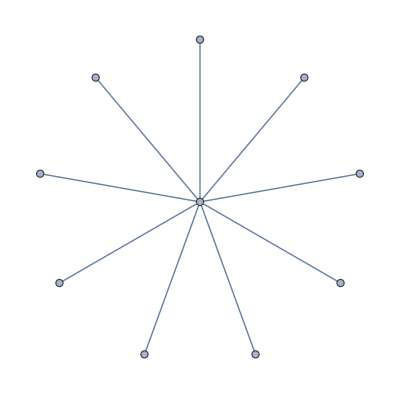
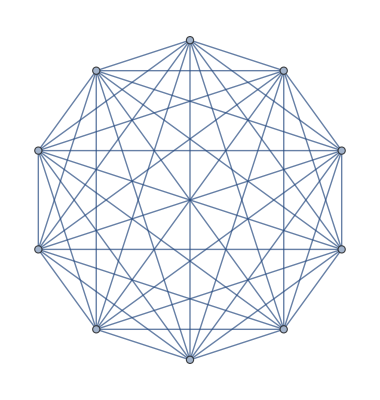

```mathematica
{StarGraph[10], CompleteGraph[10]}
```

Expected vs computed robustness in star and complete graph

```mathematica
{N@(1/100), robustnessSeqAttackBDM[StarGraph[100]]}
```

{0.01,0.0099}

```mathematica
{.5 * (1 - 1/100), robustnessSeqAttackBDM[CompleteGraph[100]]}
```

{0.495,0.495}

```mathematica
SquareBDM[AdjacencyMatrix[StarGraph[5]], 4, 1]
```

105.527

```mathematica
getVertexAttackComplexityRank[StarGraph[5]]
```

{{1,83.5206},{5,75.9639},{4,75.9639},{3,75.9639},{2,75.9639}}

```mathematica
getEdgeAttackComplexityRank[StarGraph[5]]
```

{{1<->2,2.98977},{1<->4,2.71213},{1<->3,1.18206},{1<->5,-0.571505}}

```mathematica
AdjacencyMatrix[VertexDelete[StarGraph[5],2]] // ArrayPlot[#, Mesh-> True]&
```

-Graphics-

```mathematica
origBDM = SquareBDM[AdjacencyMatrix[StarGraph[5]],4, 1]
```

105.527

```mathematica
Table[SquareBDM[AdjacencyMatrix[VertexDelete[StarGraph[5],i]],4, 1], {i, 1, 5, 1}]
```

{22.0067,29.5634,29.5634,29.5634,29.5634}

```mathematica
del1BDM = SquareBDM[AdjacencyMatrix[VertexDelete[StarGraph[5],1]],4, 1]
```

22.0067

```mathematica
del4BDM = SquareBDM[AdjacencyMatrix[VertexDelete[StarGraph[5],4]],4, 1]
```

29.5634

```mathematica
origBDM - del4BDM
```

75.9639

```mathematica
origBDM = SquareBDM[AdjacencyMatrix[VertexDelete[StarGraph[5],2]],4, 1]
```

29.5634

```mathematica
robustnessSeqAttack[StarGraph[5], DegreeCentrality]
```

0.16

```mathematica
Reverse[SortBy[Transpose[{VertexList[#],EigenvectorCentrality[#]}], Last]]&@StarGraph[5]
```

{{1,0.333333},{4,0.166667},{3,0.166667},{2,0.166667},{5,0.166667}}

```mathematica
getVertexAttackComplexityRank[StarGraph[5]]
```

{{1,83.5206},{5,75.9639},{4,75.9639},{3,75.9639},{2,75.9639}}

```mathematica
getVertexAttackComplexityRank[CompleteGraph[5]]
```

{{5,50.1874},{4,50.1874},{3,50.1874},{2,50.1874},{1,50.1874}}

```mathematica
robustnessSeqAttack[StarGraph[5], DegreeCentrality]
```

0.16

```mathematica
robustnessSeqAttackBDM[StarGraph[5]]
```

0.16

```mathematica
robustnessSeqAttackBDM[CompleteGraph[5]]
```

0.4

```mathematica
robustnessSeqAttack[CompleteGraph[5], #]& /@ {BetweennessCentrality, DegreeCentrality,  EigenvectorCentrality}
```

{0.4,0.4,0.4}

```mathematica
getEdgeAttackComplexityRank[StarGraph[5]]
```

{{1<->2,2.98977},{1<->4,2.71213},{1<->3,1.18206},{1<->5,-0.571505}}

```mathematica
robustnessSimAttack[StarGraph[5], DegreeCentrality]
```

0.16

```mathematica
starGraphBDMRobustness = Table[robustnessSeqAttackBDM[StarGraph[i]], {i, 5, 100, 1}]
```

{0.16,0.139,0.122,0.109,0.0988,0.09,0.0826,0.0764,0.071,0.0663,0.0622,0.0586,0.0554,0.0525,0.0499,0.0475,0.0454,0.0434,0.0416,0.0399,0.0384,0.037,0.0357,0.0344,0.0333,0.0322,0.0312,0.0303,0.0294,0.0285,0.0278,0.027,0.0263,0.0256,0.025,0.0244,0.0238,0.0232,0.0227,0.0222,0.0217,0.0213,0.0208,0.0204,0.02,0.0196,0.0192,0.0189,0.0185,0.0182,0.0179,0.0175,0.0172,0.0169,0.0167,0.0164,0.0161,0.0159,0.0156,0.0154,0.0151,0.0149,0.0147,0.0145,0.0143,0.0141,0.0139,0.0137,0.0135,0.0133,0.0132,0.013,0.0128,0.0127,0.0125,0.0123,0.0122,0.012,0.0119,0.0118,0.0116,0.0115,0.0114,0.0112,0.0111,0.011,0.0109,0.0108,0.0106,0.0105,0.0104,0.0103,0.0102,0.0101,0.01,0.0099}

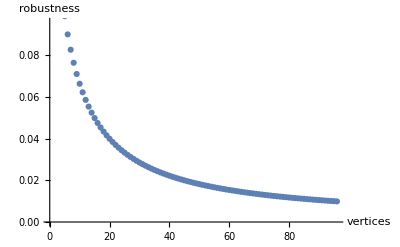
-Graphics-Star Graph - Robustness to Sequential Attack guided by BDM

```mathematica
Labeled[ListPlot[starGraphBDMRobustness, AxesLabel -> {"vertices", "robustness"}], "Star Graph - Robustness to Sequential Attack guided by BDM"]
```

```mathematica
{robustnessSeqAttackBDM[StarGraph[50]], robustnessSeqAttack[StarGraph[50], DegreeCentrality]}
```

{0.0196,0.02}

```mathematica
{robustnessSeqAttackBDM[CompleteGraph[50]], robustnessSeqAttack[CompleteGraph[50], DegreeCentrality]}
```

{0.49,0.49}

```mathematica
completeGraphBDMRobustness = Table[robustnessSeqAttackBDM[CompleteGraph[i]], {i, 5, 100, 1}]
```

{0.4,0.417,0.429,0.438,0.444,0.45,0.455,0.458,0.462,0.464,0.467,0.469,0.471,0.472,0.474,0.475,0.476,0.477,0.478,0.479,0.48,0.481,0.481,0.482,0.483,0.483,0.484,0.484,0.485,0.485,0.486,0.486,0.486,0.487,0.487,0.488,0.488,0.488,0.488,0.489,0.489,0.489,0.489,0.49,0.49,0.49,0.49,0.49,0.491,0.491,0.491,0.491,0.491,0.491,0.492,0.492,0.492,0.492,0.492,0.492,0.492,0.492,0.493,0.493,0.493,0.493,0.493,0.493,0.493,0.493,0.493,0.493,0.494,0.494,0.494,0.494,0.494,0.494,0.494,0.494,0.494,0.494,0.494,0.494,0.494,0.494,0.495,0.495,0.495,0.495,0.495,0.495,0.495,0.495,0.495,0.495}

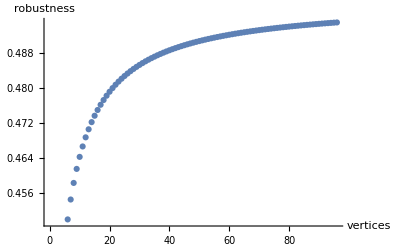
-Graphics-Complete Graph - Robustness to Sequential Attack guided by BDM

```mathematica
Labeled[ListPlot[completeGraphBDMRobustness, AxesLabel->{"vertices", "robustness"}], "Complete Graph - Robustness to Sequential Attack guided by BDM"]
```

The robustness to attacks directed using the Block Decomposition Method agrees with those directed using the degree of each vertex.

```mathematica
starGraphDegreeRobustness = Table[robustnessSeqAttack[StarGraph[i], DegreeCentrality], {i, 5, 100, 1}]
```

{0.16,0.14,0.12,0.11,0.099,0.09,0.083,0.076,0.071,0.066,0.062,0.059,0.055,0.052,0.05,0.048,0.045,0.043,0.042,0.04,0.038,0.037,0.036,0.034,0.033,0.032,0.031,0.03,0.029,0.029,0.028,0.027,0.026,0.026,0.025,0.024,0.024,0.023,0.023,0.022,0.022,0.021,0.021,0.02,0.02,0.02,0.019,0.019,0.019,0.018,0.018,0.018,0.017,0.017,0.017,0.016,0.016,0.016,0.016,0.015,0.015,0.015,0.015,0.014,0.014,0.014,0.014,0.014,0.014,0.013,0.013,0.013,0.013,0.013,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.011,0.011,0.011,0.011,0.011,0.011,0.011,0.011,0.011,0.01,0.01,0.01,0.01,0.01,0.0099}

```mathematica
starGraphBDMRobustness === starGraphDegreeRobustness
```

True

```mathematica
completeGraphDegreeRobustness = Table[robustnessSeqAttack[CompleteGraph[i], DegreeCentrality], {i, 5, 100, 1}]
```

{0.4,0.42,0.43,0.44,0.44,0.45,0.45,0.46,0.46,0.46,0.47,0.47,0.47,0.47,0.47,0.48,0.48,0.48,0.48,0.48,0.48,0.48,0.48,0.48,0.48,0.48,0.48,0.48,0.48,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.5}

```mathematica
completeGraphBDMRobustness === completeGraphDegreeRobustness
```

True

## References

[Zenil16] Zenil, H., Hernández-Orozco, S., Kiani, N. A., Soler-Toscano, F., & Rueda-Toicen, A. (2016). A decomposition method for global evaluation of Shannon entropy and local estimations of algorithmic complexity. arXiv preprint arXiv:1609.00110.

[Zenil14] Zenil H., Soler - Toscano F., Dingle K.and Louis A.(2014) Correlation of Automorphism Group Size and Topological Properties with Program - size Complexity Evaluations of Graphs and Complex Networks, Physica A : Statistical Mechanics and its Applications, vol.404, pp.341–358.

[Iyer13] Iyer, S., Killingback, T., Sundaram, B., & Wang, Z. (2013). Attack robustness and centrality of complex networks. PloS one, 8(4), e59613.

[Soler13] Soler-Toscano, F. and Zenil, H. Kolmogorov Complexity of 3 × 3 and 4 × 4 Squares, Wolfram Demonstrations Project, 2013 http://demonstrations.wolfram.com/KolmogorovComplexityOf33And44Squares/

[Zenil18a] Zenil, H., Kiani, N. A., Zea, A. & Tegnér, J. (2018). Ab initio Algorithmic Causal Deconvolution of Intertwined Programs and Networks by Generative Mechanism. arXiv preprint arXiv:1802.09904.

[Zenil18b] Zenil, H., Kiani, N. A., Rueda-Toicen, A., Zea, A. & Tegnér, J. (2018)  Universal Data Reduction and Network Sparsification Method By Minimal Algorithmic Information Loss arXiv preprint arXiv:1802.05843

[Zenil17 ]Zenil, H., Kiani, N. A., Marabita, F., Deng, Y., Elias, S., Schmidt, A. & Tegner, J. (2017). An Algorithmic Information Calculus for Causal Discovery and Reprogramming Systems. arXiv preprint arXiv:1709.05429.